## Fit student correctness to various models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bvds/Andes2/LogProcessing/moment-of-learning

```mathematica
journalStyle={FontSize->10 (* acm default font for text *)};
```

```mathematica
data["student"]=Import["guerra-summer-2011-kc-opps.csv"];
```

```mathematica
Take[data["student"],5]
```

{{accel-at-rest,asu_9Q1920841f2ca4d1fasul1_c,md5:1da7d76bc3d524d51da47dde26ee8f95,0,1},{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_e,md5:e3e61859acb08ee896e06e1020f95a49,0},{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0},{apply-net-work,asu_9Q1920841f2ca4d1fasul1_e,md5:e66c328693800f93b41f13d97b78e19b,1},{apply-net-work,asu_9Q1920841f2ca4d1fasul1_e,md5:e9747bab59caf0446778cc6a65a8ac2e,0}}

### Calculations for models

Interpolation form of BKT model.  Since exponential is monotonic, have constraints:  0<g<h1<h2<1 or 1>g>h1>h2>0.  The model will stay in [0,1] but the canonical parameters p,g may stray outside.  Also, the exponential may become increasing.

```mathematica
{y,ps}/.Solve[{h1==1-ps-(1-ps-pg)y,h2==1-ps-(1-ps-pg)y^2},{y,ps}]
```

{{(-h1+h2)/(h1-pg),(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)}}

This is used to define bkt2 below.

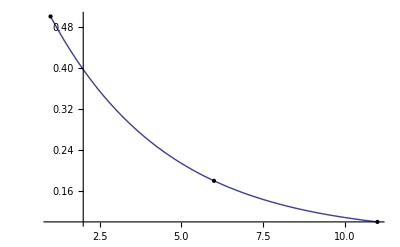

```mathematica
Block[{pg=0.5,h1=.18,h2=0.1,n=11},Plot[bkt2[n][j,{pg,h1,h2}],{j,1,n},Epilog->{PointSize[Large],Point[{1,pg}],Point[{(n+1)/2,h1}],Point[{n,h2}]}]]
```

Linear Interpolation model.  Have constraints:  0<h0,h1<1.

```mathematica
liexpr=Simplify[h0(j-n)/(1-n)+h1 (j-1)/(n-1)]
```

(h1 (-1+j)+h0 (-j+n))/(-1+n)

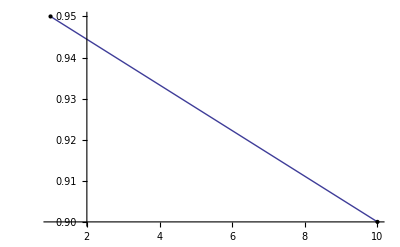

```mathematica
Block[{h0=0.95,h1=.9,n=10},Plot[linear[n][j,{h0,h1}],{j,1,n},Epilog->{PointSize[Large],Point[{1,h0}],Point[{n,h1}]}]]
```

Quadratic Interpolation model.  Have constraints:  0<h0,h1,h2<1.  However, it is easy for the interpolated quadratic to exceed the bounds [0,1].

```mathematica
qiexpr=Simplify[h0(j-(n+1)/2)(j-n)/((1-(n+1)/2) (1-n))+h1 (j-1) (j-n)/(((n+1)/2-1)((n+1)/2-n))+h2 (j-1)(j-(n+1)/2)/((n-1) (n-(n+1)/2))]
```

(h2 (-1+j) (-1+2 j-n)-(j-n) (4 h1 (-1+j)+h0 (1-2 j+n)))/(-1+n)^2

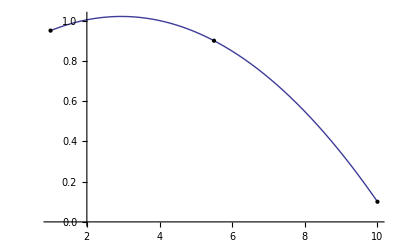

```mathematica
Block[{h0=0.95,h1=.9,h2=0.1,n=10},Plot[qiexpr,{j,1,n},Epilog->{PointSize[Large],Point[{1,h0}],Point[{(n+1)/2,h1}],Point[{n,h2}]}]]
```

### Fitting routines

```mathematica
(* For these functions, n goes from 1 to number of steps *)
logistic[n_,{mu_,b_}]:=1/(Exp[-b  n+mu]+1); (* this choice of parameters gives finite constraint region *)
step[n_,{nl_,pg_,ps_}]:=pg+(Sign[n-nl+1/2]+1) (1-ps-pg)/2;
(* Need (n-1) so ps and pg bounds ares simple *)
bkt[n_,{b_,pg_,ps_}]:=1-ps-(1-ps-pg)*Exp[-b (n-1)];
(* Interpolation form:  this allows for a wider range of model parameters, although canonical parameters may stray out of normal bounds. *)bkt2[n_][j_, {pg_, h1_, h2_}] := Block[{y = (-h1 + h2)/(h1 - pg), 
    ps = (2 h1 - h1^2 - h2 - pg + h2*pg)/(2 h1 - h2 - pg)}, 
   1 - ps - (1 - ps - pg) y^(2(j - 1)/(n - 1))]
(* Linear model in interpolation form. *)
linear[n_][j_,{h0_,h1_}]:=(h1 (j-1)+h0 (n-j))/(n-1)
```

```mathematica
(* AIC for step model calculated explicitly. *)
stepFit[data_,i_]:=Block[{l0=Count[Take[data,i-1],0],l1=Count[Take[data,i-1],1],u0=Count[Drop[data,i-1],0],u1=Count[Drop[data,i-1],1],g,s,logLike=0},If[l0+l1>0,g=l1/(l0+l1);logLike+=If[l1>0,l1*Log[g],0]+If[l0>0,l0*Log[1-g],0]];If[u0+u1>0,s=u0/(u0+u1);logLike+=If[u0>0,u0*Log[s],0]+If[u1>0,u1*Log[1-s],0]];logLike];
stepGain[data_,i_]:=If[i==1,0,Block[{l0=Count[Take[data,i-1],0],l1=Count[Take[data,i-1],1],u0=Count[Drop[data,i-1],0],u1=Count[Drop[data,i-1],1],gain=1},If[l0+l1>0,gain-=l1/(l0+l1)];If[u0+u1>0,gain-=u0/(u0+u1)];gain]];
stepFit[data_]:=Block[{best=-Infinity,lBest},Do[Block[{logLike=stepFit[data,i]},If[logLike>best,best=logLike;lBest=i]],{i,Length[data]}];
(* Not clear if this is really 3 parameters when data is short *)If[Length[data]≥3,2*3-2*N[best]]]
```

AIC for constant model (one parameter) calculated explicitly.  Since this is a special case of the other three models, the other models should never have a worse log likelihood fit.

```mathematica
constantFit[data_]:=Block[{u0=Count[data,0],u1=Count[data,1],s},s=u0/(u0+u1);2*1-2*(If[u0>0,u0*Log[s],0]+If[u1>0,u1*Log[1-s],0])]
```

```mathematica
(* Akaike weights for step model when all L are equally probable. *)
avgWeights[n_]:=Table[If[i==1,Exp[1],1],{i,n}]/(Exp[1]+n-1)
```

```mathematica
logger[x_?NumberQ,params_]:= (* not used now. *)Which[0<x≤1,Log[x],x==0,(* NMaximize can't handle -Infinity *)-10^50,True,Print["Invalid probability ",x," for ",params];If[x<0,-Infinity,0]]
logProb[model_,params_,data_]:=Sum[Log[If[data[[i]]==1,model[i,params],1-model[i,params]]],{i,Length[data]}]
maxer[model_,vars_,constraints_,data_]:=Which[
(* too few data points *)
Length[data]<Length[vars],Null,
(* All three functions can perfectly fit to all ones or zeros, but numerical fit is hard. *)
Count[data,0]==0 || Count[data,1]==0,2 Length[vars],True,
Block[{x=NMaximize[{logProb[model,vars,data],constraints[data]},vars,
(* If you plot the likelihood as a function of parameter, you see a space with many valleys, presumably one per data point.  Thus we make the number of starting points propotional to length of the dataset. *)Method->{"RandomSearch","SearchPoints"->Max[10 Length[vars],2Length[data],100],Method->"ConjugateGradient"}]},If[NumberQ[x[[1]]],2Length[vars]-2 x[[1]],Print[data,x];False]]]
```

```mathematica
logisticConstraints[x_]:=Block[{delta=15,ones=Position[x,1,1],zeros=Position[x,0,1]},mu≥Max[zeros[[-1,1]]*b,zeros[[1,1]]*b]-delta&& mu≤Min[ones[[1,1]]*b,ones[[-1,1]]*b]+delta&& b>-2 delta/Max[1,ones[[-1,1]]-zeros[[1,1]]] && b<2 delta/Max[1,zeros[[-1,1]]-ones[[1,1]]]]
```

```mathematica
bktConstraints[_]:=Block[{delta=15},pg≥Exp[-delta] && ps≥Exp[-delta] && pg≤1-Exp[-delta] && ps≤ 1-Exp[-delta] &&b≥0 && b<delta]
```

```mathematica
bkt2Constraints[x_]:=Block[{delta=15},pg≥Exp[-delta] && h1≥Exp[-delta] && h2≥Exp[-delta] &&pg≤1-Exp[-delta] && h1<= 1-Exp[-delta] && h2<1-Exp[-delta]] && (h1-pg) (h2-h1)>0
```

```mathematica
linearConstraints[x_]:=Block[{delta=15}, h0≥Exp[-delta] && h1≥Exp[-delta] && h0<= 1-Exp[-delta] && h1<1-Exp[-delta]]
```

Correction to get AIC_c

```mathematica
aicCorrection[k_,n_]:=2 k (k+1)/(n-k-1)
```

### Generate random data and table of AIC' s

Best possible data set

```mathematica
data["ideal",n_:1]:=Flatten[Table[Map[Block[{nd=Length[#]-3,nn},nn=If[nd==1,1,RandomInteger[nd-2]+1];Join[{Null,Null,Null},Table[0,{nn}],Table[1,{nd-nn}]]]&,data["student"]],{n}],1];
```

Make random data, 50 % correct

```mathematica
data["randomC",n_,length_]:=Table[Join[{Null,Null,Null},Table[RandomInteger[],{n}]],{length}];
```

Make random data, span space, with 50 % correct

```mathematica
data["even",n_]:=Table[Join[{Null,Null,Null},IntegerDigits[i-1,2,n]],{i,2^n}];
```

```mathematica
data["random",n_:1]:=Flatten[Table[Map[Join[{Null,Null,Null},Table[RandomInteger[],{Length[Drop[#,3]]}]]&,data["student"]],{n}],1];
```

```mathematica
data["reorder",n_:1]:=Flatten[Table[Map[Join[{Null,Null,Null},RandomSample[Drop[#,3]]]&,data["student"]],{n}],1];
```

Make exponential data

```mathematica
data["exponential"]=Table[Join[{Null,Null,Null},Block[{a=Random[],b=Random[],c=Random[],n=100},Table[If[Random[]<a+(b-a) c^( i/n),1,0],{i,n}]]],{100}];
```

```mathematica
ColumnForm[Transpose[{data["student"],data["ideal"]}]]
```

Make random data with triangle probability distribution.  The idea here is that none of the three models will fit this distribution well.

```mathematica
data["triangle",n_,length_]:=Table[Join[{Null,Null,Null},Table[If[Random[]*(n-1)<2*Min[i-1,n-i],1,0],{i,n}]],{length}];
```

### Generate full tables of AIC' s

```mathematica
generateAICs[set__]:=Map[{#[[1]],#[[3]],Length[Drop[#,3]],Print[#[[1]]," logistic ",#[[3]]];maxer[logistic,{mu,b},logisticConstraints,Drop[#,3]],stepFit[Drop[#,3]],Print[#[[1]]," bkt ",#[[3]]];maxer[bkt,{b,pg,ps},bktConstraints,Drop[#,3]],maxer[bkt2[Length[Drop[#,3]]],{pg,h1,h2},bkt2Constraints,Drop[#,3]],constantFit[Drop[#,3]],maxer[linear[Length[Drop[#,3]]],{h0,h1},linearConstraints,Drop[#,3]]}&,data[set]]
```

This takes a long time to calculate.  Do as batch process; see file "generate-fits.m"

```mathematica
allValues=generateAICs["student"];
```

accel-at-rest logistic md5:1da7d76bc3d524d51da47dde26ee8f95

accel-at-rest bkt md5:1da7d76bc3d524d51da47dde26ee8f95

accel-constant-speed logistic md5:e3e61859acb08ee896e06e1020f95a49

accel-constant-speed bkt md5:e3e61859acb08ee896e06e1020f95a49

accel-constant-speed logistic md5:b50efcf571b671cf01b499841c66daf2

accel-constant-speed bkt md5:b50efcf571b671cf01b499841c66daf2

apply-net-work logistic md5:e66c328693800f93b41f13d97b78e19b

apply-net-work bkt md5:e66c328693800f93b41f13d97b78e19b

apply-net-work logistic md5:e9747bab59caf0446778cc6a65a8ac2e

apply-net-work bkt md5:e9747bab59caf0446778cc6a65a8ac2e

area-of-circle logistic md5:5e8914eb96d8caf02138110b93b5add5

area-of-circle bkt md5:5e8914eb96d8caf02138110b93b5add5

area-of-circle logistic md5:98deb41457bbea23b29b480e9530ad7c

area-of-circle bkt md5:98deb41457bbea23b29b480e9530ad7c

area-of-circle logistic md5:e9747bab59caf0446778cc6a65a8ac2e

area-of-circle bkt md5:e9747bab59caf0446778cc6a65a8ac2e

area-of-circle logistic md5:e3e61859acb08ee896e06e1020f95a49

area-of-circle bkt md5:e3e61859acb08ee896e06e1020f95a49

area-of-circle logistic md5:1da7d76bc3d524d51da47dde26ee8f95

area-of-circle bkt md5:1da7d76bc3d524d51da47dde26ee8f95

area-of-circle logistic md5:a38723384afd4471b62218d16045a11d

area-of-circle bkt md5:a38723384afd4471b62218d16045a11d

area-of-circle logistic md5:55108dec2fb88e9c2af83be92d0520de

area-of-circle bkt md5:55108dec2fb88e9c2af83be92d0520de

area-of-circle logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

area-of-circle bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

area-of-circle logistic md5:b50efcf571b671cf01b499841c66daf2

area-of-circle bkt md5:b50efcf571b671cf01b499841c66daf2

bernoulli logistic md5:a38723384afd4471b62218d16045a11d

Experimental`NumericalFunction::nnum: The function value Indeterminate is not a number at {b, mu} = {-30., -109.118}.

General::stop: Further output of Experimental`NumericalFunction :: nnum will be suppressed during this calculation.

bernoulli bkt md5:a38723384afd4471b62218d16045a11d

bernoulli logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

bernoulli bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

bernoulli logistic md5:55108dec2fb88e9c2af83be92d0520de

bernoulli bkt md5:55108dec2fb88e9c2af83be92d0520de

bernoulli logistic md5:b50efcf571b671cf01b499841c66daf2

bernoulli bkt md5:b50efcf571b671cf01b499841c66daf2

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

bernoulli logistic md5:1da7d76bc3d524d51da47dde26ee8f95

bernoulli bkt md5:1da7d76bc3d524d51da47dde26ee8f95

bernoulli logistic md5:e66c328693800f93b41f13d97b78e19b

bernoulli bkt md5:e66c328693800f93b41f13d97b78e19b

bernoulli logistic md5:e3e61859acb08ee896e06e1020f95a49

bernoulli bkt md5:e3e61859acb08ee896e06e1020f95a49

bernoulli logistic md5:e9747bab59caf0446778cc6a65a8ac2e

bernoulli bkt md5:e9747bab59caf0446778cc6a65a8ac2e

bernoulli logistic md5:8a075e35a0daf7e231f60497d036689a

bernoulli bkt md5:8a075e35a0daf7e231f60497d036689a

combo-magnification logistic md5:a38723384afd4471b62218d16045a11d

combo-magnification bkt md5:a38723384afd4471b62218d16045a11d

combo-magnification logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

combo-magnification bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

combo-magnification logistic md5:b50efcf571b671cf01b499841c66daf2

combo-magnification bkt md5:b50efcf571b671cf01b499841c66daf2

combo-magnification logistic md5:1da7d76bc3d524d51da47dde26ee8f95

combo-magnification bkt md5:1da7d76bc3d524d51da47dde26ee8f95

combo-magnification logistic md5:55108dec2fb88e9c2af83be92d0520de

combo-magnification bkt md5:55108dec2fb88e9c2af83be92d0520de

combo-magnification logistic md5:e66c328693800f93b41f13d97b78e19b

combo-magnification bkt md5:e66c328693800f93b41f13d97b78e19b

combo-magnification logistic md5:e3e61859acb08ee896e06e1020f95a49

combo-magnification bkt md5:e3e61859acb08ee896e06e1020f95a49

combo-magnification logistic md5:e9747bab59caf0446778cc6a65a8ac2e

combo-magnification bkt md5:e9747bab59caf0446778cc6a65a8ac2e

combo-magnification logistic md5:8a075e35a0daf7e231f60497d036689a

combo-magnification bkt md5:8a075e35a0daf7e231f60497d036689a

compo-general-case logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-general-case bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-general-case logistic md5:fd9e6b9f34db6df883c666a7c86820b4

compo-general-case bkt md5:fd9e6b9f34db6df883c666a7c86820b4

compo-general-case logistic md5:a38723384afd4471b62218d16045a11d

compo-general-case bkt md5:a38723384afd4471b62218d16045a11d

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

compo-general-case logistic md5:b50efcf571b671cf01b499841c66daf2

compo-general-case bkt md5:b50efcf571b671cf01b499841c66daf2

compo-general-case logistic md5:1da7d76bc3d524d51da47dde26ee8f95

compo-general-case bkt md5:1da7d76bc3d524d51da47dde26ee8f95

compo-general-case logistic md5:55108dec2fb88e9c2af83be92d0520de

compo-general-case bkt md5:55108dec2fb88e9c2af83be92d0520de

compo-general-case logistic md5:5e8914eb96d8caf02138110b93b5add5

compo-general-case bkt md5:5e8914eb96d8caf02138110b93b5add5

compo-general-case logistic md5:e3e61859acb08ee896e06e1020f95a49

compo-general-case bkt md5:e3e61859acb08ee896e06e1020f95a49

compo-general-case logistic md5:98deb41457bbea23b29b480e9530ad7c

compo-general-case bkt md5:98deb41457bbea23b29b480e9530ad7c

compo-general-case logistic md5:e9747bab59caf0446778cc6a65a8ac2e

compo-general-case bkt md5:e9747bab59caf0446778cc6a65a8ac2e

compo-general-case logistic md5:e66c328693800f93b41f13d97b78e19b

compo-general-case bkt md5:e66c328693800f93b41f13d97b78e19b

compo-general-case logistic md5:8a075e35a0daf7e231f60497d036689a

compo-general-case bkt md5:8a075e35a0daf7e231f60497d036689a

compo-general-case-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-general-case-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-general-case-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

compo-general-case-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

compo-general-case-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

compo-general-case-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

compo-general-case-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

compo-general-case-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

compo-general-case-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

compo-general-case-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

compo-general-case-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

compo-general-case-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

compo-parallel-axis logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-parallel-axis bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-parallel-axis logistic md5:b50efcf571b671cf01b499841c66daf2

compo-parallel-axis bkt md5:b50efcf571b671cf01b499841c66daf2

compo-parallel-axis logistic md5:1da7d76bc3d524d51da47dde26ee8f95

compo-parallel-axis bkt md5:1da7d76bc3d524d51da47dde26ee8f95

compo-parallel-axis logistic md5:a38723384afd4471b62218d16045a11d

compo-parallel-axis bkt md5:a38723384afd4471b62218d16045a11d

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize :: cvmit will be suppressed during this calculation.

compo-parallel-axis logistic md5:55108dec2fb88e9c2af83be92d0520de

compo-parallel-axis bkt md5:55108dec2fb88e9c2af83be92d0520de

compo-parallel-axis logistic md5:5e8914eb96d8caf02138110b93b5add5

compo-parallel-axis bkt md5:5e8914eb96d8caf02138110b93b5add5

compo-parallel-axis logistic md5:e3e61859acb08ee896e06e1020f95a49

compo-parallel-axis bkt md5:e3e61859acb08ee896e06e1020f95a49

compo-parallel-axis logistic md5:98deb41457bbea23b29b480e9530ad7c

compo-parallel-axis bkt md5:98deb41457bbea23b29b480e9530ad7c

compo-parallel-axis logistic md5:e9747bab59caf0446778cc6a65a8ac2e

compo-parallel-axis bkt md5:e9747bab59caf0446778cc6a65a8ac2e

compo-parallel-axis logistic md5:e66c328693800f93b41f13d97b78e19b

compo-parallel-axis bkt md5:e66c328693800f93b41f13d97b78e19b

compo-parallel-axis logistic md5:8a075e35a0daf7e231f60497d036689a

compo-parallel-axis bkt md5:8a075e35a0daf7e231f60497d036689a

compo-perpendicular logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-perpendicular bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-perpendicular logistic md5:b50efcf571b671cf01b499841c66daf2

compo-perpendicular bkt md5:b50efcf571b671cf01b499841c66daf2

compo-perpendicular logistic md5:1da7d76bc3d524d51da47dde26ee8f95

compo-perpendicular bkt md5:1da7d76bc3d524d51da47dde26ee8f95

compo-perpendicular logistic md5:a38723384afd4471b62218d16045a11d

compo-perpendicular bkt md5:a38723384afd4471b62218d16045a11d

compo-perpendicular logistic md5:55108dec2fb88e9c2af83be92d0520de

compo-perpendicular bkt md5:55108dec2fb88e9c2af83be92d0520de

compo-perpendicular logistic md5:5e8914eb96d8caf02138110b93b5add5

compo-perpendicular bkt md5:5e8914eb96d8caf02138110b93b5add5

compo-perpendicular logistic md5:e3e61859acb08ee896e06e1020f95a49

compo-perpendicular bkt md5:e3e61859acb08ee896e06e1020f95a49

compo-perpendicular logistic md5:98deb41457bbea23b29b480e9530ad7c

compo-perpendicular bkt md5:98deb41457bbea23b29b480e9530ad7c

compo-perpendicular logistic md5:e9747bab59caf0446778cc6a65a8ac2e

compo-perpendicular bkt md5:e9747bab59caf0446778cc6a65a8ac2e

compo-perpendicular logistic md5:e66c328693800f93b41f13d97b78e19b

compo-perpendicular bkt md5:e66c328693800f93b41f13d97b78e19b

compo-perpendicular logistic md5:8a075e35a0daf7e231f60497d036689a

compo-perpendicular bkt md5:8a075e35a0daf7e231f60497d036689a

compo-z-axis logistic md5:98deb41457bbea23b29b480e9530ad7c

compo-z-axis bkt md5:98deb41457bbea23b29b480e9530ad7c

compo-z-axis logistic md5:e3e61859acb08ee896e06e1020f95a49

compo-z-axis bkt md5:e3e61859acb08ee896e06e1020f95a49

compo-z-axis logistic md5:5e8914eb96d8caf02138110b93b5add5

compo-z-axis bkt md5:5e8914eb96d8caf02138110b93b5add5

compo-z-axis logistic md5:e66c328693800f93b41f13d97b78e19b

compo-z-axis bkt md5:e66c328693800f93b41f13d97b78e19b

compo-z-axis logistic md5:e9747bab59caf0446778cc6a65a8ac2e

compo-z-axis bkt md5:e9747bab59caf0446778cc6a65a8ac2e

compo-z-axis logistic md5:8a075e35a0daf7e231f60497d036689a

compo-z-axis bkt md5:8a075e35a0daf7e231f60497d036689a

compo-z-axis logistic md5:a38723384afd4471b62218d16045a11d

compo-z-axis bkt md5:a38723384afd4471b62218d16045a11d

compo-z-axis logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-z-axis bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-z-axis logistic md5:55108dec2fb88e9c2af83be92d0520de

compo-z-axis bkt md5:55108dec2fb88e9c2af83be92d0520de

compo-z-axis logistic md5:b50efcf571b671cf01b499841c66daf2

compo-z-axis bkt md5:b50efcf571b671cf01b499841c66daf2

compo-z-axis logistic md5:1da7d76bc3d524d51da47dde26ee8f95

compo-z-axis bkt md5:1da7d76bc3d524d51da47dde26ee8f95

compo-zero-vector logistic md5:5e8914eb96d8caf02138110b93b5add5

compo-zero-vector bkt md5:5e8914eb96d8caf02138110b93b5add5

compo-zero-vector logistic md5:e3e61859acb08ee896e06e1020f95a49

compo-zero-vector bkt md5:e3e61859acb08ee896e06e1020f95a49

compo-zero-vector logistic md5:98deb41457bbea23b29b480e9530ad7c

compo-zero-vector bkt md5:98deb41457bbea23b29b480e9530ad7c

compo-zero-vector logistic md5:e66c328693800f93b41f13d97b78e19b

compo-zero-vector bkt md5:e66c328693800f93b41f13d97b78e19b

compo-zero-vector logistic md5:a38723384afd4471b62218d16045a11d

compo-zero-vector bkt md5:a38723384afd4471b62218d16045a11d

compo-zero-vector logistic md5:55108dec2fb88e9c2af83be92d0520de

compo-zero-vector bkt md5:55108dec2fb88e9c2af83be92d0520de

compo-zero-vector logistic md5:b50efcf571b671cf01b499841c66daf2

compo-zero-vector bkt md5:b50efcf571b671cf01b499841c66daf2

compo-zero-vector logistic md5:1da7d76bc3d524d51da47dde26ee8f95

compo-zero-vector bkt md5:1da7d76bc3d524d51da47dde26ee8f95

continuity logistic md5:a38723384afd4471b62218d16045a11d

continuity bkt md5:a38723384afd4471b62218d16045a11d

continuity logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

continuity bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

continuity logistic md5:55108dec2fb88e9c2af83be92d0520de

continuity bkt md5:55108dec2fb88e9c2af83be92d0520de

continuity logistic md5:b50efcf571b671cf01b499841c66daf2

continuity bkt md5:b50efcf571b671cf01b499841c66daf2

continuity logistic md5:1da7d76bc3d524d51da47dde26ee8f95

continuity bkt md5:1da7d76bc3d524d51da47dde26ee8f95

continuity logistic md5:e66c328693800f93b41f13d97b78e19b

continuity bkt md5:e66c328693800f93b41f13d97b78e19b

continuity logistic md5:e3e61859acb08ee896e06e1020f95a49

continuity bkt md5:e3e61859acb08ee896e06e1020f95a49

continuity logistic md5:e9747bab59caf0446778cc6a65a8ac2e

continuity bkt md5:e9747bab59caf0446778cc6a65a8ac2e

continuity logistic md5:8a075e35a0daf7e231f60497d036689a

continuity bkt md5:8a075e35a0daf7e231f60497d036689a

define-angle-between-lines logistic md5:a38723384afd4471b62218d16045a11d

define-angle-between-lines bkt md5:a38723384afd4471b62218d16045a11d

define-angle-between-lines logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-angle-between-lines bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-angle-between-lines logistic md5:b50efcf571b671cf01b499841c66daf2

define-angle-between-lines bkt md5:b50efcf571b671cf01b499841c66daf2

define-angle-between-lines logistic md5:55108dec2fb88e9c2af83be92d0520de

define-angle-between-lines bkt md5:55108dec2fb88e9c2af83be92d0520de

define-angle-between-lines logistic md5:e66c328693800f93b41f13d97b78e19b

define-angle-between-lines bkt md5:e66c328693800f93b41f13d97b78e19b

define-angle-between-lines logistic md5:e3e61859acb08ee896e06e1020f95a49

define-angle-between-lines bkt md5:e3e61859acb08ee896e06e1020f95a49

define-angle-between-lines logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-angle-between-lines bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-angle-between-lines logistic md5:8a075e35a0daf7e231f60497d036689a

define-angle-between-lines bkt md5:8a075e35a0daf7e231f60497d036689a

define-angle-between-vectors logistic md5:e3e61859acb08ee896e06e1020f95a49

define-angle-between-vectors bkt md5:e3e61859acb08ee896e06e1020f95a49

define-angle-between-vectors logistic md5:e66c328693800f93b41f13d97b78e19b

define-angle-between-vectors bkt md5:e66c328693800f93b41f13d97b78e19b

define-angular-frequency logistic md5:e3e61859acb08ee896e06e1020f95a49

define-angular-frequency bkt md5:e3e61859acb08ee896e06e1020f95a49

define-angular-frequency logistic md5:b50efcf571b671cf01b499841c66daf2

define-angular-frequency bkt md5:b50efcf571b671cf01b499841c66daf2

define-area logistic md5:a38723384afd4471b62218d16045a11d

define-area bkt md5:a38723384afd4471b62218d16045a11d

define-area logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-area bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-area logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-area bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-area logistic md5:b50efcf571b671cf01b499841c66daf2

define-area bkt md5:b50efcf571b671cf01b499841c66daf2

define-area logistic md5:55108dec2fb88e9c2af83be92d0520de

define-area bkt md5:55108dec2fb88e9c2af83be92d0520de

define-area logistic md5:e66c328693800f93b41f13d97b78e19b

define-area bkt md5:e66c328693800f93b41f13d97b78e19b

define-area logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-area bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-area logistic md5:e3e61859acb08ee896e06e1020f95a49

define-area bkt md5:e3e61859acb08ee896e06e1020f95a49

define-area logistic md5:8a075e35a0daf7e231f60497d036689a

define-area bkt md5:8a075e35a0daf7e231f60497d036689a

define-area-at logistic md5:a38723384afd4471b62218d16045a11d

define-area-at bkt md5:a38723384afd4471b62218d16045a11d

define-area-at logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-area-at bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-area-at logistic md5:55108dec2fb88e9c2af83be92d0520de

define-area-at bkt md5:55108dec2fb88e9c2af83be92d0520de

define-area-at logistic md5:b50efcf571b671cf01b499841c66daf2

define-area-at bkt md5:b50efcf571b671cf01b499841c66daf2

define-area-at logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-area-at bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-area-at logistic md5:e66c328693800f93b41f13d97b78e19b

define-area-at bkt md5:e66c328693800f93b41f13d97b78e19b

define-area-at logistic md5:e3e61859acb08ee896e06e1020f95a49

define-area-at bkt md5:e3e61859acb08ee896e06e1020f95a49

define-area-at logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-area-at bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-area-at logistic md5:8a075e35a0daf7e231f60497d036689a

define-area-at bkt md5:8a075e35a0daf7e231f60497d036689a

define-atmosphere-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-atmosphere-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-capacitance-var logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-capacitance-var bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-capacitance-var logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-capacitance-var bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-capacitance-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-capacitance-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-capacitance-var logistic md5:e3e61859acb08ee896e06e1020f95a49

define-capacitance-var bkt md5:e3e61859acb08ee896e06e1020f95a49

define-charge logistic md5:e3e61859acb08ee896e06e1020f95a49

define-charge bkt md5:e3e61859acb08ee896e06e1020f95a49

define-charge logistic md5:5e8914eb96d8caf02138110b93b5add5

define-charge bkt md5:5e8914eb96d8caf02138110b93b5add5

define-charge logistic md5:98deb41457bbea23b29b480e9530ad7c

define-charge bkt md5:98deb41457bbea23b29b480e9530ad7c

define-charge logistic md5:e66c328693800f93b41f13d97b78e19b

define-charge bkt md5:e66c328693800f93b41f13d97b78e19b

define-charge logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-charge bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-charge logistic md5:8a075e35a0daf7e231f60497d036689a

define-charge bkt md5:8a075e35a0daf7e231f60497d036689a

define-charge logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-charge bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-charge logistic md5:a38723384afd4471b62218d16045a11d

define-charge bkt md5:a38723384afd4471b62218d16045a11d

define-charge logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-charge bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-charge logistic md5:55108dec2fb88e9c2af83be92d0520de

define-charge bkt md5:55108dec2fb88e9c2af83be92d0520de

define-charge logistic md5:b50efcf571b671cf01b499841c66daf2

define-charge bkt md5:b50efcf571b671cf01b499841c66daf2

define-coef-friction logistic md5:98deb41457bbea23b29b480e9530ad7c

define-coef-friction bkt md5:98deb41457bbea23b29b480e9530ad7c

define-coef-friction logistic md5:e3e61859acb08ee896e06e1020f95a49

define-coef-friction bkt md5:e3e61859acb08ee896e06e1020f95a49

define-coef-friction logistic md5:e66c328693800f93b41f13d97b78e19b

define-coef-friction bkt md5:e66c328693800f93b41f13d97b78e19b

define-coef-friction logistic md5:5e8914eb96d8caf02138110b93b5add5

define-coef-friction bkt md5:5e8914eb96d8caf02138110b93b5add5

define-coef-friction logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-coef-friction bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-coef-friction logistic md5:a38723384afd4471b62218d16045a11d

define-coef-friction bkt md5:a38723384afd4471b62218d16045a11d

define-coef-friction logistic md5:b50efcf571b671cf01b499841c66daf2

define-coef-friction bkt md5:b50efcf571b671cf01b499841c66daf2

define-coef-friction logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-coef-friction bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-coef-friction logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-coef-friction bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-compression logistic md5:a38723384afd4471b62218d16045a11d

define-compression bkt md5:a38723384afd4471b62218d16045a11d

define-compression logistic md5:b50efcf571b671cf01b499841c66daf2

define-compression bkt md5:b50efcf571b671cf01b499841c66daf2

define-compression logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-compression bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-compression logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-compression bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-compression logistic md5:55108dec2fb88e9c2af83be92d0520de

define-compression bkt md5:55108dec2fb88e9c2af83be92d0520de

define-compression logistic md5:e3e61859acb08ee896e06e1020f95a49

define-compression bkt md5:e3e61859acb08ee896e06e1020f95a49

define-compression logistic md5:5e8914eb96d8caf02138110b93b5add5

define-compression bkt md5:5e8914eb96d8caf02138110b93b5add5

define-compression logistic md5:e66c328693800f93b41f13d97b78e19b

define-compression bkt md5:e66c328693800f93b41f13d97b78e19b

define-compression logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-compression bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-compression logistic md5:98deb41457bbea23b29b480e9530ad7c

define-compression bkt md5:98deb41457bbea23b29b480e9530ad7c

define-current-thru logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-current-thru bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-current-thru logistic md5:a38723384afd4471b62218d16045a11d

define-current-thru bkt md5:a38723384afd4471b62218d16045a11d

define-current-thru logistic md5:b50efcf571b671cf01b499841c66daf2

define-current-thru bkt md5:b50efcf571b671cf01b499841c66daf2

define-current-thru logistic md5:55108dec2fb88e9c2af83be92d0520de

define-current-thru bkt md5:55108dec2fb88e9c2af83be92d0520de

define-current-thru logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-current-thru bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-current-thru logistic md5:e66c328693800f93b41f13d97b78e19b

define-current-thru bkt md5:e66c328693800f93b41f13d97b78e19b

define-current-thru logistic md5:8a075e35a0daf7e231f60497d036689a

define-current-thru bkt md5:8a075e35a0daf7e231f60497d036689a

define-current-thru logistic md5:e3e61859acb08ee896e06e1020f95a49

define-current-thru bkt md5:e3e61859acb08ee896e06e1020f95a49

define-current-thru logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-current-thru bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-distance logistic md5:a38723384afd4471b62218d16045a11d

define-distance bkt md5:a38723384afd4471b62218d16045a11d

define-distance logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-distance bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-distance logistic md5:55108dec2fb88e9c2af83be92d0520de

define-distance bkt md5:55108dec2fb88e9c2af83be92d0520de

define-distance logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-distance bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-distance logistic md5:b50efcf571b671cf01b499841c66daf2

define-distance bkt md5:b50efcf571b671cf01b499841c66daf2

define-distance logistic md5:98deb41457bbea23b29b480e9530ad7c

define-distance bkt md5:98deb41457bbea23b29b480e9530ad7c

define-distance logistic md5:e3e61859acb08ee896e06e1020f95a49

define-distance bkt md5:e3e61859acb08ee896e06e1020f95a49

define-distance logistic md5:e66c328693800f93b41f13d97b78e19b

define-distance bkt md5:e66c328693800f93b41f13d97b78e19b

define-distance logistic md5:5e8914eb96d8caf02138110b93b5add5

define-distance bkt md5:5e8914eb96d8caf02138110b93b5add5

define-distance logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-distance bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-distance logistic md5:8a075e35a0daf7e231f60497d036689a

define-distance bkt md5:8a075e35a0daf7e231f60497d036689a

define-distance-between logistic md5:e66c328693800f93b41f13d97b78e19b

define-distance-between bkt md5:e66c328693800f93b41f13d97b78e19b

define-distance-between logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-distance-between bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-distance-between logistic md5:e3e61859acb08ee896e06e1020f95a49

define-distance-between bkt md5:e3e61859acb08ee896e06e1020f95a49

define-distance-between logistic md5:8a075e35a0daf7e231f60497d036689a

define-distance-between bkt md5:8a075e35a0daf7e231f60497d036689a

define-distance-between logistic md5:a38723384afd4471b62218d16045a11d

define-distance-between bkt md5:a38723384afd4471b62218d16045a11d

define-distance-between logistic md5:b50efcf571b671cf01b499841c66daf2

define-distance-between bkt md5:b50efcf571b671cf01b499841c66daf2

define-distance-between logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-distance-between bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-distance-between logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-distance-between bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-distance-between logistic md5:55108dec2fb88e9c2af83be92d0520de

define-distance-between bkt md5:55108dec2fb88e9c2af83be92d0520de

define-duration logistic md5:a38723384afd4471b62218d16045a11d

define-duration bkt md5:a38723384afd4471b62218d16045a11d

define-duration logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-duration bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-duration logistic md5:55108dec2fb88e9c2af83be92d0520de

define-duration bkt md5:55108dec2fb88e9c2af83be92d0520de

define-duration logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-duration bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-duration logistic md5:b50efcf571b671cf01b499841c66daf2

define-duration bkt md5:b50efcf571b671cf01b499841c66daf2

define-duration logistic md5:98deb41457bbea23b29b480e9530ad7c

define-duration bkt md5:98deb41457bbea23b29b480e9530ad7c

define-duration logistic md5:e3e61859acb08ee896e06e1020f95a49

define-duration bkt md5:e3e61859acb08ee896e06e1020f95a49

define-duration logistic md5:e66c328693800f93b41f13d97b78e19b

define-duration bkt md5:e66c328693800f93b41f13d97b78e19b

define-duration logistic md5:5e8914eb96d8caf02138110b93b5add5

define-duration bkt md5:5e8914eb96d8caf02138110b93b5add5

define-duration logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-duration bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-duration logistic md5:8a075e35a0daf7e231f60497d036689a

define-duration bkt md5:8a075e35a0daf7e231f60497d036689a

define-electric-power-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-electric-power-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-electric-power-var logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-electric-power-var bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-electric-power-var logistic md5:8a075e35a0daf7e231f60497d036689a

define-electric-power-var bkt md5:8a075e35a0daf7e231f60497d036689a

define-electric-power-var logistic md5:a38723384afd4471b62218d16045a11d

define-electric-power-var bkt md5:a38723384afd4471b62218d16045a11d

define-electric-power-var logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-electric-power-var bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-electric-power-var logistic md5:b50efcf571b671cf01b499841c66daf2

define-electric-power-var bkt md5:b50efcf571b671cf01b499841c66daf2

define-electric-power-var logistic md5:55108dec2fb88e9c2af83be92d0520de

define-electric-power-var bkt md5:55108dec2fb88e9c2af83be92d0520de

define-electric-power-var logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-electric-power-var bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-energy-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-energy-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-energy-var logistic md5:e3e61859acb08ee896e06e1020f95a49

define-energy-var bkt md5:e3e61859acb08ee896e06e1020f95a49

define-energy-var logistic md5:8a075e35a0daf7e231f60497d036689a

define-energy-var bkt md5:8a075e35a0daf7e231f60497d036689a

define-energy-var logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-energy-var bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-energy-var logistic md5:b50efcf571b671cf01b499841c66daf2

define-energy-var bkt md5:b50efcf571b671cf01b499841c66daf2

define-flux logistic md5:a38723384afd4471b62218d16045a11d

define-flux bkt md5:a38723384afd4471b62218d16045a11d

define-flux logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-flux bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-flux logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-flux bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-flux logistic md5:b50efcf571b671cf01b499841c66daf2

define-flux bkt md5:b50efcf571b671cf01b499841c66daf2

define-flux logistic md5:55108dec2fb88e9c2af83be92d0520de

define-flux bkt md5:55108dec2fb88e9c2af83be92d0520de

define-flux logistic md5:e66c328693800f93b41f13d97b78e19b

define-flux bkt md5:e66c328693800f93b41f13d97b78e19b

define-flux logistic md5:e3e61859acb08ee896e06e1020f95a49

define-flux bkt md5:e3e61859acb08ee896e06e1020f95a49

define-flux logistic md5:8a075e35a0daf7e231f60497d036689a

define-flux bkt md5:8a075e35a0daf7e231f60497d036689a

define-focal-length logistic md5:a38723384afd4471b62218d16045a11d

define-focal-length bkt md5:a38723384afd4471b62218d16045a11d

define-focal-length logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-focal-length bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-focal-length logistic md5:b50efcf571b671cf01b499841c66daf2

define-focal-length bkt md5:b50efcf571b671cf01b499841c66daf2

define-focal-length logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-focal-length bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-focal-length logistic md5:55108dec2fb88e9c2af83be92d0520de

define-focal-length bkt md5:55108dec2fb88e9c2af83be92d0520de

define-focal-length logistic md5:8a075e35a0daf7e231f60497d036689a

define-focal-length bkt md5:8a075e35a0daf7e231f60497d036689a

define-focal-length logistic md5:e66c328693800f93b41f13d97b78e19b

define-focal-length bkt md5:e66c328693800f93b41f13d97b78e19b

define-focal-length logistic md5:e3e61859acb08ee896e06e1020f95a49

define-focal-length bkt md5:e3e61859acb08ee896e06e1020f95a49

define-focal-length logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-focal-length bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-frequency logistic md5:5e8914eb96d8caf02138110b93b5add5

define-frequency bkt md5:5e8914eb96d8caf02138110b93b5add5

define-frequency logistic md5:98deb41457bbea23b29b480e9530ad7c

define-frequency bkt md5:98deb41457bbea23b29b480e9530ad7c

define-frequency logistic md5:e66c328693800f93b41f13d97b78e19b

define-frequency bkt md5:e66c328693800f93b41f13d97b78e19b

define-frequency logistic md5:e3e61859acb08ee896e06e1020f95a49

define-frequency bkt md5:e3e61859acb08ee896e06e1020f95a49

define-frequency logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-frequency bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-frequency logistic md5:a38723384afd4471b62218d16045a11d

define-frequency bkt md5:a38723384afd4471b62218d16045a11d

define-frequency logistic md5:b50efcf571b671cf01b499841c66daf2

define-frequency bkt md5:b50efcf571b671cf01b499841c66daf2

define-frequency logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-frequency bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-frequency logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-frequency bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-frequency logistic md5:55108dec2fb88e9c2af83be92d0520de

define-frequency bkt md5:55108dec2fb88e9c2af83be92d0520de

define-grav-accel logistic md5:e66c328693800f93b41f13d97b78e19b

define-grav-accel bkt md5:e66c328693800f93b41f13d97b78e19b

define-grav-accel logistic md5:5e8914eb96d8caf02138110b93b5add5

define-grav-accel bkt md5:5e8914eb96d8caf02138110b93b5add5

define-grav-accel logistic md5:98deb41457bbea23b29b480e9530ad7c

define-grav-accel bkt md5:98deb41457bbea23b29b480e9530ad7c

define-grav-accel logistic md5:e3e61859acb08ee896e06e1020f95a49

define-grav-accel bkt md5:e3e61859acb08ee896e06e1020f95a49

define-grav-accel logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-grav-accel bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-grav-accel logistic md5:a38723384afd4471b62218d16045a11d

define-grav-accel bkt md5:a38723384afd4471b62218d16045a11d

define-grav-accel logistic md5:b50efcf571b671cf01b499841c66daf2

define-grav-accel bkt md5:b50efcf571b671cf01b499841c66daf2

define-grav-accel logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-grav-accel bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-grav-accel logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-grav-accel bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-grav-accel logistic md5:55108dec2fb88e9c2af83be92d0520de

define-grav-accel bkt md5:55108dec2fb88e9c2af83be92d0520de

define-height logistic md5:e66c328693800f93b41f13d97b78e19b

define-height bkt md5:e66c328693800f93b41f13d97b78e19b

define-height logistic md5:8a075e35a0daf7e231f60497d036689a

define-height bkt md5:8a075e35a0daf7e231f60497d036689a

define-image-distance logistic md5:a38723384afd4471b62218d16045a11d

define-image-distance bkt md5:a38723384afd4471b62218d16045a11d

define-image-distance logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-image-distance bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-image-distance logistic md5:b50efcf571b671cf01b499841c66daf2

define-image-distance bkt md5:b50efcf571b671cf01b499841c66daf2

define-image-distance logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-image-distance bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-image-distance logistic md5:55108dec2fb88e9c2af83be92d0520de

define-image-distance bkt md5:55108dec2fb88e9c2af83be92d0520de

define-image-distance logistic md5:8a075e35a0daf7e231f60497d036689a

define-image-distance bkt md5:8a075e35a0daf7e231f60497d036689a

define-image-distance logistic md5:e66c328693800f93b41f13d97b78e19b

define-image-distance bkt md5:e66c328693800f93b41f13d97b78e19b

define-image-distance logistic md5:e3e61859acb08ee896e06e1020f95a49

define-image-distance bkt md5:e3e61859acb08ee896e06e1020f95a49

define-image-distance logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-image-distance bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-index-of-refraction logistic md5:a38723384afd4471b62218d16045a11d

define-index-of-refraction bkt md5:a38723384afd4471b62218d16045a11d

define-index-of-refraction logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-index-of-refraction bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-index-of-refraction logistic md5:b50efcf571b671cf01b499841c66daf2

define-index-of-refraction bkt md5:b50efcf571b671cf01b499841c66daf2

define-index-of-refraction logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-index-of-refraction bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-index-of-refraction logistic md5:55108dec2fb88e9c2af83be92d0520de

define-index-of-refraction bkt md5:55108dec2fb88e9c2af83be92d0520de

define-index-of-refraction logistic md5:e66c328693800f93b41f13d97b78e19b

define-index-of-refraction bkt md5:e66c328693800f93b41f13d97b78e19b

define-index-of-refraction logistic md5:e3e61859acb08ee896e06e1020f95a49

define-index-of-refraction bkt md5:e3e61859acb08ee896e06e1020f95a49

define-index-of-refraction logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-index-of-refraction bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-index-of-refraction logistic md5:8a075e35a0daf7e231f60497d036689a

define-index-of-refraction bkt md5:8a075e35a0daf7e231f60497d036689a

define-magnification logistic md5:a38723384afd4471b62218d16045a11d

define-magnification bkt md5:a38723384afd4471b62218d16045a11d

define-magnification logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-magnification bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-magnification logistic md5:b50efcf571b671cf01b499841c66daf2

define-magnification bkt md5:b50efcf571b671cf01b499841c66daf2

define-magnification logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-magnification bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-magnification logistic md5:55108dec2fb88e9c2af83be92d0520de

define-magnification bkt md5:55108dec2fb88e9c2af83be92d0520de

define-magnification logistic md5:e66c328693800f93b41f13d97b78e19b

define-magnification bkt md5:e66c328693800f93b41f13d97b78e19b

define-magnification logistic md5:8a075e35a0daf7e231f60497d036689a

define-magnification bkt md5:8a075e35a0daf7e231f60497d036689a

define-magnification logistic md5:e3e61859acb08ee896e06e1020f95a49

define-magnification bkt md5:e3e61859acb08ee896e06e1020f95a49

define-magnification logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-magnification bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-mass logistic md5:e3e61859acb08ee896e06e1020f95a49

define-mass bkt md5:e3e61859acb08ee896e06e1020f95a49

define-mass logistic md5:5e8914eb96d8caf02138110b93b5add5

define-mass bkt md5:5e8914eb96d8caf02138110b93b5add5

define-mass logistic md5:98deb41457bbea23b29b480e9530ad7c

define-mass bkt md5:98deb41457bbea23b29b480e9530ad7c

define-mass logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-mass bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-mass logistic md5:e66c328693800f93b41f13d97b78e19b

define-mass bkt md5:e66c328693800f93b41f13d97b78e19b

define-mass logistic md5:8a075e35a0daf7e231f60497d036689a

define-mass bkt md5:8a075e35a0daf7e231f60497d036689a

define-mass logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-mass bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-mass logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-mass bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-mass logistic md5:a38723384afd4471b62218d16045a11d

define-mass bkt md5:a38723384afd4471b62218d16045a11d

define-mass logistic md5:55108dec2fb88e9c2af83be92d0520de

define-mass bkt md5:55108dec2fb88e9c2af83be92d0520de

define-mass logistic md5:b50efcf571b671cf01b499841c66daf2

define-mass bkt md5:b50efcf571b671cf01b499841c66daf2

define-mass-density logistic md5:5e8914eb96d8caf02138110b93b5add5

define-mass-density bkt md5:5e8914eb96d8caf02138110b93b5add5

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

define-mass-density logistic md5:e66c328693800f93b41f13d97b78e19b

define-mass-density bkt md5:e66c328693800f93b41f13d97b78e19b

define-mass-density logistic md5:98deb41457bbea23b29b480e9530ad7c

define-mass-density bkt md5:98deb41457bbea23b29b480e9530ad7c

define-mass-density logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-mass-density bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-mass-density logistic md5:e3e61859acb08ee896e06e1020f95a49

define-mass-density bkt md5:e3e61859acb08ee896e06e1020f95a49

define-mass-density logistic md5:8a075e35a0daf7e231f60497d036689a

define-mass-density bkt md5:8a075e35a0daf7e231f60497d036689a

define-mass-density logistic md5:a38723384afd4471b62218d16045a11d

define-mass-density bkt md5:a38723384afd4471b62218d16045a11d

define-mass-density logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-mass-density bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-mass-density logistic md5:55108dec2fb88e9c2af83be92d0520de

define-mass-density bkt md5:55108dec2fb88e9c2af83be92d0520de

define-mass-density logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-mass-density bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-mass-density logistic md5:b50efcf571b671cf01b499841c66daf2

define-mass-density bkt md5:b50efcf571b671cf01b499841c66daf2

define-moment-of-inertia logistic md5:a38723384afd4471b62218d16045a11d

define-moment-of-inertia bkt md5:a38723384afd4471b62218d16045a11d

define-moment-of-inertia logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-moment-of-inertia bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-moment-of-inertia logistic md5:55108dec2fb88e9c2af83be92d0520de

define-moment-of-inertia bkt md5:55108dec2fb88e9c2af83be92d0520de

define-moment-of-inertia logistic md5:b50efcf571b671cf01b499841c66daf2

define-moment-of-inertia bkt md5:b50efcf571b671cf01b499841c66daf2

define-moment-of-inertia logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-moment-of-inertia bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-moment-of-inertia logistic md5:5e8914eb96d8caf02138110b93b5add5

define-moment-of-inertia bkt md5:5e8914eb96d8caf02138110b93b5add5

define-moment-of-inertia logistic md5:98deb41457bbea23b29b480e9530ad7c

define-moment-of-inertia bkt md5:98deb41457bbea23b29b480e9530ad7c

define-moment-of-inertia logistic md5:e66c328693800f93b41f13d97b78e19b

define-moment-of-inertia bkt md5:e66c328693800f93b41f13d97b78e19b

define-moment-of-inertia logistic md5:e3e61859acb08ee896e06e1020f95a49

define-moment-of-inertia bkt md5:e3e61859acb08ee896e06e1020f95a49

define-moment-of-inertia logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-moment-of-inertia bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-moment-of-inertia logistic md5:8a075e35a0daf7e231f60497d036689a

define-moment-of-inertia bkt md5:8a075e35a0daf7e231f60497d036689a

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

define-net-work logistic md5:e66c328693800f93b41f13d97b78e19b

define-net-work bkt md5:e66c328693800f93b41f13d97b78e19b

define-net-work logistic md5:e3e61859acb08ee896e06e1020f95a49

define-net-work bkt md5:e3e61859acb08ee896e06e1020f95a49

define-net-work logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-net-work bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-object-distance logistic md5:a38723384afd4471b62218d16045a11d

define-object-distance bkt md5:a38723384afd4471b62218d16045a11d

define-object-distance logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-object-distance bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-object-distance logistic md5:b50efcf571b671cf01b499841c66daf2

define-object-distance bkt md5:b50efcf571b671cf01b499841c66daf2

define-object-distance logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-object-distance bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-object-distance logistic md5:55108dec2fb88e9c2af83be92d0520de

define-object-distance bkt md5:55108dec2fb88e9c2af83be92d0520de

define-object-distance logistic md5:8a075e35a0daf7e231f60497d036689a

define-object-distance bkt md5:8a075e35a0daf7e231f60497d036689a

define-object-distance logistic md5:e66c328693800f93b41f13d97b78e19b

define-object-distance bkt md5:e66c328693800f93b41f13d97b78e19b

define-object-distance logistic md5:e3e61859acb08ee896e06e1020f95a49

define-object-distance bkt md5:e3e61859acb08ee896e06e1020f95a49

define-object-distance logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-object-distance bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-period-var logistic md5:e3e61859acb08ee896e06e1020f95a49

define-period-var bkt md5:e3e61859acb08ee896e06e1020f95a49

define-period-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-period-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-period-var logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-period-var bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-period-var logistic md5:98deb41457bbea23b29b480e9530ad7c

define-period-var bkt md5:98deb41457bbea23b29b480e9530ad7c

define-period-var logistic md5:5e8914eb96d8caf02138110b93b5add5

define-period-var bkt md5:5e8914eb96d8caf02138110b93b5add5

define-period-var logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-period-var bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-period-var logistic md5:a38723384afd4471b62218d16045a11d

define-period-var bkt md5:a38723384afd4471b62218d16045a11d

define-period-var logistic md5:55108dec2fb88e9c2af83be92d0520de

define-period-var bkt md5:55108dec2fb88e9c2af83be92d0520de

define-period-var logistic md5:b50efcf571b671cf01b499841c66daf2

define-period-var bkt md5:b50efcf571b671cf01b499841c66daf2

define-period-var logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-period-var bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-pressure logistic md5:5e8914eb96d8caf02138110b93b5add5

define-pressure bkt md5:5e8914eb96d8caf02138110b93b5add5

define-pressure logistic md5:e66c328693800f93b41f13d97b78e19b

define-pressure bkt md5:e66c328693800f93b41f13d97b78e19b

define-pressure logistic md5:98deb41457bbea23b29b480e9530ad7c

define-pressure bkt md5:98deb41457bbea23b29b480e9530ad7c

define-pressure logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-pressure bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-pressure logistic md5:e3e61859acb08ee896e06e1020f95a49

define-pressure bkt md5:e3e61859acb08ee896e06e1020f95a49

define-pressure logistic md5:8a075e35a0daf7e231f60497d036689a

define-pressure bkt md5:8a075e35a0daf7e231f60497d036689a

define-pressure logistic md5:a38723384afd4471b62218d16045a11d

define-pressure bkt md5:a38723384afd4471b62218d16045a11d

define-pressure logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-pressure bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-pressure logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-pressure bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-pressure logistic md5:55108dec2fb88e9c2af83be92d0520de

define-pressure bkt md5:55108dec2fb88e9c2af83be92d0520de

define-pressure logistic md5:b50efcf571b671cf01b499841c66daf2

define-pressure bkt md5:b50efcf571b671cf01b499841c66daf2

define-radius-of-circle logistic md5:5e8914eb96d8caf02138110b93b5add5

define-radius-of-circle bkt md5:5e8914eb96d8caf02138110b93b5add5

define-radius-of-circle logistic md5:e66c328693800f93b41f13d97b78e19b

define-radius-of-circle bkt md5:e66c328693800f93b41f13d97b78e19b

define-radius-of-circle logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-radius-of-circle bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-radius-of-circle logistic md5:e3e61859acb08ee896e06e1020f95a49

define-radius-of-circle bkt md5:e3e61859acb08ee896e06e1020f95a49

define-radius-of-circle logistic md5:98deb41457bbea23b29b480e9530ad7c

define-radius-of-circle bkt md5:98deb41457bbea23b29b480e9530ad7c

define-radius-of-circle logistic md5:8a075e35a0daf7e231f60497d036689a

define-radius-of-circle bkt md5:8a075e35a0daf7e231f60497d036689a

define-radius-of-circle logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-radius-of-circle bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-radius-of-circle logistic md5:a38723384afd4471b62218d16045a11d

define-radius-of-circle bkt md5:a38723384afd4471b62218d16045a11d

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

define-radius-of-circle logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-radius-of-circle bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-radius-of-circle logistic md5:55108dec2fb88e9c2af83be92d0520de

define-radius-of-circle bkt md5:55108dec2fb88e9c2af83be92d0520de

define-radius-of-circle logistic md5:b50efcf571b671cf01b499841c66daf2

define-radius-of-circle bkt md5:b50efcf571b671cf01b499841c66daf2

define-rate-of-change-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-rate-of-change-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-resistance-var logistic md5:8a075e35a0daf7e231f60497d036689a

define-resistance-var bkt md5:8a075e35a0daf7e231f60497d036689a

define-resistance-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-resistance-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-resistance-var logistic md5:e3e61859acb08ee896e06e1020f95a49

define-resistance-var bkt md5:e3e61859acb08ee896e06e1020f95a49

define-resistance-var logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-resistance-var bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-resistance-var logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-resistance-var bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-resistance-var logistic md5:a38723384afd4471b62218d16045a11d

define-resistance-var bkt md5:a38723384afd4471b62218d16045a11d

define-resistance-var logistic md5:55108dec2fb88e9c2af83be92d0520de

define-resistance-var bkt md5:55108dec2fb88e9c2af83be92d0520de

define-resistance-var logistic md5:b50efcf571b671cf01b499841c66daf2

define-resistance-var bkt md5:b50efcf571b671cf01b499841c66daf2

define-resistance-var logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-resistance-var bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-revolution-radius logistic md5:98deb41457bbea23b29b480e9530ad7c

define-revolution-radius bkt md5:98deb41457bbea23b29b480e9530ad7c

define-revolution-radius logistic md5:5e8914eb96d8caf02138110b93b5add5

define-revolution-radius bkt md5:5e8914eb96d8caf02138110b93b5add5

define-revolution-radius logistic md5:e3e61859acb08ee896e06e1020f95a49

define-revolution-radius bkt md5:e3e61859acb08ee896e06e1020f95a49

define-revolution-radius logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-revolution-radius bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-revolution-radius logistic md5:e66c328693800f93b41f13d97b78e19b

define-revolution-radius bkt md5:e66c328693800f93b41f13d97b78e19b

define-revolution-radius logistic md5:a38723384afd4471b62218d16045a11d

define-revolution-radius bkt md5:a38723384afd4471b62218d16045a11d

define-revolution-radius logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-revolution-radius bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-revolution-radius logistic md5:55108dec2fb88e9c2af83be92d0520de

define-revolution-radius bkt md5:55108dec2fb88e9c2af83be92d0520de

define-revolution-radius logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-revolution-radius bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-revolution-radius logistic md5:b50efcf571b671cf01b499841c66daf2

define-revolution-radius bkt md5:b50efcf571b671cf01b499841c66daf2

define-shape-length logistic md5:a38723384afd4471b62218d16045a11d

define-shape-length bkt md5:a38723384afd4471b62218d16045a11d

define-shape-length logistic md5:b50efcf571b671cf01b499841c66daf2

define-shape-length bkt md5:b50efcf571b671cf01b499841c66daf2

define-shape-length logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-shape-length bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-shape-length logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-shape-length bkt md5:1da7d76bc3d524d51da47dde26ee8f95

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

define-shape-length logistic md5:55108dec2fb88e9c2af83be92d0520de

define-shape-length bkt md5:55108dec2fb88e9c2af83be92d0520de

define-shape-length logistic md5:5e8914eb96d8caf02138110b93b5add5

define-shape-length bkt md5:5e8914eb96d8caf02138110b93b5add5

define-shape-length logistic md5:e66c328693800f93b41f13d97b78e19b

define-shape-length bkt md5:e66c328693800f93b41f13d97b78e19b

define-shape-length logistic md5:98deb41457bbea23b29b480e9530ad7c

define-shape-length bkt md5:98deb41457bbea23b29b480e9530ad7c

define-shape-length logistic md5:e3e61859acb08ee896e06e1020f95a49

define-shape-length bkt md5:e3e61859acb08ee896e06e1020f95a49

define-shape-length logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-shape-length bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-shape-length logistic md5:8a075e35a0daf7e231f60497d036689a

define-shape-length bkt md5:8a075e35a0daf7e231f60497d036689a

define-slit-separation logistic md5:a38723384afd4471b62218d16045a11d

define-slit-separation bkt md5:a38723384afd4471b62218d16045a11d

define-slit-separation logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-slit-separation bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-slit-separation logistic md5:b50efcf571b671cf01b499841c66daf2

define-slit-separation bkt md5:b50efcf571b671cf01b499841c66daf2

define-slit-separation logistic md5:55108dec2fb88e9c2af83be92d0520de

define-slit-separation bkt md5:55108dec2fb88e9c2af83be92d0520de

define-slit-separation logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-slit-separation bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-slit-separation logistic md5:e66c328693800f93b41f13d97b78e19b

define-slit-separation bkt md5:e66c328693800f93b41f13d97b78e19b

define-slit-separation logistic md5:e3e61859acb08ee896e06e1020f95a49

define-slit-separation bkt md5:e3e61859acb08ee896e06e1020f95a49

define-slit-separation logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-slit-separation bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-slit-separation logistic md5:8a075e35a0daf7e231f60497d036689a

define-slit-separation bkt md5:8a075e35a0daf7e231f60497d036689a

define-speed logistic md5:a38723384afd4471b62218d16045a11d

define-speed bkt md5:a38723384afd4471b62218d16045a11d

define-speed logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-speed bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-speed logistic md5:55108dec2fb88e9c2af83be92d0520de

define-speed bkt md5:55108dec2fb88e9c2af83be92d0520de

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

define-speed logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-speed bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-speed logistic md5:b50efcf571b671cf01b499841c66daf2

define-speed bkt md5:b50efcf571b671cf01b499841c66daf2

define-speed logistic md5:98deb41457bbea23b29b480e9530ad7c

define-speed bkt md5:98deb41457bbea23b29b480e9530ad7c

define-speed logistic md5:e3e61859acb08ee896e06e1020f95a49

define-speed bkt md5:e3e61859acb08ee896e06e1020f95a49

define-speed logistic md5:e66c328693800f93b41f13d97b78e19b

define-speed bkt md5:e66c328693800f93b41f13d97b78e19b

define-speed logistic md5:5e8914eb96d8caf02138110b93b5add5

define-speed bkt md5:5e8914eb96d8caf02138110b93b5add5

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

define-speed logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-speed bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-spring-constant logistic md5:a38723384afd4471b62218d16045a11d

define-spring-constant bkt md5:a38723384afd4471b62218d16045a11d

define-spring-constant logistic md5:b50efcf571b671cf01b499841c66daf2

define-spring-constant bkt md5:b50efcf571b671cf01b499841c66daf2

define-spring-constant logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-spring-constant bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-spring-constant logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-spring-constant bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-spring-constant logistic md5:55108dec2fb88e9c2af83be92d0520de

define-spring-constant bkt md5:55108dec2fb88e9c2af83be92d0520de

define-spring-constant logistic md5:e3e61859acb08ee896e06e1020f95a49

define-spring-constant bkt md5:e3e61859acb08ee896e06e1020f95a49

define-spring-constant logistic md5:5e8914eb96d8caf02138110b93b5add5

define-spring-constant bkt md5:5e8914eb96d8caf02138110b93b5add5

define-spring-constant logistic md5:98deb41457bbea23b29b480e9530ad7c

define-spring-constant bkt md5:98deb41457bbea23b29b480e9530ad7c

define-spring-constant logistic md5:e66c328693800f93b41f13d97b78e19b

define-spring-constant bkt md5:e66c328693800f93b41f13d97b78e19b

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

define-spring-constant logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-spring-constant bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-stored-energy-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-stored-energy-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-stored-energy-var logistic md5:e3e61859acb08ee896e06e1020f95a49

define-stored-energy-var bkt md5:e3e61859acb08ee896e06e1020f95a49

define-stored-energy-var logistic md5:8a075e35a0daf7e231f60497d036689a

define-stored-energy-var bkt md5:8a075e35a0daf7e231f60497d036689a

define-stored-energy-var logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-stored-energy-var bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-stored-energy-var logistic md5:a38723384afd4471b62218d16045a11d

define-stored-energy-var bkt md5:a38723384afd4471b62218d16045a11d

define-stored-energy-var logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-stored-energy-var bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-stored-energy-var logistic md5:b50efcf571b671cf01b499841c66daf2

define-stored-energy-var bkt md5:b50efcf571b671cf01b499841c66daf2

define-stored-energy-var logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-stored-energy-var bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-stored-energy-var logistic md5:55108dec2fb88e9c2af83be92d0520de

define-stored-energy-var bkt md5:55108dec2fb88e9c2af83be92d0520de

define-string-tension logistic md5:e3e61859acb08ee896e06e1020f95a49

define-string-tension bkt md5:e3e61859acb08ee896e06e1020f95a49

define-total-energy logistic md5:e3e61859acb08ee896e06e1020f95a49

define-total-energy bkt md5:e3e61859acb08ee896e06e1020f95a49

define-turns logistic md5:a38723384afd4471b62218d16045a11d

define-turns bkt md5:a38723384afd4471b62218d16045a11d

define-turns logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-turns bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-turns logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-turns bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-turns logistic md5:b50efcf571b671cf01b499841c66daf2

define-turns bkt md5:b50efcf571b671cf01b499841c66daf2

define-turns logistic md5:55108dec2fb88e9c2af83be92d0520de

define-turns bkt md5:55108dec2fb88e9c2af83be92d0520de

define-turns logistic md5:e3e61859acb08ee896e06e1020f95a49

define-turns bkt md5:e3e61859acb08ee896e06e1020f95a49

define-turns logistic md5:e66c328693800f93b41f13d97b78e19b

define-turns bkt md5:e66c328693800f93b41f13d97b78e19b

define-turns logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-turns bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-turns logistic md5:8a075e35a0daf7e231f60497d036689a

define-turns bkt md5:8a075e35a0daf7e231f60497d036689a

define-voltage-across logistic md5:e66c328693800f93b41f13d97b78e19b

define-voltage-across bkt md5:e66c328693800f93b41f13d97b78e19b

define-voltage-across logistic md5:e3e61859acb08ee896e06e1020f95a49

define-voltage-across bkt md5:e3e61859acb08ee896e06e1020f95a49

define-voltage-across logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-voltage-across bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-voltage-across logistic md5:8a075e35a0daf7e231f60497d036689a

define-voltage-across bkt md5:8a075e35a0daf7e231f60497d036689a

define-voltage-across logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-voltage-across bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-voltage-across logistic md5:a38723384afd4471b62218d16045a11d

define-voltage-across bkt md5:a38723384afd4471b62218d16045a11d

define-voltage-across logistic md5:b50efcf571b671cf01b499841c66daf2

define-voltage-across bkt md5:b50efcf571b671cf01b499841c66daf2

define-voltage-across logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-voltage-across bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-voltage-across logistic md5:55108dec2fb88e9c2af83be92d0520de

define-voltage-across bkt md5:55108dec2fb88e9c2af83be92d0520de

define-volume logistic md5:5e8914eb96d8caf02138110b93b5add5

define-volume bkt md5:5e8914eb96d8caf02138110b93b5add5

define-volume logistic md5:e66c328693800f93b41f13d97b78e19b

define-volume bkt md5:e66c328693800f93b41f13d97b78e19b

define-volume logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-volume bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-volume logistic md5:98deb41457bbea23b29b480e9530ad7c

define-volume bkt md5:98deb41457bbea23b29b480e9530ad7c

define-volume logistic md5:e3e61859acb08ee896e06e1020f95a49

define-volume bkt md5:e3e61859acb08ee896e06e1020f95a49

define-volume logistic md5:a38723384afd4471b62218d16045a11d

define-volume bkt md5:a38723384afd4471b62218d16045a11d

define-volume logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-volume bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-volume logistic md5:55108dec2fb88e9c2af83be92d0520de

define-volume bkt md5:55108dec2fb88e9c2af83be92d0520de

define-volume logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-volume bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-volume logistic md5:b50efcf571b671cf01b499841c66daf2

define-volume bkt md5:b50efcf571b671cf01b499841c66daf2

define-wave-speed logistic md5:98deb41457bbea23b29b480e9530ad7c

define-wave-speed bkt md5:98deb41457bbea23b29b480e9530ad7c

define-wave-speed logistic md5:5e8914eb96d8caf02138110b93b5add5

define-wave-speed bkt md5:5e8914eb96d8caf02138110b93b5add5

define-wave-speed logistic md5:e3e61859acb08ee896e06e1020f95a49

define-wave-speed bkt md5:e3e61859acb08ee896e06e1020f95a49

define-wave-speed logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-wave-speed bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-wave-speed logistic md5:a38723384afd4471b62218d16045a11d

define-wave-speed bkt md5:a38723384afd4471b62218d16045a11d

define-wave-speed logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-wave-speed bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

define-wavelength logistic md5:a38723384afd4471b62218d16045a11d

define-wavelength bkt md5:a38723384afd4471b62218d16045a11d

define-wavelength logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-wavelength bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-wavelength logistic md5:55108dec2fb88e9c2af83be92d0520de

define-wavelength bkt md5:55108dec2fb88e9c2af83be92d0520de

define-wavelength logistic md5:b50efcf571b671cf01b499841c66daf2

define-wavelength bkt md5:b50efcf571b671cf01b499841c66daf2

define-wavelength logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-wavelength bkt md5:1da7d76bc3d524d51da47dde26ee8f95

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

define-wavelength logistic md5:98deb41457bbea23b29b480e9530ad7c

define-wavelength bkt md5:98deb41457bbea23b29b480e9530ad7c

define-wavelength logistic md5:5e8914eb96d8caf02138110b93b5add5

define-wavelength bkt md5:5e8914eb96d8caf02138110b93b5add5

define-wavelength logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-wavelength bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-wavelength logistic md5:e66c328693800f93b41f13d97b78e19b

define-wavelength bkt md5:e66c328693800f93b41f13d97b78e19b

define-wavelength logistic md5:e3e61859acb08ee896e06e1020f95a49

define-wavelength bkt md5:e3e61859acb08ee896e06e1020f95a49

define-wavelength logistic md5:8a075e35a0daf7e231f60497d036689a

define-wavelength bkt md5:8a075e35a0daf7e231f60497d036689a

define-wnc logistic md5:e3e61859acb08ee896e06e1020f95a49

define-wnc bkt md5:e3e61859acb08ee896e06e1020f95a49

define-wnc logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-wnc bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-wnc logistic md5:55108dec2fb88e9c2af83be92d0520de

define-wnc bkt md5:55108dec2fb88e9c2af83be92d0520de

define-work logistic md5:a38723384afd4471b62218d16045a11d

define-work bkt md5:a38723384afd4471b62218d16045a11d

define-work logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-work bkt md5:1da7d76bc3d524d51da47dde26ee8f95

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

define-work logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-work bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-work logistic md5:55108dec2fb88e9c2af83be92d0520de

define-work bkt md5:55108dec2fb88e9c2af83be92d0520de

define-work logistic md5:b50efcf571b671cf01b499841c66daf2

define-work bkt md5:b50efcf571b671cf01b499841c66daf2

define-work logistic md5:e3e61859acb08ee896e06e1020f95a49

define-work bkt md5:e3e61859acb08ee896e06e1020f95a49

define-work logistic md5:8a075e35a0daf7e231f60497d036689a

define-work bkt md5:8a075e35a0daf7e231f60497d036689a

define-work logistic md5:e66c328693800f93b41f13d97b78e19b

define-work bkt md5:e66c328693800f93b41f13d97b78e19b

define-work logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-work bkt md5:e9747bab59caf0446778cc6a65a8ac2e

definition-syntax logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

definition-syntax bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

definition-syntax logistic md5:fd9e6b9f34db6df883c666a7c86820b4

definition-syntax bkt md5:fd9e6b9f34db6df883c666a7c86820b4

definition-syntax logistic md5:a38723384afd4471b62218d16045a11d

definition-syntax bkt md5:a38723384afd4471b62218d16045a11d

definition-syntax logistic md5:b50efcf571b671cf01b499841c66daf2

definition-syntax bkt md5:b50efcf571b671cf01b499841c66daf2

definition-syntax logistic md5:1da7d76bc3d524d51da47dde26ee8f95

definition-syntax bkt md5:1da7d76bc3d524d51da47dde26ee8f95

definition-syntax logistic md5:55108dec2fb88e9c2af83be92d0520de

definition-syntax bkt md5:55108dec2fb88e9c2af83be92d0520de

definition-syntax logistic md5:5e8914eb96d8caf02138110b93b5add5

definition-syntax bkt md5:5e8914eb96d8caf02138110b93b5add5

definition-syntax logistic md5:e3e61859acb08ee896e06e1020f95a49

definition-syntax bkt md5:e3e61859acb08ee896e06e1020f95a49

definition-syntax logistic md5:98deb41457bbea23b29b480e9530ad7c

definition-syntax bkt md5:98deb41457bbea23b29b480e9530ad7c

definition-syntax logistic md5:e9747bab59caf0446778cc6a65a8ac2e

definition-syntax bkt md5:e9747bab59caf0446778cc6a65a8ac2e

definition-syntax logistic md5:e66c328693800f93b41f13d97b78e19b

definition-syntax bkt md5:e66c328693800f93b41f13d97b78e19b

definition-syntax logistic md5:8a075e35a0daf7e231f60497d036689a

definition-syntax bkt md5:8a075e35a0daf7e231f60497d036689a

draw-accel-free-fall logistic md5:a38723384afd4471b62218d16045a11d

draw-accel-free-fall bkt md5:a38723384afd4471b62218d16045a11d

draw-accel-free-fall logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-accel-free-fall bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-accel-free-fall logistic md5:b50efcf571b671cf01b499841c66daf2

draw-accel-free-fall bkt md5:b50efcf571b671cf01b499841c66daf2

draw-accel-free-fall logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-accel-free-fall bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-accel-free-fall logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-accel-free-fall bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-accel-free-fall logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-accel-free-fall bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-accel-free-fall logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-accel-free-fall bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-accel-free-fall logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-accel-free-fall bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-accel-free-fall logistic md5:e66c328693800f93b41f13d97b78e19b

draw-accel-free-fall bkt md5:e66c328693800f93b41f13d97b78e19b

draw-accel-free-fall logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-accel-free-fall bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-accel-slow-down logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-accel-slow-down bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-accel-slow-down logistic md5:e66c328693800f93b41f13d97b78e19b

draw-accel-slow-down bkt md5:e66c328693800f93b41f13d97b78e19b

draw-accel-slow-down logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-accel-slow-down bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-accel-slow-down logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-accel-slow-down bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-accel-slow-down logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-accel-slow-down bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-accel-slow-down logistic md5:a38723384afd4471b62218d16045a11d

draw-accel-slow-down bkt md5:a38723384afd4471b62218d16045a11d

draw-accel-slow-down logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-accel-slow-down bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-accel-slow-down logistic md5:b50efcf571b671cf01b499841c66daf2

draw-accel-slow-down bkt md5:b50efcf571b671cf01b499841c66daf2

draw-accel-slow-down logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-accel-slow-down bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-accel-slow-down logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-accel-slow-down bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-accel-speed-up logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-accel-speed-up bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-accel-speed-up logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-accel-speed-up bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-accel-speed-up logistic md5:e66c328693800f93b41f13d97b78e19b

draw-accel-speed-up bkt md5:e66c328693800f93b41f13d97b78e19b

draw-accel-speed-up logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-accel-speed-up bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-accel-speed-up logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-accel-speed-up bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-accel-speed-up logistic md5:a38723384afd4471b62218d16045a11d

draw-accel-speed-up bkt md5:a38723384afd4471b62218d16045a11d

draw-accel-speed-up logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-accel-speed-up bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-accel-speed-up logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-accel-speed-up bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-accel-speed-up logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-accel-speed-up bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-accel-speed-up logistic md5:b50efcf571b671cf01b499841c66daf2

draw-accel-speed-up bkt md5:b50efcf571b671cf01b499841c66daf2

draw-ang-accel logistic md5:a38723384afd4471b62218d16045a11d

draw-ang-accel bkt md5:a38723384afd4471b62218d16045a11d

draw-ang-accel logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-accel bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-accel logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-accel bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-accel logistic md5:b50efcf571b671cf01b499841c66daf2

draw-ang-accel bkt md5:b50efcf571b671cf01b499841c66daf2

draw-ang-accel logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-accel bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-accel logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-accel bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-accel logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-accel bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-accel logistic md5:e66c328693800f93b41f13d97b78e19b

draw-ang-accel bkt md5:e66c328693800f93b41f13d97b78e19b

draw-ang-accel logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-accel bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-accel logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-accel bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-accel-speed-up logistic md5:a38723384afd4471b62218d16045a11d

draw-ang-accel-speed-up bkt md5:a38723384afd4471b62218d16045a11d

draw-ang-accel-speed-up logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-accel-speed-up bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-accel-speed-up logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-accel-speed-up bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-accel-speed-up logistic md5:b50efcf571b671cf01b499841c66daf2

draw-ang-accel-speed-up bkt md5:b50efcf571b671cf01b499841c66daf2

draw-ang-accel-speed-up logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-accel-speed-up bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-accel-speed-up logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-accel-speed-up bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-accel-speed-up logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-accel-speed-up bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-accel-speed-up logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-accel-speed-up bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-accel-speed-up logistic md5:e66c328693800f93b41f13d97b78e19b

draw-ang-accel-speed-up bkt md5:e66c328693800f93b41f13d97b78e19b

draw-ang-accel-speed-up logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-accel-speed-up bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-displacement-rotating logistic md5:a38723384afd4471b62218d16045a11d

draw-ang-displacement-rotating bkt md5:a38723384afd4471b62218d16045a11d

draw-ang-displacement-rotating logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-displacement-rotating bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-displacement-rotating logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-displacement-rotating bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-displacement-rotating logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-displacement-rotating bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-displacement-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-ang-displacement-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-ang-displacement-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-displacement-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-displacement-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-displacement-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-displacement-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-ang-displacement-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-ang-displacement-unknown logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-displacement-unknown bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-displacement-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-displacement-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-displacement-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-displacement-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-displacement-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-ang-displacement-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-ang-displacement-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-displacement-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-displacement-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-displacement-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-momentum-rotating logistic md5:a38723384afd4471b62218d16045a11d

draw-ang-momentum-rotating bkt md5:a38723384afd4471b62218d16045a11d

draw-ang-momentum-rotating logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-momentum-rotating bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-momentum-rotating logistic md5:b50efcf571b671cf01b499841c66daf2

draw-ang-momentum-rotating bkt md5:b50efcf571b671cf01b499841c66daf2

draw-ang-momentum-rotating logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-momentum-rotating bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-momentum-rotating logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-momentum-rotating bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-momentum-rotating logistic md5:8a075e35a0daf7e231f60497d036689a

draw-ang-momentum-rotating bkt md5:8a075e35a0daf7e231f60497d036689a

draw-ang-momentum-rotating logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-momentum-rotating bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-momentum-rotating logistic md5:e66c328693800f93b41f13d97b78e19b

draw-ang-momentum-rotating bkt md5:e66c328693800f93b41f13d97b78e19b

draw-ang-momentum-rotating logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-momentum-rotating bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-velocity-rotating logistic md5:a38723384afd4471b62218d16045a11d

draw-ang-velocity-rotating bkt md5:a38723384afd4471b62218d16045a11d

draw-ang-velocity-rotating logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-velocity-rotating bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-velocity-rotating logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-velocity-rotating bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-velocity-rotating logistic md5:b50efcf571b671cf01b499841c66daf2

draw-ang-velocity-rotating bkt md5:b50efcf571b671cf01b499841c66daf2

draw-ang-velocity-rotating logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-velocity-rotating bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-velocity-rotating logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-velocity-rotating bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-velocity-rotating logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-velocity-rotating bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-velocity-rotating logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-velocity-rotating bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-velocity-rotating logistic md5:e66c328693800f93b41f13d97b78e19b

draw-ang-velocity-rotating bkt md5:e66c328693800f93b41f13d97b78e19b

draw-ang-velocity-rotating logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-velocity-rotating bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-velocity-rotating logistic md5:8a075e35a0daf7e231f60497d036689a

draw-ang-velocity-rotating bkt md5:8a075e35a0daf7e231f60497d036689a

draw-applied-force logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-applied-force bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-applied-force logistic md5:a38723384afd4471b62218d16045a11d

draw-applied-force bkt md5:a38723384afd4471b62218d16045a11d

draw-applied-force logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-applied-force bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-applied-force logistic md5:b50efcf571b671cf01b499841c66daf2

draw-applied-force bkt md5:b50efcf571b671cf01b499841c66daf2

draw-applied-force logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-applied-force bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-applied-force logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-applied-force bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-applied-force logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-applied-force bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-applied-force logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-applied-force bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-applied-force logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-applied-force bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-applied-force logistic md5:e66c328693800f93b41f13d97b78e19b

draw-applied-force bkt md5:e66c328693800f93b41f13d97b78e19b

draw-applied-force logistic md5:8a075e35a0daf7e231f60497d036689a

draw-applied-force bkt md5:8a075e35a0daf7e231f60497d036689a

draw-avg-vel-from-displacement logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-avg-vel-from-displacement bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-bfield-straight-current logistic md5:a38723384afd4471b62218d16045a11d

draw-bfield-straight-current bkt md5:a38723384afd4471b62218d16045a11d

draw-bfield-straight-current logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-bfield-straight-current bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-bfield-straight-current logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bfield-straight-current bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bfield-straight-current logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-bfield-straight-current bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-bfield-straight-current logistic md5:b50efcf571b671cf01b499841c66daf2

draw-bfield-straight-current bkt md5:b50efcf571b671cf01b499841c66daf2

draw-bfield-straight-current logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-bfield-straight-current bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-bfield-straight-current logistic md5:e66c328693800f93b41f13d97b78e19b

draw-bfield-straight-current bkt md5:e66c328693800f93b41f13d97b78e19b

draw-bfield-straight-current logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bfield-straight-current bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bfield-straight-current logistic md5:8a075e35a0daf7e231f60497d036689a

draw-bfield-straight-current bkt md5:8a075e35a0daf7e231f60497d036689a

draw-bforce-charge logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-bforce-charge bkt md5:5e8914eb96d8caf02138110b93b5add5

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

draw-bforce-charge logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-bforce-charge bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-bforce-charge logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-bforce-charge bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-bforce-charge logistic md5:e66c328693800f93b41f13d97b78e19b

draw-bforce-charge bkt md5:e66c328693800f93b41f13d97b78e19b

draw-bforce-charge logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bforce-charge bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bforce-charge logistic md5:8a075e35a0daf7e231f60497d036689a

draw-bforce-charge bkt md5:8a075e35a0daf7e231f60497d036689a

draw-bforce-charge logistic md5:a38723384afd4471b62218d16045a11d

draw-bforce-charge bkt md5:a38723384afd4471b62218d16045a11d

draw-bforce-charge logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-bforce-charge bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-bforce-charge logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bforce-charge bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bforce-charge logistic md5:b50efcf571b671cf01b499841c66daf2

draw-bforce-charge bkt md5:b50efcf571b671cf01b499841c66daf2

draw-bforce-charge logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-bforce-charge bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-bforce-rhr-zero logistic md5:a38723384afd4471b62218d16045a11d

draw-bforce-rhr-zero bkt md5:a38723384afd4471b62218d16045a11d

draw-bforce-rhr-zero logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-bforce-rhr-zero bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-bforce-rhr-zero logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bforce-rhr-zero bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bforce-rhr-zero logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-bforce-rhr-zero bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-bforce-rhr-zero logistic md5:b50efcf571b671cf01b499841c66daf2

draw-bforce-rhr-zero bkt md5:b50efcf571b671cf01b499841c66daf2

draw-bforce-rhr-zero logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-bforce-rhr-zero bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-bforce-rhr-zero logistic md5:e66c328693800f93b41f13d97b78e19b

draw-bforce-rhr-zero bkt md5:e66c328693800f93b41f13d97b78e19b

draw-bforce-rhr-zero logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bforce-rhr-zero bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bforce-rhr-zero logistic md5:8a075e35a0daf7e231f60497d036689a

draw-bforce-rhr-zero bkt md5:8a075e35a0daf7e231f60497d036689a

draw-bforce-unknown-velocity logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-bforce-unknown-velocity bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-bforce-unknown-velocity logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-bforce-unknown-velocity bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-bforce-unknown-velocity logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-bforce-unknown-velocity bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-bforce-unknown-velocity logistic md5:e66c328693800f93b41f13d97b78e19b

draw-bforce-unknown-velocity bkt md5:e66c328693800f93b41f13d97b78e19b

draw-bforce-unknown-velocity logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bforce-unknown-velocity bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bforce-unknown-velocity logistic md5:a38723384afd4471b62218d16045a11d

draw-bforce-unknown-velocity bkt md5:a38723384afd4471b62218d16045a11d

draw-bforce-unknown-velocity logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-bforce-unknown-velocity bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-bforce-unknown-velocity logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bforce-unknown-velocity bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bforce-unknown-velocity logistic md5:b50efcf571b671cf01b499841c66daf2

draw-bforce-unknown-velocity bkt md5:b50efcf571b671cf01b499841c66daf2

draw-body logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-body bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-body logistic md5:fd9e6b9f34db6df883c666a7c86820b4

draw-body bkt md5:fd9e6b9f34db6df883c666a7c86820b4

draw-body logistic md5:a38723384afd4471b62218d16045a11d

draw-body bkt md5:a38723384afd4471b62218d16045a11d

draw-body logistic md5:b50efcf571b671cf01b499841c66daf2

draw-body bkt md5:b50efcf571b671cf01b499841c66daf2

draw-body logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-body bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-body logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-body bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-body logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-body bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-body logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-body bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-body logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-body bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-body logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-body bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-body logistic md5:e66c328693800f93b41f13d97b78e19b

draw-body bkt md5:e66c328693800f93b41f13d97b78e19b

draw-body logistic md5:8a075e35a0daf7e231f60497d036689a

draw-body bkt md5:8a075e35a0daf7e231f60497d036689a

draw-buoyant-force logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-buoyant-force bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-buoyant-force logistic md5:e66c328693800f93b41f13d97b78e19b

draw-buoyant-force bkt md5:e66c328693800f93b41f13d97b78e19b

draw-buoyant-force logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-buoyant-force bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-buoyant-force logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-buoyant-force bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-buoyant-force logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-buoyant-force bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-buoyant-force logistic md5:a38723384afd4471b62218d16045a11d

draw-buoyant-force bkt md5:a38723384afd4471b62218d16045a11d

draw-buoyant-force logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-buoyant-force bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-buoyant-force logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-buoyant-force bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-buoyant-force logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-buoyant-force bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-buoyant-force logistic md5:b50efcf571b671cf01b499841c66daf2

draw-buoyant-force bkt md5:b50efcf571b671cf01b499841c66daf2

draw-centripetal-acceleration logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-centripetal-acceleration bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-centripetal-acceleration logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-centripetal-acceleration bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-centripetal-acceleration logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-centripetal-acceleration bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-centripetal-acceleration logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-centripetal-acceleration bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-centripetal-acceleration logistic md5:e66c328693800f93b41f13d97b78e19b

draw-centripetal-acceleration bkt md5:e66c328693800f93b41f13d97b78e19b

draw-centripetal-acceleration logistic md5:a38723384afd4471b62218d16045a11d

draw-centripetal-acceleration bkt md5:a38723384afd4471b62218d16045a11d

draw-centripetal-acceleration logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-centripetal-acceleration bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-centripetal-acceleration logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-centripetal-acceleration bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-centripetal-acceleration logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-centripetal-acceleration bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-centripetal-acceleration logistic md5:b50efcf571b671cf01b499841c66daf2

draw-centripetal-acceleration bkt md5:b50efcf571b671cf01b499841c66daf2

draw-compo-form-axes logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-compo-form-axes bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-compo-form-axes logistic md5:fd9e6b9f34db6df883c666a7c86820b4

draw-compo-form-axes bkt md5:fd9e6b9f34db6df883c666a7c86820b4

draw-compo-form-axes logistic md5:a38723384afd4471b62218d16045a11d

draw-compo-form-axes bkt md5:a38723384afd4471b62218d16045a11d

draw-compo-form-axes logistic md5:b50efcf571b671cf01b499841c66daf2

draw-compo-form-axes bkt md5:b50efcf571b671cf01b499841c66daf2

draw-compo-form-axes logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-compo-form-axes bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-compo-form-axes logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-compo-form-axes bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-compo-form-axes logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-compo-form-axes bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-compo-form-axes logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-compo-form-axes bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-compo-form-axes logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-compo-form-axes bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-compo-form-axes logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-compo-form-axes bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-compo-form-axes logistic md5:e66c328693800f93b41f13d97b78e19b

draw-compo-form-axes bkt md5:e66c328693800f93b41f13d97b78e19b

draw-coulomb-force logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-coulomb-force bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-coulomb-force-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-coulomb-force-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-coulomb-force-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-coulomb-force-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-coulomb-force-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-coulomb-force-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-coulomb-force-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-coulomb-force-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-coulomb-force-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-coulomb-force-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-coulomb-force-unknown logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-coulomb-force-unknown bkt md5:1da7d76bc3d524d51da47dde26ee8f95

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

draw-coulomb-force-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-coulomb-force-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-coulomb-force-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-coulomb-force-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-coulomb-force-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-coulomb-force-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-coulomb-force-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-coulomb-force-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

draw-displacement-given-dir logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-displacement-given-dir bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-displacement-given-dir logistic md5:fd9e6b9f34db6df883c666a7c86820b4

draw-displacement-given-dir bkt md5:fd9e6b9f34db6df883c666a7c86820b4

draw-displacement-given-dir logistic md5:a38723384afd4471b62218d16045a11d

draw-displacement-given-dir bkt md5:a38723384afd4471b62218d16045a11d

draw-displacement-given-dir logistic md5:b50efcf571b671cf01b499841c66daf2

draw-displacement-given-dir bkt md5:b50efcf571b671cf01b499841c66daf2

draw-displacement-given-dir logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-given-dir bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-given-dir logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-displacement-given-dir bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-displacement-given-dir logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-displacement-given-dir bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-displacement-given-dir logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-given-dir bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-given-dir logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-given-dir bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-given-dir logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-given-dir bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-given-dir logistic md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-given-dir bkt md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-straight logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-displacement-straight bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-displacement-straight logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-straight bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-straight logistic md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-straight bkt md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-straight logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-straight bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-straight logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-straight bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-straight logistic md5:8a075e35a0daf7e231f60497d036689a

draw-displacement-straight bkt md5:8a075e35a0daf7e231f60497d036689a

draw-displacement-straight logistic md5:a38723384afd4471b62218d16045a11d

draw-displacement-straight bkt md5:a38723384afd4471b62218d16045a11d

draw-displacement-straight logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-displacement-straight bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-displacement-straight logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-displacement-straight bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-displacement-straight logistic md5:b50efcf571b671cf01b499841c66daf2

draw-displacement-straight bkt md5:b50efcf571b671cf01b499841c66daf2

draw-displacement-straight logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-straight bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-displacement-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-displacement-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-displacement-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-displacement-unknown logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-unknown bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-displacement-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-displacement-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-zero logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-zero bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-zero logistic md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-zero bkt md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-zero logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-displacement-zero bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-displacement-zero logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-zero bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-zero logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-zero bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-zero logistic md5:a38723384afd4471b62218d16045a11d

draw-displacement-zero bkt md5:a38723384afd4471b62218d16045a11d

draw-displacement-zero logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-displacement-zero bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-displacement-zero logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-zero bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-zero logistic md5:b50efcf571b671cf01b499841c66daf2

draw-displacement-zero bkt md5:b50efcf571b671cf01b499841c66daf2

draw-electric-force-given-field-dir logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-electric-force-given-field-dir bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-electric-force-given-field-dir logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-electric-force-given-field-dir bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-electric-force-given-field-dir logistic md5:e66c328693800f93b41f13d97b78e19b

draw-electric-force-given-field-dir bkt md5:e66c328693800f93b41f13d97b78e19b

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

draw-electric-force-given-field-dir logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-electric-force-given-field-dir bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-electric-force-given-field-dir logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-electric-force-given-field-dir bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-electric-force-given-field-dir logistic md5:a38723384afd4471b62218d16045a11d

draw-electric-force-given-field-dir bkt md5:a38723384afd4471b62218d16045a11d

draw-electric-force-given-field-dir logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-electric-force-given-field-dir bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-electric-force-given-field-dir logistic md5:b50efcf571b671cf01b499841c66daf2

draw-electric-force-given-field-dir bkt md5:b50efcf571b671cf01b499841c66daf2

draw-electric-force-given-field-dir logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-electric-force-given-field-dir bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-electric-force-given-field-unknown logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-electric-force-given-field-unknown bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-electric-force-given-field-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-electric-force-given-field-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-electric-force-given-field-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-electric-force-given-field-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-electric-force-given-field-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-electric-force-given-field-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-electric-force-given-field-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-electric-force-given-field-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-electric-force-given-field-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-electric-force-given-field-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-electric-force-given-field-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-electric-force-given-field-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-electric-force-given-field-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-electric-force-given-field-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-electric-force-given-field-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-electric-force-given-field-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-electric-force-given-field-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-electric-force-given-field-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-energy-axes logistic md5:a38723384afd4471b62218d16045a11d

draw-energy-axes bkt md5:a38723384afd4471b62218d16045a11d

draw-energy-axes logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-energy-axes bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-energy-axes logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-energy-axes bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-energy-axes logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-energy-axes bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-energy-axes logistic md5:b50efcf571b671cf01b499841c66daf2

draw-energy-axes bkt md5:b50efcf571b671cf01b499841c66daf2

draw-energy-axes logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-energy-axes bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-energy-axes logistic md5:8a075e35a0daf7e231f60497d036689a

draw-energy-axes bkt md5:8a075e35a0daf7e231f60497d036689a

draw-energy-axes logistic md5:e66c328693800f93b41f13d97b78e19b

draw-energy-axes bkt md5:e66c328693800f93b41f13d97b78e19b

draw-energy-axes logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-energy-axes bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-field-given-dir logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-field-given-dir bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-field-given-dir logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-field-given-dir bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-field-given-dir logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-field-given-dir bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-field-given-dir logistic md5:e66c328693800f93b41f13d97b78e19b

draw-field-given-dir bkt md5:e66c328693800f93b41f13d97b78e19b

draw-field-given-dir logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-field-given-dir bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-field-given-dir logistic md5:8a075e35a0daf7e231f60497d036689a

draw-field-given-dir bkt md5:8a075e35a0daf7e231f60497d036689a

draw-field-given-dir logistic md5:a38723384afd4471b62218d16045a11d

draw-field-given-dir bkt md5:a38723384afd4471b62218d16045a11d

draw-field-given-dir logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-field-given-dir bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-field-given-dir logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-field-given-dir bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-field-given-dir logistic md5:b50efcf571b671cf01b499841c66daf2

draw-field-given-dir bkt md5:b50efcf571b671cf01b499841c66daf2

draw-field-given-dir logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-field-given-dir bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-field-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-field-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-field-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-field-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-field-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-field-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-field-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-field-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-field-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-field-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-field-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-field-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-field-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-field-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-field-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-field-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-field-unknown logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-field-unknown bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-field-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-field-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-grav-force logistic md5:a38723384afd4471b62218d16045a11d

draw-grav-force bkt md5:a38723384afd4471b62218d16045a11d

draw-grav-force logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-grav-force bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-grav-force logistic md5:b50efcf571b671cf01b499841c66daf2

draw-grav-force bkt md5:b50efcf571b671cf01b499841c66daf2

draw-grav-force logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-grav-force bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-grav-force logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-grav-force bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-grav-force logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-grav-force bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-grav-force logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-grav-force bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-grav-force logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-grav-force bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-grav-force logistic md5:e66c328693800f93b41f13d97b78e19b

draw-grav-force bkt md5:e66c328693800f93b41f13d97b78e19b

draw-grav-force logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-grav-force bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-impulse-given-momenta logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-impulse-given-momenta bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-impulse-given-momenta logistic md5:a38723384afd4471b62218d16045a11d

draw-impulse-given-momenta bkt md5:a38723384afd4471b62218d16045a11d

draw-impulse-given-momenta logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-impulse-given-momenta bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-impulse-given-momenta logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-impulse-given-momenta bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-impulse-given-momenta logistic md5:b50efcf571b671cf01b499841c66daf2

draw-impulse-given-momenta bkt md5:b50efcf571b671cf01b499841c66daf2

draw-impulse-given-momenta logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-impulse-given-momenta bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-impulse-given-momenta logistic md5:8a075e35a0daf7e231f60497d036689a

draw-impulse-given-momenta bkt md5:8a075e35a0daf7e231f60497d036689a

draw-kinetic-friction logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-kinetic-friction bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-kinetic-friction logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-kinetic-friction bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-kinetic-friction logistic md5:e66c328693800f93b41f13d97b78e19b

draw-kinetic-friction bkt md5:e66c328693800f93b41f13d97b78e19b

draw-kinetic-friction logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-kinetic-friction bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-kinetic-friction logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-kinetic-friction bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-kinetic-friction logistic md5:8a075e35a0daf7e231f60497d036689a

draw-kinetic-friction bkt md5:8a075e35a0daf7e231f60497d036689a

draw-kinetic-friction logistic md5:a38723384afd4471b62218d16045a11d

draw-kinetic-friction bkt md5:a38723384afd4471b62218d16045a11d

draw-kinetic-friction logistic md5:b50efcf571b671cf01b499841c66daf2

draw-kinetic-friction bkt md5:b50efcf571b671cf01b499841c66daf2

draw-kinetic-friction logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-kinetic-friction bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-kinetic-friction logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-kinetic-friction bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-kinetic-friction logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-kinetic-friction bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-line-given-dir logistic md5:a38723384afd4471b62218d16045a11d

draw-line-given-dir bkt md5:a38723384afd4471b62218d16045a11d

draw-line-given-dir logistic md5:b50efcf571b671cf01b499841c66daf2

draw-line-given-dir bkt md5:b50efcf571b671cf01b499841c66daf2

draw-line-given-dir logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -3\ Log[4/3] - 2\ Log[3/2] + 6\ Log[2] - Log[3] - Log[4].

draw-line-given-dir bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-line-given-dir logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-line-given-dir bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-line-given-dir logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-line-given-dir bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-line-given-dir logistic md5:e66c328693800f93b41f13d97b78e19b

draw-line-given-dir bkt md5:e66c328693800f93b41f13d97b78e19b

draw-line-given-dir logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-line-given-dir bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-line-given-dir logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-line-given-dir bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-line-given-dir logistic md5:8a075e35a0daf7e231f60497d036689a

draw-line-given-dir bkt md5:8a075e35a0daf7e231f60497d036689a

draw-line-unknown-dir logistic md5:a38723384afd4471b62218d16045a11d

draw-line-unknown-dir bkt md5:a38723384afd4471b62218d16045a11d

draw-line-unknown-dir logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-line-unknown-dir bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-line-unknown-dir logistic md5:b50efcf571b671cf01b499841c66daf2

draw-line-unknown-dir bkt md5:b50efcf571b671cf01b499841c66daf2

draw-line-unknown-dir logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-line-unknown-dir bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-line-unknown-dir logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-line-unknown-dir bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-line-unknown-dir logistic md5:e66c328693800f93b41f13d97b78e19b

draw-line-unknown-dir bkt md5:e66c328693800f93b41f13d97b78e19b

draw-line-unknown-dir logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-line-unknown-dir bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-line-unknown-dir logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-line-unknown-dir bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-line-unknown-dir logistic md5:8a075e35a0daf7e231f60497d036689a

draw-line-unknown-dir bkt md5:8a075e35a0daf7e231f60497d036689a

draw-momentum-at-rest logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-momentum-at-rest bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-momentum-at-rest logistic md5:a38723384afd4471b62218d16045a11d

draw-momentum-at-rest bkt md5:a38723384afd4471b62218d16045a11d

draw-momentum-at-rest logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-momentum-at-rest bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-momentum-at-rest logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-momentum-at-rest bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-momentum-at-rest logistic md5:b50efcf571b671cf01b499841c66daf2

draw-momentum-at-rest bkt md5:b50efcf571b671cf01b499841c66daf2

draw-momentum-at-rest logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-momentum-at-rest bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-momentum-at-rest logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-momentum-at-rest bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-momentum-straight logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-momentum-straight bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-momentum-straight logistic md5:a38723384afd4471b62218d16045a11d

draw-momentum-straight bkt md5:a38723384afd4471b62218d16045a11d

draw-momentum-straight logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-momentum-straight bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-momentum-straight logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-momentum-straight bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-momentum-straight logistic md5:b50efcf571b671cf01b499841c66daf2

draw-momentum-straight bkt md5:b50efcf571b671cf01b499841c66daf2

draw-momentum-straight logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-momentum-straight bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-momentum-straight logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-momentum-straight bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-momentum-straight logistic md5:8a075e35a0daf7e231f60497d036689a

draw-momentum-straight bkt md5:8a075e35a0daf7e231f60497d036689a

draw-momentum-straight logistic md5:e66c328693800f93b41f13d97b78e19b

draw-momentum-straight bkt md5:e66c328693800f93b41f13d97b78e19b

draw-net-field-given-dir logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-field-given-dir bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-field-given-dir logistic md5:a38723384afd4471b62218d16045a11d

draw-net-field-given-dir bkt md5:a38723384afd4471b62218d16045a11d

draw-net-field-given-dir logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-net-field-given-dir bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-net-field-given-dir logistic md5:b50efcf571b671cf01b499841c66daf2

draw-net-field-given-dir bkt md5:b50efcf571b671cf01b499841c66daf2

draw-net-field-given-dir logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-net-field-given-dir bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-net-field-given-dir logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-net-field-given-dir bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-net-field-given-dir logistic md5:e66c328693800f93b41f13d97b78e19b

draw-net-field-given-dir bkt md5:e66c328693800f93b41f13d97b78e19b

draw-net-field-given-dir logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-field-given-dir bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-field-given-dir logistic md5:8a075e35a0daf7e231f60497d036689a

draw-net-field-given-dir bkt md5:8a075e35a0daf7e231f60497d036689a

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

draw-net-field-given-zero logistic md5:a38723384afd4471b62218d16045a11d

draw-net-field-given-zero bkt md5:a38723384afd4471b62218d16045a11d

draw-net-field-given-zero logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-field-given-zero bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-field-given-zero logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-net-field-given-zero bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-net-field-given-zero logistic md5:b50efcf571b671cf01b499841c66daf2

draw-net-field-given-zero bkt md5:b50efcf571b671cf01b499841c66daf2

draw-net-field-given-zero logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-net-field-given-zero bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-net-field-given-zero logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-net-field-given-zero bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-net-field-given-zero logistic md5:e66c328693800f93b41f13d97b78e19b

draw-net-field-given-zero bkt md5:e66c328693800f93b41f13d97b78e19b

draw-net-field-given-zero logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-field-given-zero bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-field-given-zero logistic md5:8a075e35a0daf7e231f60497d036689a

draw-net-field-given-zero bkt md5:8a075e35a0daf7e231f60497d036689a

draw-net-field-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-net-field-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-net-field-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-net-field-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-net-field-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-net-field-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-net-field-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-net-field-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-net-field-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-field-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-field-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-net-field-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-net-field-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-net-field-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-net-field-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-net-field-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-net-field-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-field-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-force-from-accel logistic md5:a38723384afd4471b62218d16045a11d

draw-net-force-from-accel bkt md5:a38723384afd4471b62218d16045a11d

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

draw-net-force-from-accel logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-net-force-from-accel bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-net-force-from-accel logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-force-from-accel bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-force-from-accel logistic md5:b50efcf571b671cf01b499841c66daf2

draw-net-force-from-accel bkt md5:b50efcf571b671cf01b499841c66daf2

draw-net-force-from-accel logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-net-force-from-accel bkt md5:1da7d76bc3d524d51da47dde26ee8f95

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

draw-net-force-from-accel logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-net-force-from-accel bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-net-force-from-accel logistic md5:e66c328693800f93b41f13d97b78e19b

draw-net-force-from-accel bkt md5:e66c328693800f93b41f13d97b78e19b

draw-net-force-from-accel logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-net-force-from-accel bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-net-force-from-accel logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-net-force-from-accel bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-net-force-from-accel logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-force-from-accel bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-force-from-forces logistic md5:a38723384afd4471b62218d16045a11d

draw-net-force-from-forces bkt md5:a38723384afd4471b62218d16045a11d

draw-net-force-from-forces logistic md5:b50efcf571b671cf01b499841c66daf2

draw-net-force-from-forces bkt md5:b50efcf571b671cf01b499841c66daf2

draw-net-force-from-forces logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-net-force-from-forces bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-net-force-from-forces logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-net-force-from-forces bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-net-force-from-forces logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-net-force-from-forces bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-net-force-from-forces logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-force-from-forces bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-force-from-forces logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-net-force-from-forces bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-net-force-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-net-force-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-net-force-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-net-force-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-net-force-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-net-force-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-net-force-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-force-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-force-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-net-force-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-net-force-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-net-force-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-net-force-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-force-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-force-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-net-force-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-normal logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-normal bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-normal logistic md5:a38723384afd4471b62218d16045a11d

draw-normal bkt md5:a38723384afd4471b62218d16045a11d

draw-normal logistic md5:b50efcf571b671cf01b499841c66daf2

draw-normal bkt md5:b50efcf571b671cf01b499841c66daf2

draw-normal logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-normal bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-normal logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-normal bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-normal logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-normal bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-normal logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-normal bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-normal logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-normal bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-normal logistic md5:e66c328693800f93b41f13d97b78e19b

draw-normal bkt md5:e66c328693800f93b41f13d97b78e19b

draw-normal logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-normal bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-opposite-relative-position logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-opposite-relative-position bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-opposite-relative-position logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-opposite-relative-position bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-point-efield-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-point-efield-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-point-efield-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-point-efield-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-point-efield-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-point-efield-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-point-efield-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-point-efield-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-point-efield-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-point-efield-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-point-efield-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-point-efield-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-point-efield-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-point-efield-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-point-efield-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-point-efield-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-point-efield-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-point-efield-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-pressure logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-pressure bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-pressure logistic md5:e66c328693800f93b41f13d97b78e19b

draw-pressure bkt md5:e66c328693800f93b41f13d97b78e19b

draw-pressure logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-pressure bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-pressure logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-pressure bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-pressure logistic md5:a38723384afd4471b62218d16045a11d

draw-pressure bkt md5:a38723384afd4471b62218d16045a11d

draw-pressure logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-pressure bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-pressure logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-pressure bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-pressure logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-pressure bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-projection-axes logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-projection-axes bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-projection-axes logistic md5:e66c328693800f93b41f13d97b78e19b

draw-projection-axes bkt md5:e66c328693800f93b41f13d97b78e19b

draw-projection-axes logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-projection-axes bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-projection-axes logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-projection-axes bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-projection-axes logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-projection-axes bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-projection-axes logistic md5:8a075e35a0daf7e231f60497d036689a

draw-projection-axes bkt md5:8a075e35a0daf7e231f60497d036689a

draw-projection-axes logistic md5:a38723384afd4471b62218d16045a11d

draw-projection-axes bkt md5:a38723384afd4471b62218d16045a11d

draw-projection-axes logistic md5:b50efcf571b671cf01b499841c66daf2

draw-projection-axes bkt md5:b50efcf571b671cf01b499841c66daf2

draw-projection-axes logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-projection-axes bkt md5:55108dec2fb88e9c2af83be92d0520de

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

draw-projection-axes logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-projection-axes bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-projection-axes logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-projection-axes bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-reaction-force logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-reaction-force bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-reaction-force logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-reaction-force bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-reaction-force logistic md5:e66c328693800f93b41f13d97b78e19b

draw-reaction-force bkt md5:e66c328693800f93b41f13d97b78e19b

draw-reaction-force logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-reaction-force bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-reaction-force logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-reaction-force bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-reaction-force logistic md5:a38723384afd4471b62218d16045a11d

draw-reaction-force bkt md5:a38723384afd4471b62218d16045a11d

draw-reaction-force logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-reaction-force bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-reaction-force logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-reaction-force bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-relative-position logistic md5:a38723384afd4471b62218d16045a11d

draw-relative-position bkt md5:a38723384afd4471b62218d16045a11d

draw-relative-position logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-relative-position bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-relative-position logistic md5:b50efcf571b671cf01b499841c66daf2

draw-relative-position bkt md5:b50efcf571b671cf01b499841c66daf2

draw-relative-position logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-relative-position bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-relative-position logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-relative-position bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-relative-position logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-relative-position bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-relative-position logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-relative-position bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-relative-position logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-relative-position bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-relative-position logistic md5:e66c328693800f93b41f13d97b78e19b

draw-relative-position bkt md5:e66c328693800f93b41f13d97b78e19b

draw-relative-position logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-relative-position bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-relative-position logistic md5:8a075e35a0daf7e231f60497d036689a

draw-relative-position bkt md5:8a075e35a0daf7e231f60497d036689a

draw-relative-position-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-relative-position-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-relative-position-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-relative-position-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-relative-position-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-relative-position-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-relative-position-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-relative-position-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-relative-position-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-relative-position-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-relative-position-unknown logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-relative-position-unknown bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-relative-position-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-relative-position-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-relative-position-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-relative-position-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-relative-position-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-relative-position-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-relative-position-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-relative-position-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-spring-force logistic md5:a38723384afd4471b62218d16045a11d

draw-spring-force bkt md5:a38723384afd4471b62218d16045a11d

draw-spring-force logistic md5:b50efcf571b671cf01b499841c66daf2

draw-spring-force bkt md5:b50efcf571b671cf01b499841c66daf2

draw-spring-force logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-spring-force bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-spring-force logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-spring-force bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-spring-force logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-spring-force bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-spring-force logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-spring-force bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-spring-force logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-spring-force bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-spring-force logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-spring-force bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-spring-force logistic md5:e66c328693800f93b41f13d97b78e19b

draw-spring-force bkt md5:e66c328693800f93b41f13d97b78e19b

draw-spring-force logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-spring-force bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-tension logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-tension bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-tension logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-tension bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-tension logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-tension bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-tension logistic md5:e66c328693800f93b41f13d97b78e19b

draw-tension bkt md5:e66c328693800f93b41f13d97b78e19b

draw-tension logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-tension bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-tension logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-tension bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-tension logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-tension bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-tension logistic md5:b50efcf571b671cf01b499841c66daf2

draw-tension bkt md5:b50efcf571b671cf01b499841c66daf2

draw-tension logistic md5:a38723384afd4471b62218d16045a11d

draw-tension bkt md5:a38723384afd4471b62218d16045a11d

draw-tension logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-tension bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-torque logistic md5:a38723384afd4471b62218d16045a11d

draw-torque bkt md5:a38723384afd4471b62218d16045a11d

draw-torque logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-torque bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-torque logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-torque bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-torque logistic md5:b50efcf571b671cf01b499841c66daf2

draw-torque bkt md5:b50efcf571b671cf01b499841c66daf2

draw-torque logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-torque bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-torque logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-torque bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-torque logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-torque bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-torque logistic md5:e66c328693800f93b41f13d97b78e19b

draw-torque bkt md5:e66c328693800f93b41f13d97b78e19b

draw-torque logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-torque bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-torque logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-torque bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-unit-vector-given-dir logistic md5:e66c328693800f93b41f13d97b78e19b

draw-unit-vector-given-dir bkt md5:e66c328693800f93b41f13d97b78e19b

draw-unrotated-axes logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-unrotated-axes bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-unrotated-axes logistic md5:a38723384afd4471b62218d16045a11d

draw-unrotated-axes bkt md5:a38723384afd4471b62218d16045a11d

draw-unrotated-axes logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-unrotated-axes bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-unrotated-axes logistic md5:b50efcf571b671cf01b499841c66daf2

draw-unrotated-axes bkt md5:b50efcf571b671cf01b499841c66daf2

draw-unrotated-axes logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-unrotated-axes bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-unrotated-axes logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-unrotated-axes bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-unrotated-axes logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-unrotated-axes bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-unrotated-axes logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-unrotated-axes bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-unrotated-axes logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-unrotated-axes bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-unrotated-axes logistic md5:e66c328693800f93b41f13d97b78e19b

draw-unrotated-axes bkt md5:e66c328693800f93b41f13d97b78e19b

draw-unrotated-axes logistic md5:8a075e35a0daf7e231f60497d036689a

draw-unrotated-axes bkt md5:8a075e35a0daf7e231f60497d036689a

draw-vector-aligned-axes logistic md5:a38723384afd4471b62218d16045a11d

draw-vector-aligned-axes bkt md5:a38723384afd4471b62218d16045a11d

draw-vector-aligned-axes logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-vector-aligned-axes bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-vector-aligned-axes logistic md5:b50efcf571b671cf01b499841c66daf2

draw-vector-aligned-axes bkt md5:b50efcf571b671cf01b499841c66daf2

draw-vector-aligned-axes logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-vector-aligned-axes bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-vector-aligned-axes logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-vector-aligned-axes bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-vector-aligned-axes logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-vector-aligned-axes bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-vector-aligned-axes logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-vector-aligned-axes bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-vector-aligned-axes logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-vector-aligned-axes bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-vector-aligned-axes logistic md5:e66c328693800f93b41f13d97b78e19b

draw-vector-aligned-axes bkt md5:e66c328693800f93b41f13d97b78e19b

draw-vector-aligned-axes logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-vector-aligned-axes bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-vector-aligned-axes logistic md5:8a075e35a0daf7e231f60497d036689a

draw-vector-aligned-axes bkt md5:8a075e35a0daf7e231f60497d036689a

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

draw-velocity-at-rest logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-at-rest bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-at-rest logistic md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-at-rest bkt md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-at-rest logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-at-rest bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-at-rest logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-at-rest bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-at-rest logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-at-rest bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-at-rest logistic md5:a38723384afd4471b62218d16045a11d

draw-velocity-at-rest bkt md5:a38723384afd4471b62218d16045a11d

draw-velocity-at-rest logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-at-rest bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-at-rest logistic md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-at-rest bkt md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-at-rest logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-at-rest bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-at-rest logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-at-rest bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-curved logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-curved bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-curved logistic md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-curved bkt md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-curved logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-curved bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-curved logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-curved bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-curved logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-curved bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-curved logistic md5:8a075e35a0daf7e231f60497d036689a

draw-velocity-curved bkt md5:8a075e35a0daf7e231f60497d036689a

draw-velocity-curved logistic md5:a38723384afd4471b62218d16045a11d

draw-velocity-curved bkt md5:a38723384afd4471b62218d16045a11d

draw-velocity-curved logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-curved bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-curved logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-curved bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-curved logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-curved bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-curved logistic md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-curved bkt md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-curved-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-velocity-curved-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-velocity-curved-unknown logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-curved-unknown bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-curved-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-curved-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-curved-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-curved-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-curved-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-curved-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-curved-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-curved-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-curved-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-curved-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-momentarily-at-rest logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-momentarily-at-rest bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-momentarily-at-rest logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-momentarily-at-rest bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-momentarily-at-rest logistic md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-momentarily-at-rest bkt md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-momentarily-at-rest logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-momentarily-at-rest bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-momentarily-at-rest logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-momentarily-at-rest bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-momentarily-at-rest logistic md5:a38723384afd4471b62218d16045a11d

draw-velocity-momentarily-at-rest bkt md5:a38723384afd4471b62218d16045a11d

draw-velocity-momentarily-at-rest logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-momentarily-at-rest bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-momentarily-at-rest logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-momentarily-at-rest bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-momentarily-at-rest logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-momentarily-at-rest bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-momentarily-at-rest logistic md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-momentarily-at-rest bkt md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-straight logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-straight bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-straight logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-straight bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-straight logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-straight bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-straight logistic md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-straight bkt md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-straight logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-straight bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-straight logistic md5:8a075e35a0daf7e231f60497d036689a

draw-velocity-straight bkt md5:8a075e35a0daf7e231f60497d036689a

draw-velocity-straight logistic md5:a38723384afd4471b62218d16045a11d

draw-velocity-straight bkt md5:a38723384afd4471b62218d16045a11d

draw-velocity-straight logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-straight bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-straight logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-straight bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-straight logistic md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-straight bkt md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-straight logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-straight bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-straight-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-straight-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-straight-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-straight-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-straight-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-straight-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-straight-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-straight-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-straight-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-straight-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-straight-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-velocity-straight-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-velocity-straight-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-straight-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-straight-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-straight-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-straight-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-straight-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-weight logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-weight bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-weight logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-weight bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-weight logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-weight bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-weight logistic md5:e66c328693800f93b41f13d97b78e19b

draw-weight bkt md5:e66c328693800f93b41f13d97b78e19b

draw-weight logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-weight bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-weight logistic md5:8a075e35a0daf7e231f60497d036689a

draw-weight bkt md5:8a075e35a0daf7e231f60497d036689a

draw-weight logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-weight bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-weight logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-weight bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-weight logistic md5:b50efcf571b671cf01b499841c66daf2

draw-weight bkt md5:b50efcf571b671cf01b499841c66daf2

draw-weight logistic md5:a38723384afd4471b62218d16045a11d

draw-weight bkt md5:a38723384afd4471b62218d16045a11d

draw-weight logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-weight bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-weight-at-cm logistic md5:e66c328693800f93b41f13d97b78e19b

draw-weight-at-cm bkt md5:e66c328693800f93b41f13d97b78e19b

draw-xy-vector-given-compos logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-xy-vector-given-compos bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-xy-vector-given-compos logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-xy-vector-given-compos bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-xy-vector-given-compos logistic md5:e66c328693800f93b41f13d97b78e19b

draw-xy-vector-given-compos bkt md5:e66c328693800f93b41f13d97b78e19b

draw-xy-vector-given-compos logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-xy-vector-given-compos bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-xy-vector-given-compos logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-xy-vector-given-compos bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-xy-vector-given-compos logistic md5:a38723384afd4471b62218d16045a11d

draw-xy-vector-given-compos bkt md5:a38723384afd4471b62218d16045a11d

draw-xy-vector-given-compos logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-xy-vector-given-compos bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-xy-vector-given-compos logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-xy-vector-given-compos bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-xy-vector-given-compos logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-xy-vector-given-compos bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-xy-vector-given-compos logistic md5:b50efcf571b671cf01b499841c66daf2

draw-xy-vector-given-compos bkt md5:b50efcf571b671cf01b499841c66daf2

draw-z-axis-vector-given-compos logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-z-axis-vector-given-compos bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-z-axis-vector-given-compos logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-z-axis-vector-given-compos bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-z-axis-vector-given-compos logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-z-axis-vector-given-compos bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-z-axis-vector-given-compos logistic md5:e66c328693800f93b41f13d97b78e19b

draw-z-axis-vector-given-compos bkt md5:e66c328693800f93b41f13d97b78e19b

draw-z-axis-vector-given-compos logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-z-axis-vector-given-compos bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-z-axis-vector-given-compos logistic md5:a38723384afd4471b62218d16045a11d

draw-z-axis-vector-given-compos bkt md5:a38723384afd4471b62218d16045a11d

draw-z-axis-vector-given-compos logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-z-axis-vector-given-compos bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-z-axis-vector-given-compos logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-z-axis-vector-given-compos bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-z-axis-vector-given-compos logistic md5:b50efcf571b671cf01b499841c66daf2

draw-z-axis-vector-given-compos bkt md5:b50efcf571b671cf01b499841c66daf2

equation-syntax logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

equation-syntax bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

equation-syntax logistic md5:fd9e6b9f34db6df883c666a7c86820b4

equation-syntax bkt md5:fd9e6b9f34db6df883c666a7c86820b4

equation-syntax logistic md5:a38723384afd4471b62218d16045a11d

equation-syntax bkt md5:a38723384afd4471b62218d16045a11d

equation-syntax logistic md5:b50efcf571b671cf01b499841c66daf2

equation-syntax bkt md5:b50efcf571b671cf01b499841c66daf2

equation-syntax logistic md5:1da7d76bc3d524d51da47dde26ee8f95

equation-syntax bkt md5:1da7d76bc3d524d51da47dde26ee8f95

equation-syntax logistic md5:55108dec2fb88e9c2af83be92d0520de

equation-syntax bkt md5:55108dec2fb88e9c2af83be92d0520de

equation-syntax logistic md5:5e8914eb96d8caf02138110b93b5add5

equation-syntax bkt md5:5e8914eb96d8caf02138110b93b5add5

equation-syntax logistic md5:e3e61859acb08ee896e06e1020f95a49

equation-syntax bkt md5:e3e61859acb08ee896e06e1020f95a49

equation-syntax logistic md5:98deb41457bbea23b29b480e9530ad7c

equation-syntax bkt md5:98deb41457bbea23b29b480e9530ad7c

equation-syntax logistic md5:e9747bab59caf0446778cc6a65a8ac2e

equation-syntax bkt md5:e9747bab59caf0446778cc6a65a8ac2e

equation-syntax logistic md5:e66c328693800f93b41f13d97b78e19b

equation-syntax bkt md5:e66c328693800f93b41f13d97b78e19b

equation-syntax logistic md5:8a075e35a0daf7e231f60497d036689a

equation-syntax bkt md5:8a075e35a0daf7e231f60497d036689a

equiv-resistance-parallel logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

equiv-resistance-parallel bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

equiv-resistance-parallel logistic md5:a38723384afd4471b62218d16045a11d

equiv-resistance-parallel bkt md5:a38723384afd4471b62218d16045a11d

equiv-resistance-parallel logistic md5:55108dec2fb88e9c2af83be92d0520de

equiv-resistance-parallel bkt md5:55108dec2fb88e9c2af83be92d0520de

equiv-resistance-parallel logistic md5:b50efcf571b671cf01b499841c66daf2

equiv-resistance-parallel bkt md5:b50efcf571b671cf01b499841c66daf2

equiv-resistance-parallel logistic md5:1da7d76bc3d524d51da47dde26ee8f95

equiv-resistance-parallel bkt md5:1da7d76bc3d524d51da47dde26ee8f95

equiv-resistance-parallel logistic md5:e66c328693800f93b41f13d97b78e19b

equiv-resistance-parallel bkt md5:e66c328693800f93b41f13d97b78e19b

equiv-resistance-parallel logistic md5:8a075e35a0daf7e231f60497d036689a

equiv-resistance-parallel bkt md5:8a075e35a0daf7e231f60497d036689a

equiv-resistance-parallel logistic md5:e3e61859acb08ee896e06e1020f95a49

equiv-resistance-parallel bkt md5:e3e61859acb08ee896e06e1020f95a49

equiv-resistance-parallel logistic md5:e9747bab59caf0446778cc6a65a8ac2e

equiv-resistance-parallel bkt md5:e9747bab59caf0446778cc6a65a8ac2e

equiv-resistance-series logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

equiv-resistance-series bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

equiv-resistance-series logistic md5:a38723384afd4471b62218d16045a11d

equiv-resistance-series bkt md5:a38723384afd4471b62218d16045a11d

equiv-resistance-series logistic md5:55108dec2fb88e9c2af83be92d0520de

equiv-resistance-series bkt md5:55108dec2fb88e9c2af83be92d0520de

equiv-resistance-series logistic md5:b50efcf571b671cf01b499841c66daf2

equiv-resistance-series bkt md5:b50efcf571b671cf01b499841c66daf2

equiv-resistance-series logistic md5:1da7d76bc3d524d51da47dde26ee8f95

equiv-resistance-series bkt md5:1da7d76bc3d524d51da47dde26ee8f95

equiv-resistance-series logistic md5:e66c328693800f93b41f13d97b78e19b

equiv-resistance-series bkt md5:e66c328693800f93b41f13d97b78e19b

equiv-resistance-series logistic md5:8a075e35a0daf7e231f60497d036689a

equiv-resistance-series bkt md5:8a075e35a0daf7e231f60497d036689a

equiv-resistance-series logistic md5:e3e61859acb08ee896e06e1020f95a49

equiv-resistance-series bkt md5:e3e61859acb08ee896e06e1020f95a49

equiv-resistance-series logistic md5:e9747bab59caf0446778cc6a65a8ac2e

equiv-resistance-series bkt md5:e9747bab59caf0446778cc6a65a8ac2e

given-fraction logistic md5:e3e61859acb08ee896e06e1020f95a49

given-fraction bkt md5:e3e61859acb08ee896e06e1020f95a49

kinetic-friction-law logistic md5:98deb41457bbea23b29b480e9530ad7c

kinetic-friction-law bkt md5:98deb41457bbea23b29b480e9530ad7c

kinetic-friction-law logistic md5:e3e61859acb08ee896e06e1020f95a49

kinetic-friction-law bkt md5:e3e61859acb08ee896e06e1020f95a49

kinetic-friction-law logistic md5:e66c328693800f93b41f13d97b78e19b

kinetic-friction-law bkt md5:e66c328693800f93b41f13d97b78e19b

kinetic-friction-law logistic md5:5e8914eb96d8caf02138110b93b5add5

kinetic-friction-law bkt md5:5e8914eb96d8caf02138110b93b5add5

kinetic-friction-law logistic md5:e9747bab59caf0446778cc6a65a8ac2e

kinetic-friction-law bkt md5:e9747bab59caf0446778cc6a65a8ac2e

kinetic-friction-law logistic md5:a38723384afd4471b62218d16045a11d

kinetic-friction-law bkt md5:a38723384afd4471b62218d16045a11d

kinetic-friction-law logistic md5:b50efcf571b671cf01b499841c66daf2

kinetic-friction-law bkt md5:b50efcf571b671cf01b499841c66daf2

kinetic-friction-law logistic md5:1da7d76bc3d524d51da47dde26ee8f95

kinetic-friction-law bkt md5:1da7d76bc3d524d51da47dde26ee8f95

kinetic-friction-law logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

kinetic-friction-law bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

lens-combo logistic md5:a38723384afd4471b62218d16045a11d

lens-combo bkt md5:a38723384afd4471b62218d16045a11d

lens-combo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

lens-combo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

lens-combo logistic md5:b50efcf571b671cf01b499841c66daf2

lens-combo bkt md5:b50efcf571b671cf01b499841c66daf2

lens-combo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

lens-combo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

lens-combo logistic md5:e66c328693800f93b41f13d97b78e19b

lens-combo bkt md5:e66c328693800f93b41f13d97b78e19b

lens-combo logistic md5:e3e61859acb08ee896e06e1020f95a49

lens-combo bkt md5:e3e61859acb08ee896e06e1020f95a49

lens-combo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

lens-combo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

lens-combo logistic md5:8a075e35a0daf7e231f60497d036689a

lens-combo bkt md5:8a075e35a0daf7e231f60497d036689a

lens-eqn logistic md5:a38723384afd4471b62218d16045a11d

lens-eqn bkt md5:a38723384afd4471b62218d16045a11d

lens-eqn logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

lens-eqn bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

lens-eqn logistic md5:b50efcf571b671cf01b499841c66daf2

lens-eqn bkt md5:b50efcf571b671cf01b499841c66daf2

lens-eqn logistic md5:1da7d76bc3d524d51da47dde26ee8f95

lens-eqn bkt md5:1da7d76bc3d524d51da47dde26ee8f95

lens-eqn logistic md5:55108dec2fb88e9c2af83be92d0520de

lens-eqn bkt md5:55108dec2fb88e9c2af83be92d0520de

lens-eqn logistic md5:8a075e35a0daf7e231f60497d036689a

lens-eqn bkt md5:8a075e35a0daf7e231f60497d036689a

lens-eqn logistic md5:e66c328693800f93b41f13d97b78e19b

lens-eqn bkt md5:e66c328693800f93b41f13d97b78e19b

lens-eqn logistic md5:e3e61859acb08ee896e06e1020f95a49

lens-eqn bkt md5:e3e61859acb08ee896e06e1020f95a49

lens-eqn logistic md5:e9747bab59caf0446778cc6a65a8ac2e

lens-eqn bkt md5:e9747bab59caf0446778cc6a65a8ac2e

magnification-eqn logistic md5:a38723384afd4471b62218d16045a11d

magnification-eqn bkt md5:a38723384afd4471b62218d16045a11d

magnification-eqn logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

magnification-eqn bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

magnification-eqn logistic md5:b50efcf571b671cf01b499841c66daf2

magnification-eqn bkt md5:b50efcf571b671cf01b499841c66daf2

magnification-eqn logistic md5:1da7d76bc3d524d51da47dde26ee8f95

magnification-eqn bkt md5:1da7d76bc3d524d51da47dde26ee8f95

magnification-eqn logistic md5:55108dec2fb88e9c2af83be92d0520de

magnification-eqn bkt md5:55108dec2fb88e9c2af83be92d0520de

magnification-eqn logistic md5:e66c328693800f93b41f13d97b78e19b

magnification-eqn bkt md5:e66c328693800f93b41f13d97b78e19b

magnification-eqn logistic md5:8a075e35a0daf7e231f60497d036689a

magnification-eqn bkt md5:8a075e35a0daf7e231f60497d036689a

magnification-eqn logistic md5:e3e61859acb08ee896e06e1020f95a49

magnification-eqn bkt md5:e3e61859acb08ee896e06e1020f95a49

magnification-eqn logistic md5:e9747bab59caf0446778cc6a65a8ac2e

magnification-eqn bkt md5:e9747bab59caf0446778cc6a65a8ac2e

mass-per-length logistic md5:e3e61859acb08ee896e06e1020f95a49

mass-per-length bkt md5:e3e61859acb08ee896e06e1020f95a49

mass-per-length-equation logistic md5:e3e61859acb08ee896e06e1020f95a49

mass-per-length-equation bkt md5:e3e61859acb08ee896e06e1020f95a49

ntl logistic md5:1da7d76bc3d524d51da47dde26ee8f95

ntl bkt md5:1da7d76bc3d524d51da47dde26ee8f95

ntl logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

ntl bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

ntl logistic md5:98deb41457bbea23b29b480e9530ad7c

ntl bkt md5:98deb41457bbea23b29b480e9530ad7c

ntl logistic md5:e66c328693800f93b41f13d97b78e19b

ntl bkt md5:e66c328693800f93b41f13d97b78e19b

ntl logistic md5:5e8914eb96d8caf02138110b93b5add5

ntl bkt md5:5e8914eb96d8caf02138110b93b5add5

object-label logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

object-label bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

object-label logistic md5:fd9e6b9f34db6df883c666a7c86820b4

object-label bkt md5:fd9e6b9f34db6df883c666a7c86820b4

object-label logistic md5:a38723384afd4471b62218d16045a11d

object-label bkt md5:a38723384afd4471b62218d16045a11d

object-label logistic md5:b50efcf571b671cf01b499841c66daf2

object-label bkt md5:b50efcf571b671cf01b499841c66daf2

object-label logistic md5:1da7d76bc3d524d51da47dde26ee8f95

object-label bkt md5:1da7d76bc3d524d51da47dde26ee8f95

object-label logistic md5:55108dec2fb88e9c2af83be92d0520de

object-label bkt md5:55108dec2fb88e9c2af83be92d0520de

object-label logistic md5:5e8914eb96d8caf02138110b93b5add5

object-label bkt md5:5e8914eb96d8caf02138110b93b5add5

object-label logistic md5:e3e61859acb08ee896e06e1020f95a49

object-label bkt md5:e3e61859acb08ee896e06e1020f95a49

object-label logistic md5:98deb41457bbea23b29b480e9530ad7c

object-label bkt md5:98deb41457bbea23b29b480e9530ad7c

object-label logistic md5:e9747bab59caf0446778cc6a65a8ac2e

object-label bkt md5:e9747bab59caf0446778cc6a65a8ac2e

object-label logistic md5:e66c328693800f93b41f13d97b78e19b

object-label bkt md5:e66c328693800f93b41f13d97b78e19b

object-label logistic md5:8a075e35a0daf7e231f60497d036689a

object-label bkt md5:8a075e35a0daf7e231f60497d036689a

opposite-relative-position logistic md5:e9747bab59caf0446778cc6a65a8ac2e

opposite-relative-position bkt md5:e9747bab59caf0446778cc6a65a8ac2e

pendulum-oscillation logistic md5:a38723384afd4471b62218d16045a11d

pendulum-oscillation bkt md5:a38723384afd4471b62218d16045a11d

pendulum-oscillation logistic md5:b50efcf571b671cf01b499841c66daf2

pendulum-oscillation bkt md5:b50efcf571b671cf01b499841c66daf2

pendulum-oscillation logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pendulum-oscillation bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pendulum-oscillation logistic md5:1da7d76bc3d524d51da47dde26ee8f95

pendulum-oscillation bkt md5:1da7d76bc3d524d51da47dde26ee8f95

pendulum-oscillation logistic md5:55108dec2fb88e9c2af83be92d0520de

pendulum-oscillation bkt md5:55108dec2fb88e9c2af83be92d0520de

pendulum-oscillation logistic md5:5e8914eb96d8caf02138110b93b5add5

pendulum-oscillation bkt md5:5e8914eb96d8caf02138110b93b5add5

pendulum-oscillation logistic md5:e66c328693800f93b41f13d97b78e19b

pendulum-oscillation bkt md5:e66c328693800f93b41f13d97b78e19b

pendulum-oscillation logistic md5:98deb41457bbea23b29b480e9530ad7c

pendulum-oscillation bkt md5:98deb41457bbea23b29b480e9530ad7c

pendulum-oscillation logistic md5:e3e61859acb08ee896e06e1020f95a49

pendulum-oscillation bkt md5:e3e61859acb08ee896e06e1020f95a49

pendulum-oscillation logistic md5:e9747bab59caf0446778cc6a65a8ac2e

pendulum-oscillation bkt md5:e9747bab59caf0446778cc6a65a8ac2e

period-of-wave logistic md5:5e8914eb96d8caf02138110b93b5add5

period-of-wave bkt md5:5e8914eb96d8caf02138110b93b5add5

period-of-wave logistic md5:98deb41457bbea23b29b480e9530ad7c

period-of-wave bkt md5:98deb41457bbea23b29b480e9530ad7c

period-of-wave logistic md5:e66c328693800f93b41f13d97b78e19b

period-of-wave bkt md5:e66c328693800f93b41f13d97b78e19b

period-of-wave logistic md5:e3e61859acb08ee896e06e1020f95a49

period-of-wave bkt md5:e3e61859acb08ee896e06e1020f95a49

period-of-wave logistic md5:e9747bab59caf0446778cc6a65a8ac2e

period-of-wave bkt md5:e9747bab59caf0446778cc6a65a8ac2e

period-of-wave logistic md5:a38723384afd4471b62218d16045a11d

period-of-wave bkt md5:a38723384afd4471b62218d16045a11d

period-of-wave logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

period-of-wave bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

period-of-wave logistic md5:1da7d76bc3d524d51da47dde26ee8f95

period-of-wave bkt md5:1da7d76bc3d524d51da47dde26ee8f95

pressure-at-open-to-atmosphere logistic md5:5e8914eb96d8caf02138110b93b5add5

pressure-at-open-to-atmosphere bkt md5:5e8914eb96d8caf02138110b93b5add5

pressure-at-open-to-atmosphere logistic md5:e9747bab59caf0446778cc6a65a8ac2e

pressure-at-open-to-atmosphere bkt md5:e9747bab59caf0446778cc6a65a8ac2e

pressure-at-open-to-atmosphere logistic md5:98deb41457bbea23b29b480e9530ad7c

pressure-at-open-to-atmosphere bkt md5:98deb41457bbea23b29b480e9530ad7c

pressure-at-open-to-atmosphere logistic md5:e66c328693800f93b41f13d97b78e19b

pressure-at-open-to-atmosphere bkt md5:e66c328693800f93b41f13d97b78e19b

pressure-at-open-to-atmosphere logistic md5:e3e61859acb08ee896e06e1020f95a49

pressure-at-open-to-atmosphere bkt md5:e3e61859acb08ee896e06e1020f95a49

pressure-at-open-to-atmosphere logistic md5:8a075e35a0daf7e231f60497d036689a

pressure-at-open-to-atmosphere bkt md5:8a075e35a0daf7e231f60497d036689a

pressure-at-open-to-atmosphere logistic md5:a38723384afd4471b62218d16045a11d

pressure-at-open-to-atmosphere bkt md5:a38723384afd4471b62218d16045a11d

pressure-at-open-to-atmosphere logistic md5:1da7d76bc3d524d51da47dde26ee8f95

pressure-at-open-to-atmosphere bkt md5:1da7d76bc3d524d51da47dde26ee8f95

pressure-at-open-to-atmosphere logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pressure-at-open-to-atmosphere bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pressure-at-open-to-atmosphere logistic md5:55108dec2fb88e9c2af83be92d0520de

pressure-at-open-to-atmosphere bkt md5:55108dec2fb88e9c2af83be92d0520de

pressure-at-open-to-atmosphere logistic md5:b50efcf571b671cf01b499841c66daf2

pressure-at-open-to-atmosphere bkt md5:b50efcf571b671cf01b499841c66daf2

pressure-force logistic md5:5e8914eb96d8caf02138110b93b5add5

pressure-force bkt md5:5e8914eb96d8caf02138110b93b5add5

pressure-force logistic md5:e66c328693800f93b41f13d97b78e19b

pressure-force bkt md5:e66c328693800f93b41f13d97b78e19b

pressure-force logistic md5:98deb41457bbea23b29b480e9530ad7c

pressure-force bkt md5:98deb41457bbea23b29b480e9530ad7c

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

pressure-force logistic md5:e3e61859acb08ee896e06e1020f95a49

pressure-force bkt md5:e3e61859acb08ee896e06e1020f95a49

pressure-force logistic md5:e9747bab59caf0446778cc6a65a8ac2e

pressure-force bkt md5:e9747bab59caf0446778cc6a65a8ac2e

pressure-force logistic md5:1da7d76bc3d524d51da47dde26ee8f95

pressure-force bkt md5:1da7d76bc3d524d51da47dde26ee8f95

pressure-force logistic md5:a38723384afd4471b62218d16045a11d

pressure-force bkt md5:a38723384afd4471b62218d16045a11d

pressure-force logistic md5:55108dec2fb88e9c2af83be92d0520de

pressure-force bkt md5:55108dec2fb88e9c2af83be92d0520de

pressure-force logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pressure-force bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pressure-force logistic md5:b50efcf571b671cf01b499841c66daf2

pressure-force bkt md5:b50efcf571b671cf01b499841c66daf2

pressure-height-fluid logistic md5:5e8914eb96d8caf02138110b93b5add5

pressure-height-fluid bkt md5:5e8914eb96d8caf02138110b93b5add5

pressure-height-fluid logistic md5:e66c328693800f93b41f13d97b78e19b

pressure-height-fluid bkt md5:e66c328693800f93b41f13d97b78e19b

pressure-height-fluid logistic md5:e9747bab59caf0446778cc6a65a8ac2e

pressure-height-fluid bkt md5:e9747bab59caf0446778cc6a65a8ac2e

pressure-height-fluid logistic md5:98deb41457bbea23b29b480e9530ad7c

pressure-height-fluid bkt md5:98deb41457bbea23b29b480e9530ad7c

pressure-height-fluid logistic md5:e3e61859acb08ee896e06e1020f95a49

pressure-height-fluid bkt md5:e3e61859acb08ee896e06e1020f95a49

pressure-height-fluid logistic md5:1da7d76bc3d524d51da47dde26ee8f95

pressure-height-fluid bkt md5:1da7d76bc3d524d51da47dde26ee8f95

pressure-height-fluid logistic md5:a38723384afd4471b62218d16045a11d

pressure-height-fluid bkt md5:a38723384afd4471b62218d16045a11d

pressure-height-fluid logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pressure-height-fluid bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pressure-height-fluid logistic md5:55108dec2fb88e9c2af83be92d0520de

pressure-height-fluid bkt md5:55108dec2fb88e9c2af83be92d0520de

pressure-height-fluid logistic md5:b50efcf571b671cf01b499841c66daf2

pressure-height-fluid bkt md5:b50efcf571b671cf01b499841c66daf2

sdd-constvel-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

sdd-constvel-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

sdd-constvel-compo logistic md5:e66c328693800f93b41f13d97b78e19b

sdd-constvel-compo bkt md5:e66c328693800f93b41f13d97b78e19b

sdd-constvel-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

sdd-constvel-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

sdd-constvel-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

sdd-constvel-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

sdd-constvel-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

sdd-constvel-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

sdd-constvel-compo logistic md5:a38723384afd4471b62218d16045a11d

sdd-constvel-compo bkt md5:a38723384afd4471b62218d16045a11d

sdd-constvel-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

sdd-constvel-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

sdd-constvel-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

sdd-constvel-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

sdd-constvel-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

sdd-constvel-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

sdd-constvel-compo logistic md5:b50efcf571b671cf01b499841c66daf2

sdd-constvel-compo bkt md5:b50efcf571b671cf01b499841c66daf2

speed-equals-wave-speed logistic md5:e66c328693800f93b41f13d97b78e19b

speed-equals-wave-speed bkt md5:e66c328693800f93b41f13d97b78e19b

speed-equals-wave-speed logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

speed-equals-wave-speed bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

spring-law-compression logistic md5:a38723384afd4471b62218d16045a11d

spring-law-compression bkt md5:a38723384afd4471b62218d16045a11d

spring-law-compression logistic md5:b50efcf571b671cf01b499841c66daf2

spring-law-compression bkt md5:b50efcf571b671cf01b499841c66daf2

spring-law-compression logistic md5:1da7d76bc3d524d51da47dde26ee8f95

spring-law-compression bkt md5:1da7d76bc3d524d51da47dde26ee8f95

spring-law-compression logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

spring-law-compression bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

spring-law-compression logistic md5:55108dec2fb88e9c2af83be92d0520de

spring-law-compression bkt md5:55108dec2fb88e9c2af83be92d0520de

spring-law-compression logistic md5:e3e61859acb08ee896e06e1020f95a49

spring-law-compression bkt md5:e3e61859acb08ee896e06e1020f95a49

spring-law-compression logistic md5:5e8914eb96d8caf02138110b93b5add5

spring-law-compression bkt md5:5e8914eb96d8caf02138110b93b5add5

spring-law-compression logistic md5:e66c328693800f93b41f13d97b78e19b

spring-law-compression bkt md5:e66c328693800f93b41f13d97b78e19b

spring-law-compression logistic md5:e9747bab59caf0446778cc6a65a8ac2e

spring-law-compression bkt md5:e9747bab59caf0446778cc6a65a8ac2e

spring-law-compression logistic md5:98deb41457bbea23b29b480e9530ad7c

spring-law-compression bkt md5:98deb41457bbea23b29b480e9530ad7c

spring-mass-oscillation logistic md5:a38723384afd4471b62218d16045a11d

spring-mass-oscillation bkt md5:a38723384afd4471b62218d16045a11d

spring-mass-oscillation logistic md5:55108dec2fb88e9c2af83be92d0520de

spring-mass-oscillation bkt md5:55108dec2fb88e9c2af83be92d0520de

spring-mass-oscillation logistic md5:b50efcf571b671cf01b499841c66daf2

spring-mass-oscillation bkt md5:b50efcf571b671cf01b499841c66daf2

spring-mass-oscillation logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

spring-mass-oscillation bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

spring-mass-oscillation logistic md5:1da7d76bc3d524d51da47dde26ee8f95

spring-mass-oscillation bkt md5:1da7d76bc3d524d51da47dde26ee8f95

spring-mass-oscillation logistic md5:5e8914eb96d8caf02138110b93b5add5

spring-mass-oscillation bkt md5:5e8914eb96d8caf02138110b93b5add5

spring-mass-oscillation logistic md5:98deb41457bbea23b29b480e9530ad7c

spring-mass-oscillation bkt md5:98deb41457bbea23b29b480e9530ad7c

spring-mass-oscillation logistic md5:e66c328693800f93b41f13d97b78e19b

spring-mass-oscillation bkt md5:e66c328693800f93b41f13d97b78e19b

spring-mass-oscillation logistic md5:e3e61859acb08ee896e06e1020f95a49

spring-mass-oscillation bkt md5:e3e61859acb08ee896e06e1020f95a49

spring-mass-oscillation logistic md5:e9747bab59caf0446778cc6a65a8ac2e

spring-mass-oscillation bkt md5:e9747bab59caf0446778cc6a65a8ac2e

wave-speed-string logistic md5:e3e61859acb08ee896e06e1020f95a49

wave-speed-string bkt md5:e3e61859acb08ee896e06e1020f95a49

write-ang-momentum logistic md5:a38723384afd4471b62218d16045a11d

write-ang-momentum bkt md5:a38723384afd4471b62218d16045a11d

write-ang-momentum logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ang-momentum bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ang-momentum logistic md5:b50efcf571b671cf01b499841c66daf2

write-ang-momentum bkt md5:b50efcf571b671cf01b499841c66daf2

write-ang-momentum logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-ang-momentum bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-ang-momentum logistic md5:8a075e35a0daf7e231f60497d036689a

write-ang-momentum bkt md5:8a075e35a0daf7e231f60497d036689a

write-ang-momentum logistic md5:e3e61859acb08ee896e06e1020f95a49

write-ang-momentum bkt md5:e3e61859acb08ee896e06e1020f95a49

write-ang-momentum logistic md5:e66c328693800f93b41f13d97b78e19b

write-ang-momentum bkt md5:e66c328693800f93b41f13d97b78e19b

write-ang-momentum logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-ang-momentum bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-angle-direction-known logistic md5:a38723384afd4471b62218d16045a11d

write-angle-direction-known bkt md5:a38723384afd4471b62218d16045a11d

write-angle-direction-known logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-angle-direction-known bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-angle-direction-known logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-angle-direction-known bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-angle-direction-known logistic md5:e3e61859acb08ee896e06e1020f95a49

write-angle-direction-known bkt md5:e3e61859acb08ee896e06e1020f95a49

write-angle-direction-known logistic md5:e66c328693800f93b41f13d97b78e19b

write-angle-direction-known bkt md5:e66c328693800f93b41f13d97b78e19b

write-angle-direction-known-lines logistic md5:a38723384afd4471b62218d16045a11d

write-angle-direction-known-lines bkt md5:a38723384afd4471b62218d16045a11d

write-angle-direction-known-lines logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-angle-direction-known-lines bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-angle-direction-known-lines logistic md5:b50efcf571b671cf01b499841c66daf2

write-angle-direction-known-lines bkt md5:b50efcf571b671cf01b499841c66daf2

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

write-angle-direction-known-lines logistic md5:55108dec2fb88e9c2af83be92d0520de

write-angle-direction-known-lines bkt md5:55108dec2fb88e9c2af83be92d0520de

write-angle-direction-known-lines logistic md5:e3e61859acb08ee896e06e1020f95a49

write-angle-direction-known-lines bkt md5:e3e61859acb08ee896e06e1020f95a49

write-angle-direction-known-lines logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-angle-direction-known-lines bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-angle-direction-known-lines logistic md5:8a075e35a0daf7e231f60497d036689a

write-angle-direction-known-lines bkt md5:8a075e35a0daf7e231f60497d036689a

write-angle-direction-known-lines logistic md5:e66c328693800f93b41f13d97b78e19b

write-angle-direction-known-lines bkt md5:e66c328693800f93b41f13d97b78e19b

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

write-archimedes logistic md5:5e8914eb96d8caf02138110b93b5add5

write-archimedes bkt md5:5e8914eb96d8caf02138110b93b5add5

write-archimedes logistic md5:e66c328693800f93b41f13d97b78e19b

write-archimedes bkt md5:e66c328693800f93b41f13d97b78e19b

write-archimedes logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-archimedes bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-archimedes logistic md5:98deb41457bbea23b29b480e9530ad7c

write-archimedes bkt md5:98deb41457bbea23b29b480e9530ad7c

write-archimedes logistic md5:e3e61859acb08ee896e06e1020f95a49

write-archimedes bkt md5:e3e61859acb08ee896e06e1020f95a49

write-archimedes logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-archimedes bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-archimedes logistic md5:b50efcf571b671cf01b499841c66daf2

write-archimedes bkt md5:b50efcf571b671cf01b499841c66daf2

write-average-rate-of-change logistic md5:a38723384afd4471b62218d16045a11d

write-average-rate-of-change bkt md5:a38723384afd4471b62218d16045a11d

write-average-rate-of-change logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-average-rate-of-change bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-average-rate-of-change logistic md5:b50efcf571b671cf01b499841c66daf2

write-average-rate-of-change bkt md5:b50efcf571b671cf01b499841c66daf2

write-average-rate-of-change logistic md5:55108dec2fb88e9c2af83be92d0520de

write-average-rate-of-change bkt md5:55108dec2fb88e9c2af83be92d0520de

write-average-rate-of-change logistic md5:e66c328693800f93b41f13d97b78e19b

write-average-rate-of-change bkt md5:e66c328693800f93b41f13d97b78e19b

write-average-rate-of-change logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-average-rate-of-change bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-average-rate-of-change logistic md5:e3e61859acb08ee896e06e1020f95a49

write-average-rate-of-change bkt md5:e3e61859acb08ee896e06e1020f95a49

write-average-rate-of-change logistic md5:8a075e35a0daf7e231f60497d036689a

write-average-rate-of-change bkt md5:8a075e35a0daf7e231f60497d036689a

write-avg-vel-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-avg-vel-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-avg-vel-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-avg-vel-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-cap-energy logistic md5:e66c328693800f93b41f13d97b78e19b

write-cap-energy bkt md5:e66c328693800f93b41f13d97b78e19b

write-cap-energy logistic md5:e3e61859acb08ee896e06e1020f95a49

write-cap-energy bkt md5:e3e61859acb08ee896e06e1020f95a49

write-cap-energy logistic md5:8a075e35a0daf7e231f60497d036689a

write-cap-energy bkt md5:8a075e35a0daf7e231f60497d036689a

write-cap-energy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-cap-energy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-cap-energy logistic md5:a38723384afd4471b62218d16045a11d

write-cap-energy bkt md5:a38723384afd4471b62218d16045a11d

write-cap-energy logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-cap-energy bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-cap-energy logistic md5:b50efcf571b671cf01b499841c66daf2

write-cap-energy bkt md5:b50efcf571b671cf01b499841c66daf2

write-cap-energy logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-cap-energy bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-cap-energy logistic md5:55108dec2fb88e9c2af83be92d0520de

write-cap-energy bkt md5:55108dec2fb88e9c2af83be92d0520de

write-capacitance-definition logistic md5:e66c328693800f93b41f13d97b78e19b

write-capacitance-definition bkt md5:e66c328693800f93b41f13d97b78e19b

write-capacitance-definition logistic md5:e3e61859acb08ee896e06e1020f95a49

write-capacitance-definition bkt md5:e3e61859acb08ee896e06e1020f95a49

write-capacitance-definition logistic md5:8a075e35a0daf7e231f60497d036689a

write-capacitance-definition bkt md5:8a075e35a0daf7e231f60497d036689a

write-capacitance-definition logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-capacitance-definition bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-capacitance-definition logistic md5:a38723384afd4471b62218d16045a11d

write-capacitance-definition bkt md5:a38723384afd4471b62218d16045a11d

write-capacitance-definition logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-capacitance-definition bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-capacitance-definition logistic md5:b50efcf571b671cf01b499841c66daf2

write-capacitance-definition bkt md5:b50efcf571b671cf01b499841c66daf2

write-capacitance-definition logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-capacitance-definition bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-capacitance-definition logistic md5:55108dec2fb88e9c2af83be92d0520de

write-capacitance-definition bkt md5:55108dec2fb88e9c2af83be92d0520de

write-centripetal-accel logistic md5:98deb41457bbea23b29b480e9530ad7c

write-centripetal-accel bkt md5:98deb41457bbea23b29b480e9530ad7c

write-centripetal-accel logistic md5:5e8914eb96d8caf02138110b93b5add5

write-centripetal-accel bkt md5:5e8914eb96d8caf02138110b93b5add5

write-centripetal-accel logistic md5:e3e61859acb08ee896e06e1020f95a49

write-centripetal-accel bkt md5:e3e61859acb08ee896e06e1020f95a49

write-centripetal-accel logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-centripetal-accel bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-centripetal-accel logistic md5:e66c328693800f93b41f13d97b78e19b

write-centripetal-accel bkt md5:e66c328693800f93b41f13d97b78e19b

write-centripetal-accel logistic md5:a38723384afd4471b62218d16045a11d

write-centripetal-accel bkt md5:a38723384afd4471b62218d16045a11d

write-centripetal-accel logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-centripetal-accel bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-centripetal-accel logistic md5:55108dec2fb88e9c2af83be92d0520de

write-centripetal-accel bkt md5:55108dec2fb88e9c2af83be92d0520de

write-centripetal-accel logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-centripetal-accel bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-centripetal-accel logistic md5:b50efcf571b671cf01b499841c66daf2

write-centripetal-accel bkt md5:b50efcf571b671cf01b499841c66daf2

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

write-centripetal-accel-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-centripetal-accel-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-centripetal-accel-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-centripetal-accel-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-centripetal-accel-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-centripetal-accel-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-centripetal-accel-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-centripetal-accel-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-centripetal-accel-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-centripetal-accel-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-change-me logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-change-me bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-change-me logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-change-me bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-change-me logistic md5:a38723384afd4471b62218d16045a11d

write-change-me bkt md5:a38723384afd4471b62218d16045a11d

write-change-me logistic md5:55108dec2fb88e9c2af83be92d0520de

write-change-me bkt md5:55108dec2fb88e9c2af83be92d0520de

write-change-me logistic md5:b50efcf571b671cf01b499841c66daf2

write-change-me bkt md5:b50efcf571b671cf01b499841c66daf2

write-change-me logistic md5:e3e61859acb08ee896e06e1020f95a49

write-change-me bkt md5:e3e61859acb08ee896e06e1020f95a49

write-change-me logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-change-me bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-change-me logistic md5:8a075e35a0daf7e231f60497d036689a

write-change-me bkt md5:8a075e35a0daf7e231f60497d036689a

write-change-me logistic md5:e66c328693800f93b41f13d97b78e19b

write-change-me bkt md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-bfield logistic md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-bfield bkt md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-bfield logistic md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-bfield bkt md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-bfield logistic md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-bfield bkt md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-bfield logistic md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-bfield bkt md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-bfield logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-bfield bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-bfield logistic md5:a38723384afd4471b62218d16045a11d

write-charge-force-bfield bkt md5:a38723384afd4471b62218d16045a11d

write-charge-force-bfield logistic md5:55108dec2fb88e9c2af83be92d0520de

write-charge-force-bfield bkt md5:55108dec2fb88e9c2af83be92d0520de

write-charge-force-bfield logistic md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-bfield bkt md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-bfield logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-force-bfield bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-force-bfield-mag logistic md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-bfield-mag bkt md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-bfield-mag logistic md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-bfield-mag bkt md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-bfield-mag logistic md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-bfield-mag bkt md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-bfield-mag logistic md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-bfield-mag bkt md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-bfield-mag logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-bfield-mag bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-bfield-mag logistic md5:a38723384afd4471b62218d16045a11d

write-charge-force-bfield-mag bkt md5:a38723384afd4471b62218d16045a11d

write-charge-force-bfield-mag logistic md5:55108dec2fb88e9c2af83be92d0520de

write-charge-force-bfield-mag bkt md5:55108dec2fb88e9c2af83be92d0520de

write-charge-force-bfield-mag logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-force-bfield-mag bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-force-bfield-mag logistic md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-bfield-mag bkt md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-bfield-mag logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-charge-force-bfield-mag bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-charge-force-efield-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-efield-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-efield-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-efield-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-efield-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-efield-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-efield-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-efield-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-efield-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-efield-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-efield-compo logistic md5:a38723384afd4471b62218d16045a11d

write-charge-force-efield-compo bkt md5:a38723384afd4471b62218d16045a11d

write-charge-force-efield-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-charge-force-efield-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-charge-force-efield-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-charge-force-efield-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-charge-force-efield-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-force-efield-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-force-efield-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-efield-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-efield-mag logistic md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-efield-mag bkt md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-efield-mag logistic md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-efield-mag bkt md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-efield-mag logistic md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-efield-mag bkt md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-efield-mag logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-efield-mag bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-efield-mag logistic md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-efield-mag bkt md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-efield-mag logistic md5:a38723384afd4471b62218d16045a11d

write-charge-force-efield-mag bkt md5:a38723384afd4471b62218d16045a11d

write-charge-force-efield-mag logistic md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-efield-mag bkt md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-efield-mag logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-force-efield-mag bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-same-caps-in-branch logistic md5:e66c328693800f93b41f13d97b78e19b

write-charge-same-caps-in-branch bkt md5:e66c328693800f93b41f13d97b78e19b

write-charge-same-caps-in-branch logistic md5:e3e61859acb08ee896e06e1020f95a49

write-charge-same-caps-in-branch bkt md5:e3e61859acb08ee896e06e1020f95a49

write-charge-same-caps-in-branch logistic md5:8a075e35a0daf7e231f60497d036689a

write-charge-same-caps-in-branch bkt md5:8a075e35a0daf7e231f60497d036689a

write-charge-same-caps-in-branch logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-same-caps-in-branch bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-same-caps-in-branch logistic md5:a38723384afd4471b62218d16045a11d

write-charge-same-caps-in-branch bkt md5:a38723384afd4471b62218d16045a11d

write-charge-same-caps-in-branch logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-same-caps-in-branch bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-same-caps-in-branch logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-charge-same-caps-in-branch bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-charge-same-caps-in-branch logistic md5:b50efcf571b671cf01b499841c66daf2

write-charge-same-caps-in-branch bkt md5:b50efcf571b671cf01b499841c66daf2

write-charge-same-caps-in-branch logistic md5:55108dec2fb88e9c2af83be92d0520de

write-charge-same-caps-in-branch bkt md5:55108dec2fb88e9c2af83be92d0520de

write-connected-accels logistic md5:98deb41457bbea23b29b480e9530ad7c

write-connected-accels bkt md5:98deb41457bbea23b29b480e9530ad7c

write-connected-accels logistic md5:e66c328693800f93b41f13d97b78e19b

write-connected-accels bkt md5:e66c328693800f93b41f13d97b78e19b

write-connected-accels logistic md5:5e8914eb96d8caf02138110b93b5add5

write-connected-accels bkt md5:5e8914eb96d8caf02138110b93b5add5

write-connected-accels logistic md5:e3e61859acb08ee896e06e1020f95a49

write-connected-accels bkt md5:e3e61859acb08ee896e06e1020f95a49

write-connected-accels logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-connected-accels bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-connected-accels logistic md5:a38723384afd4471b62218d16045a11d

write-connected-accels bkt md5:a38723384afd4471b62218d16045a11d

write-connected-accels logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-connected-accels bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-connected-accels logistic md5:b50efcf571b671cf01b499841c66daf2

write-connected-accels bkt md5:b50efcf571b671cf01b499841c66daf2

write-connected-accels logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-connected-accels bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-cons-angmom logistic md5:a38723384afd4471b62218d16045a11d

write-cons-angmom bkt md5:a38723384afd4471b62218d16045a11d

write-cons-angmom logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-cons-angmom bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-cons-angmom logistic md5:b50efcf571b671cf01b499841c66daf2

write-cons-angmom bkt md5:b50efcf571b671cf01b499841c66daf2

write-cons-angmom logistic md5:55108dec2fb88e9c2af83be92d0520de

write-cons-angmom bkt md5:55108dec2fb88e9c2af83be92d0520de

write-cons-angmom logistic md5:e3e61859acb08ee896e06e1020f95a49

write-cons-angmom bkt md5:e3e61859acb08ee896e06e1020f95a49

write-cons-linmom-compo logistic md5:a38723384afd4471b62218d16045a11d

write-cons-linmom-compo bkt md5:a38723384afd4471b62218d16045a11d

write-cons-linmom-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-cons-linmom-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-cons-linmom-compo-join-split logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-cons-linmom-compo-join-split bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-cons-linmom-compo-join-split logistic md5:a38723384afd4471b62218d16045a11d

write-cons-linmom-compo-join-split bkt md5:a38723384afd4471b62218d16045a11d

write-cons-linmom-compo-join-split logistic md5:55108dec2fb88e9c2af83be92d0520de

write-cons-linmom-compo-join-split bkt md5:55108dec2fb88e9c2af83be92d0520de

write-cons-linmom-compo-join-split logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-cons-linmom-compo-join-split bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-cons-linmom-compo-join-split logistic md5:b50efcf571b671cf01b499841c66daf2

write-cons-linmom-compo-join-split bkt md5:b50efcf571b671cf01b499841c66daf2

write-cons-linmom-compo-join-split logistic md5:e3e61859acb08ee896e06e1020f95a49

write-cons-linmom-compo-join-split bkt md5:e3e61859acb08ee896e06e1020f95a49

write-cons-linmom-compo-join-split logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-cons-linmom-compo-join-split bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-cons-linmom-compo-join-split logistic md5:e66c328693800f93b41f13d97b78e19b

write-cons-linmom-compo-join-split bkt md5:e66c328693800f93b41f13d97b78e19b

write-cons-linmom-compo-join-split logistic md5:8a075e35a0daf7e231f60497d036689a

write-cons-linmom-compo-join-split bkt md5:8a075e35a0daf7e231f60497d036689a

write-coulomb logistic md5:e3e61859acb08ee896e06e1020f95a49

write-coulomb bkt md5:e3e61859acb08ee896e06e1020f95a49

write-coulomb logistic md5:5e8914eb96d8caf02138110b93b5add5

write-coulomb bkt md5:5e8914eb96d8caf02138110b93b5add5

write-coulomb logistic md5:98deb41457bbea23b29b480e9530ad7c

write-coulomb bkt md5:98deb41457bbea23b29b480e9530ad7c

write-coulomb logistic md5:e66c328693800f93b41f13d97b78e19b

write-coulomb bkt md5:e66c328693800f93b41f13d97b78e19b

write-coulomb logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-coulomb bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-coulomb logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-coulomb bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-coulomb logistic md5:a38723384afd4471b62218d16045a11d

write-coulomb bkt md5:a38723384afd4471b62218d16045a11d

write-coulomb logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-coulomb bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-coulomb logistic md5:55108dec2fb88e9c2af83be92d0520de

write-coulomb bkt md5:55108dec2fb88e9c2af83be92d0520de

write-coulomb logistic md5:b50efcf571b671cf01b499841c66daf2

write-coulomb bkt md5:b50efcf571b671cf01b499841c66daf2

write-coulomb-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-coulomb-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-coulomb-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-coulomb-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-coulomb-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-coulomb-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-coulomb-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-coulomb-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-coulomb-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-coulomb-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-coulomb-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-coulomb-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-coulomb-compo logistic md5:a38723384afd4471b62218d16045a11d

write-coulomb-compo bkt md5:a38723384afd4471b62218d16045a11d

write-coulomb-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-coulomb-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-coulomb-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-coulomb-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-coulomb-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-coulomb-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-density logistic md5:5e8914eb96d8caf02138110b93b5add5

write-density bkt md5:5e8914eb96d8caf02138110b93b5add5

write-density logistic md5:e66c328693800f93b41f13d97b78e19b

write-density bkt md5:e66c328693800f93b41f13d97b78e19b

write-density logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-density bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-density logistic md5:98deb41457bbea23b29b480e9530ad7c

write-density bkt md5:98deb41457bbea23b29b480e9530ad7c

write-density logistic md5:e3e61859acb08ee896e06e1020f95a49

write-density bkt md5:e3e61859acb08ee896e06e1020f95a49

write-density logistic md5:a38723384afd4471b62218d16045a11d

write-density bkt md5:a38723384afd4471b62218d16045a11d

write-density logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-density bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-density logistic md5:55108dec2fb88e9c2af83be92d0520de

write-density bkt md5:55108dec2fb88e9c2af83be92d0520de

write-density logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-density bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-density logistic md5:b50efcf571b671cf01b499841c66daf2

write-density bkt md5:b50efcf571b671cf01b499841c66daf2

write-electric-power logistic md5:e66c328693800f93b41f13d97b78e19b

write-electric-power bkt md5:e66c328693800f93b41f13d97b78e19b

write-electric-power logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-electric-power bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-electric-power logistic md5:e3e61859acb08ee896e06e1020f95a49

write-electric-power bkt md5:e3e61859acb08ee896e06e1020f95a49

write-electric-power logistic md5:8a075e35a0daf7e231f60497d036689a

write-electric-power bkt md5:8a075e35a0daf7e231f60497d036689a

write-electric-power logistic md5:a38723384afd4471b62218d16045a11d

write-electric-power bkt md5:a38723384afd4471b62218d16045a11d

write-electric-power logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-electric-power bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-electric-power logistic md5:b50efcf571b671cf01b499841c66daf2

write-electric-power bkt md5:b50efcf571b671cf01b499841c66daf2

write-electric-power logistic md5:55108dec2fb88e9c2af83be92d0520de

write-electric-power bkt md5:55108dec2fb88e9c2af83be92d0520de

write-electric-power logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-electric-power bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-energy-cons logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-energy-cons bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-energy-cons logistic md5:a38723384afd4471b62218d16045a11d

write-energy-cons bkt md5:a38723384afd4471b62218d16045a11d

write-energy-cons logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-energy-cons bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-energy-cons logistic md5:55108dec2fb88e9c2af83be92d0520de

write-energy-cons bkt md5:55108dec2fb88e9c2af83be92d0520de

write-energy-cons logistic md5:b50efcf571b671cf01b499841c66daf2

write-energy-cons bkt md5:b50efcf571b671cf01b499841c66daf2

write-energy-cons logistic md5:e3e61859acb08ee896e06e1020f95a49

write-energy-cons bkt md5:e3e61859acb08ee896e06e1020f95a49

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

write-energy-cons logistic md5:8a075e35a0daf7e231f60497d036689a

write-energy-cons bkt md5:8a075e35a0daf7e231f60497d036689a

write-energy-cons logistic md5:e66c328693800f93b41f13d97b78e19b

write-energy-cons bkt md5:e66c328693800f93b41f13d97b78e19b

write-energy-cons logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-energy-cons bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-equality logistic md5:5e8914eb96d8caf02138110b93b5add5

write-equality bkt md5:5e8914eb96d8caf02138110b93b5add5

write-equality logistic md5:e66c328693800f93b41f13d97b78e19b

write-equality bkt md5:e66c328693800f93b41f13d97b78e19b

write-equality logistic md5:98deb41457bbea23b29b480e9530ad7c

write-equality bkt md5:98deb41457bbea23b29b480e9530ad7c

write-equality logistic md5:e3e61859acb08ee896e06e1020f95a49

write-equality bkt md5:e3e61859acb08ee896e06e1020f95a49

write-equality logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-equality bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-equality logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-equality bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-equality logistic md5:a38723384afd4471b62218d16045a11d

write-equality bkt md5:a38723384afd4471b62218d16045a11d

write-equality logistic md5:55108dec2fb88e9c2af83be92d0520de

write-equality bkt md5:55108dec2fb88e9c2af83be92d0520de

write-equality logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-equality bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-equality logistic md5:b50efcf571b671cf01b499841c66daf2

write-equality bkt md5:b50efcf571b671cf01b499841c66daf2

write-faradays-law logistic md5:a38723384afd4471b62218d16045a11d

write-faradays-law bkt md5:a38723384afd4471b62218d16045a11d

write-faradays-law logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-faradays-law bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-faradays-law logistic md5:b50efcf571b671cf01b499841c66daf2

write-faradays-law bkt md5:b50efcf571b671cf01b499841c66daf2

write-faradays-law logistic md5:55108dec2fb88e9c2af83be92d0520de

write-faradays-law bkt md5:55108dec2fb88e9c2af83be92d0520de

write-faradays-law logistic md5:e66c328693800f93b41f13d97b78e19b

write-faradays-law bkt md5:e66c328693800f93b41f13d97b78e19b

write-faradays-law logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-faradays-law bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-faradays-law logistic md5:e3e61859acb08ee896e06e1020f95a49

write-faradays-law bkt md5:e3e61859acb08ee896e06e1020f95a49

write-faradays-law logistic md5:8a075e35a0daf7e231f60497d036689a

write-faradays-law bkt md5:8a075e35a0daf7e231f60497d036689a

write-flux-constant-field logistic md5:a38723384afd4471b62218d16045a11d

write-flux-constant-field bkt md5:a38723384afd4471b62218d16045a11d

write-flux-constant-field logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-flux-constant-field bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-flux-constant-field logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-flux-constant-field bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-flux-constant-field logistic md5:b50efcf571b671cf01b499841c66daf2

write-flux-constant-field bkt md5:b50efcf571b671cf01b499841c66daf2

write-flux-constant-field logistic md5:55108dec2fb88e9c2af83be92d0520de

write-flux-constant-field bkt md5:55108dec2fb88e9c2af83be92d0520de

write-flux-constant-field logistic md5:e66c328693800f93b41f13d97b78e19b

write-flux-constant-field bkt md5:e66c328693800f93b41f13d97b78e19b

write-flux-constant-field logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-flux-constant-field bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-flux-constant-field logistic md5:e3e61859acb08ee896e06e1020f95a49

write-flux-constant-field bkt md5:e3e61859acb08ee896e06e1020f95a49

write-flux-constant-field logistic md5:8a075e35a0daf7e231f60497d036689a

write-flux-constant-field bkt md5:8a075e35a0daf7e231f60497d036689a

write-flux-zero logistic md5:a38723384afd4471b62218d16045a11d

write-flux-zero bkt md5:a38723384afd4471b62218d16045a11d

write-flux-zero logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-flux-zero bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-flux-zero logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-flux-zero bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-flux-zero logistic md5:b50efcf571b671cf01b499841c66daf2

write-flux-zero bkt md5:b50efcf571b671cf01b499841c66daf2

write-flux-zero logistic md5:55108dec2fb88e9c2af83be92d0520de

write-flux-zero bkt md5:55108dec2fb88e9c2af83be92d0520de

write-flux-zero logistic md5:e66c328693800f93b41f13d97b78e19b

write-flux-zero bkt md5:e66c328693800f93b41f13d97b78e19b

write-flux-zero logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-flux-zero bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-flux-zero logistic md5:e3e61859acb08ee896e06e1020f95a49

write-flux-zero bkt md5:e3e61859acb08ee896e06e1020f95a49

write-flux-zero logistic md5:8a075e35a0daf7e231f60497d036689a

write-flux-zero bkt md5:8a075e35a0daf7e231f60497d036689a

write-free-fall-accel logistic md5:98deb41457bbea23b29b480e9530ad7c

write-free-fall-accel bkt md5:98deb41457bbea23b29b480e9530ad7c

write-free-fall-accel logistic md5:e66c328693800f93b41f13d97b78e19b

write-free-fall-accel bkt md5:e66c328693800f93b41f13d97b78e19b

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

write-free-fall-accel logistic md5:5e8914eb96d8caf02138110b93b5add5

write-free-fall-accel bkt md5:5e8914eb96d8caf02138110b93b5add5

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

write-free-fall-accel logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-free-fall-accel bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-free-fall-accel logistic md5:e3e61859acb08ee896e06e1020f95a49

write-free-fall-accel bkt md5:e3e61859acb08ee896e06e1020f95a49

write-free-fall-accel logistic md5:a38723384afd4471b62218d16045a11d

write-free-fall-accel bkt md5:a38723384afd4471b62218d16045a11d

write-free-fall-accel logistic md5:55108dec2fb88e9c2af83be92d0520de

write-free-fall-accel bkt md5:55108dec2fb88e9c2af83be92d0520de

write-free-fall-accel logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-free-fall-accel bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-free-fall-accel logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-free-fall-accel bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

write-free-fall-accel logistic md5:b50efcf571b671cf01b499841c66daf2

write-free-fall-accel bkt md5:b50efcf571b671cf01b499841c66daf2

write-g-on-earth logistic md5:e66c328693800f93b41f13d97b78e19b

write-g-on-earth bkt md5:e66c328693800f93b41f13d97b78e19b

write-g-on-earth logistic md5:98deb41457bbea23b29b480e9530ad7c

write-g-on-earth bkt md5:98deb41457bbea23b29b480e9530ad7c

write-g-on-earth logistic md5:5e8914eb96d8caf02138110b93b5add5

write-g-on-earth bkt md5:5e8914eb96d8caf02138110b93b5add5

write-g-on-earth logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-g-on-earth bkt md5:e9747bab59caf0446778cc6a65a8ac2e

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

write-g-on-earth logistic md5:e3e61859acb08ee896e06e1020f95a49

write-g-on-earth bkt md5:e3e61859acb08ee896e06e1020f95a49

write-g-on-earth logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-g-on-earth bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-g-on-earth logistic md5:a38723384afd4471b62218d16045a11d

write-g-on-earth bkt md5:a38723384afd4471b62218d16045a11d

write-g-on-earth logistic md5:b50efcf571b671cf01b499841c66daf2

write-g-on-earth bkt md5:b50efcf571b671cf01b499841c66daf2

write-g-on-earth logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-g-on-earth bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-g-on-earth logistic md5:55108dec2fb88e9c2af83be92d0520de

write-g-on-earth bkt md5:55108dec2fb88e9c2af83be92d0520de

write-grav-energy logistic md5:a38723384afd4471b62218d16045a11d

write-grav-energy bkt md5:a38723384afd4471b62218d16045a11d

write-grav-energy logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-grav-energy bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-grav-energy logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-grav-energy bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-grav-energy logistic md5:55108dec2fb88e9c2af83be92d0520de

write-grav-energy bkt md5:55108dec2fb88e9c2af83be92d0520de

write-grav-energy logistic md5:b50efcf571b671cf01b499841c66daf2

write-grav-energy bkt md5:b50efcf571b671cf01b499841c66daf2

write-grav-energy logistic md5:e3e61859acb08ee896e06e1020f95a49

write-grav-energy bkt md5:e3e61859acb08ee896e06e1020f95a49

write-grav-energy logistic md5:8a075e35a0daf7e231f60497d036689a

write-grav-energy bkt md5:8a075e35a0daf7e231f60497d036689a

write-grav-energy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-grav-energy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-grav-energy logistic md5:e66c328693800f93b41f13d97b78e19b

write-grav-energy bkt md5:e66c328693800f93b41f13d97b78e19b

write-harmonic-of logistic md5:98deb41457bbea23b29b480e9530ad7c

write-harmonic-of bkt md5:98deb41457bbea23b29b480e9530ad7c

write-harmonic-of logistic md5:5e8914eb96d8caf02138110b93b5add5

write-harmonic-of bkt md5:5e8914eb96d8caf02138110b93b5add5

write-harmonic-of logistic md5:e3e61859acb08ee896e06e1020f95a49

write-harmonic-of bkt md5:e3e61859acb08ee896e06e1020f95a49

write-harmonic-of logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-harmonic-of bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-harmonic-of logistic md5:e66c328693800f93b41f13d97b78e19b

write-harmonic-of bkt md5:e66c328693800f93b41f13d97b78e19b

write-harmonic-of logistic md5:b50efcf571b671cf01b499841c66daf2

write-harmonic-of bkt md5:b50efcf571b671cf01b499841c66daf2

write-harmonic-of logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-harmonic-of bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-harmonic-of logistic md5:55108dec2fb88e9c2af83be92d0520de

write-harmonic-of bkt md5:55108dec2fb88e9c2af83be92d0520de

write-height-dy logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-height-dy bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-height-dy logistic md5:a38723384afd4471b62218d16045a11d

write-height-dy bkt md5:a38723384afd4471b62218d16045a11d

write-height-dy logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-height-dy bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-height-dy logistic md5:b50efcf571b671cf01b499841c66daf2

write-height-dy bkt md5:b50efcf571b671cf01b499841c66daf2

write-height-dy logistic md5:e3e61859acb08ee896e06e1020f95a49

write-height-dy bkt md5:e3e61859acb08ee896e06e1020f95a49

write-height-dy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-height-dy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-height-dy logistic md5:8a075e35a0daf7e231f60497d036689a

write-height-dy bkt md5:8a075e35a0daf7e231f60497d036689a

write-height-dy logistic md5:e66c328693800f93b41f13d97b78e19b

write-height-dy bkt md5:e66c328693800f93b41f13d97b78e19b

write-i-hoop-cm logistic md5:a38723384afd4471b62218d16045a11d

write-i-hoop-cm bkt md5:a38723384afd4471b62218d16045a11d

write-i-hoop-cm logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-i-hoop-cm bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-i-hoop-cm logistic md5:b50efcf571b671cf01b499841c66daf2

write-i-hoop-cm bkt md5:b50efcf571b671cf01b499841c66daf2

write-i-hoop-cm logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-i-hoop-cm bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-i-hoop-cm logistic md5:8a075e35a0daf7e231f60497d036689a

write-i-hoop-cm bkt md5:8a075e35a0daf7e231f60497d036689a

write-i-hoop-cm logistic md5:e3e61859acb08ee896e06e1020f95a49

write-i-hoop-cm bkt md5:e3e61859acb08ee896e06e1020f95a49

write-i-hoop-cm logistic md5:e66c328693800f93b41f13d97b78e19b

write-i-hoop-cm bkt md5:e66c328693800f93b41f13d97b78e19b

write-i-hoop-cm logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-i-hoop-cm bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-impulse-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-impulse-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-impulse-compo logistic md5:a38723384afd4471b62218d16045a11d

write-impulse-compo bkt md5:a38723384afd4471b62218d16045a11d

write-impulse-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-impulse-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-impulse-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-impulse-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-impulse-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-impulse-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-impulse-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-impulse-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-impulse-momentum-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-impulse-momentum-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-impulse-momentum-compo logistic md5:a38723384afd4471b62218d16045a11d

write-impulse-momentum-compo bkt md5:a38723384afd4471b62218d16045a11d

write-impulse-momentum-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-impulse-momentum-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-impulse-momentum-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-impulse-momentum-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-impulse-momentum-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-impulse-momentum-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-impulse-momentum-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-impulse-momentum-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-inside-solenoid-bfield logistic md5:a38723384afd4471b62218d16045a11d

write-inside-solenoid-bfield bkt md5:a38723384afd4471b62218d16045a11d

write-inside-solenoid-bfield logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-inside-solenoid-bfield bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-inside-solenoid-bfield logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-inside-solenoid-bfield bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-inside-solenoid-bfield logistic md5:b50efcf571b671cf01b499841c66daf2

write-inside-solenoid-bfield bkt md5:b50efcf571b671cf01b499841c66daf2

write-inside-solenoid-bfield logistic md5:55108dec2fb88e9c2af83be92d0520de

write-inside-solenoid-bfield bkt md5:55108dec2fb88e9c2af83be92d0520de

write-inside-solenoid-bfield logistic md5:e3e61859acb08ee896e06e1020f95a49

write-inside-solenoid-bfield bkt md5:e3e61859acb08ee896e06e1020f95a49

write-inside-solenoid-bfield logistic md5:e66c328693800f93b41f13d97b78e19b

write-inside-solenoid-bfield bkt md5:e66c328693800f93b41f13d97b78e19b

write-inside-solenoid-bfield logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-inside-solenoid-bfield bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-inside-solenoid-bfield logistic md5:8a075e35a0daf7e231f60497d036689a

write-inside-solenoid-bfield bkt md5:8a075e35a0daf7e231f60497d036689a

write-junction-rule logistic md5:e66c328693800f93b41f13d97b78e19b

write-junction-rule bkt md5:e66c328693800f93b41f13d97b78e19b

write-junction-rule logistic md5:8a075e35a0daf7e231f60497d036689a

write-junction-rule bkt md5:8a075e35a0daf7e231f60497d036689a

write-junction-rule logistic md5:e3e61859acb08ee896e06e1020f95a49

write-junction-rule bkt md5:e3e61859acb08ee896e06e1020f95a49

write-junction-rule logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-junction-rule bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-junction-rule logistic md5:a38723384afd4471b62218d16045a11d

write-junction-rule bkt md5:a38723384afd4471b62218d16045a11d

write-junction-rule logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-junction-rule bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-junction-rule logistic md5:b50efcf571b671cf01b499841c66daf2

write-junction-rule bkt md5:b50efcf571b671cf01b499841c66daf2

write-junction-rule logistic md5:55108dec2fb88e9c2af83be92d0520de

write-junction-rule bkt md5:55108dec2fb88e9c2af83be92d0520de

write-junction-rule logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-junction-rule bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-junction-rule-cap logistic md5:e66c328693800f93b41f13d97b78e19b

write-junction-rule-cap bkt md5:e66c328693800f93b41f13d97b78e19b

write-junction-rule-cap logistic md5:e3e61859acb08ee896e06e1020f95a49

write-junction-rule-cap bkt md5:e3e61859acb08ee896e06e1020f95a49

write-junction-rule-cap logistic md5:8a075e35a0daf7e231f60497d036689a

write-junction-rule-cap bkt md5:8a075e35a0daf7e231f60497d036689a

write-junction-rule-cap logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-junction-rule-cap bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-junction-rule-cap logistic md5:a38723384afd4471b62218d16045a11d

write-junction-rule-cap bkt md5:a38723384afd4471b62218d16045a11d

write-junction-rule-cap logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-junction-rule-cap bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-junction-rule-cap logistic md5:b50efcf571b671cf01b499841c66daf2

write-junction-rule-cap bkt md5:b50efcf571b671cf01b499841c66daf2

write-junction-rule-cap logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-junction-rule-cap bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-junction-rule-cap logistic md5:55108dec2fb88e9c2af83be92d0520de

write-junction-rule-cap bkt md5:55108dec2fb88e9c2af83be92d0520de

write-kinetic-energy logistic md5:e66c328693800f93b41f13d97b78e19b

write-kinetic-energy bkt md5:e66c328693800f93b41f13d97b78e19b

write-kinetic-energy logistic md5:e3e61859acb08ee896e06e1020f95a49

write-kinetic-energy bkt md5:e3e61859acb08ee896e06e1020f95a49

write-kinetic-energy logistic md5:8a075e35a0daf7e231f60497d036689a

write-kinetic-energy bkt md5:8a075e35a0daf7e231f60497d036689a

write-kinetic-energy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-kinetic-energy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-kinetic-energy logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-kinetic-energy bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-kinetic-energy logistic md5:a38723384afd4471b62218d16045a11d

write-kinetic-energy bkt md5:a38723384afd4471b62218d16045a11d

write-kinetic-energy logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-kinetic-energy bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-kinetic-energy logistic md5:55108dec2fb88e9c2af83be92d0520de

write-kinetic-energy bkt md5:55108dec2fb88e9c2af83be92d0520de

write-kinetic-energy logistic md5:b50efcf571b671cf01b499841c66daf2

write-kinetic-energy bkt md5:b50efcf571b671cf01b499841c66daf2

write-known-value-eqn logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-known-value-eqn bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-known-value-eqn logistic md5:fd9e6b9f34db6df883c666a7c86820b4

write-known-value-eqn bkt md5:fd9e6b9f34db6df883c666a7c86820b4

write-known-value-eqn logistic md5:a38723384afd4471b62218d16045a11d

write-known-value-eqn bkt md5:a38723384afd4471b62218d16045a11d

write-known-value-eqn logistic md5:b50efcf571b671cf01b499841c66daf2

write-known-value-eqn bkt md5:b50efcf571b671cf01b499841c66daf2

write-known-value-eqn logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-known-value-eqn bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-known-value-eqn logistic md5:55108dec2fb88e9c2af83be92d0520de

write-known-value-eqn bkt md5:55108dec2fb88e9c2af83be92d0520de

write-known-value-eqn logistic md5:5e8914eb96d8caf02138110b93b5add5

write-known-value-eqn bkt md5:5e8914eb96d8caf02138110b93b5add5

write-known-value-eqn logistic md5:e3e61859acb08ee896e06e1020f95a49

write-known-value-eqn bkt md5:e3e61859acb08ee896e06e1020f95a49

write-known-value-eqn logistic md5:98deb41457bbea23b29b480e9530ad7c

write-known-value-eqn bkt md5:98deb41457bbea23b29b480e9530ad7c

write-known-value-eqn logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-known-value-eqn bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-known-value-eqn logistic md5:e66c328693800f93b41f13d97b78e19b

write-known-value-eqn bkt md5:e66c328693800f93b41f13d97b78e19b

write-known-value-eqn logistic md5:8a075e35a0daf7e231f60497d036689a

write-known-value-eqn bkt md5:8a075e35a0daf7e231f60497d036689a

write-linear-vel logistic md5:5e8914eb96d8caf02138110b93b5add5

write-linear-vel bkt md5:5e8914eb96d8caf02138110b93b5add5

write-linear-vel logistic md5:98deb41457bbea23b29b480e9530ad7c

write-linear-vel bkt md5:98deb41457bbea23b29b480e9530ad7c

write-linear-vel logistic md5:e66c328693800f93b41f13d97b78e19b

write-linear-vel bkt md5:e66c328693800f93b41f13d97b78e19b

write-linear-vel logistic md5:e3e61859acb08ee896e06e1020f95a49

write-linear-vel bkt md5:e3e61859acb08ee896e06e1020f95a49

write-linear-vel logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-linear-vel bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-linear-vel logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-linear-vel bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-linear-vel logistic md5:a38723384afd4471b62218d16045a11d

write-linear-vel bkt md5:a38723384afd4471b62218d16045a11d

write-linear-vel logistic md5:55108dec2fb88e9c2af83be92d0520de

write-linear-vel bkt md5:55108dec2fb88e9c2af83be92d0520de

write-linear-vel logistic md5:b50efcf571b671cf01b499841c66daf2

write-linear-vel bkt md5:b50efcf571b671cf01b499841c66daf2

write-linear-vel logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-linear-vel bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-lk-no-s-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-lk-no-s-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-lk-no-s-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-lk-no-s-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-lk-no-s-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-lk-no-s-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-lk-no-s-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-lk-no-s-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-lk-no-s-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-lk-no-s-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-lk-no-s-compo logistic md5:a38723384afd4471b62218d16045a11d

write-lk-no-s-compo bkt md5:a38723384afd4471b62218d16045a11d

write-lk-no-s-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-lk-no-s-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-lk-no-s-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-lk-no-s-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-lk-no-s-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-lk-no-s-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-lk-no-s-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-lk-no-s-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-lk-no-t-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-lk-no-t-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-lk-no-t-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-lk-no-t-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-lk-no-t-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-lk-no-t-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-lk-no-t-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-lk-no-t-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-lk-no-t-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-lk-no-t-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-lk-no-t-compo logistic md5:a38723384afd4471b62218d16045a11d

write-lk-no-t-compo bkt md5:a38723384afd4471b62218d16045a11d

write-lk-no-t-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-lk-no-t-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-lk-no-t-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-lk-no-t-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-lk-no-t-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-lk-no-t-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-lk-no-vf-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-lk-no-vf-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-lk-no-vf-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-lk-no-vf-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-lk-no-vf-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-lk-no-vf-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-lk-no-vf-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-lk-no-vf-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-lk-no-vf-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-lk-no-vf-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-lk-no-vf-compo logistic md5:a38723384afd4471b62218d16045a11d

write-lk-no-vf-compo bkt md5:a38723384afd4471b62218d16045a11d

write-lk-no-vf-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-lk-no-vf-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

write-lk-no-vf-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-lk-no-vf-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-lk-no-vf-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-lk-no-vf-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-lk-no-vf-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-lk-no-vf-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

write-loop-rule-capacitors logistic md5:e66c328693800f93b41f13d97b78e19b

write-loop-rule-capacitors bkt md5:e66c328693800f93b41f13d97b78e19b

write-loop-rule-capacitors logistic md5:e3e61859acb08ee896e06e1020f95a49

write-loop-rule-capacitors bkt md5:e3e61859acb08ee896e06e1020f95a49

write-loop-rule-capacitors logistic md5:8a075e35a0daf7e231f60497d036689a

write-loop-rule-capacitors bkt md5:8a075e35a0daf7e231f60497d036689a

write-loop-rule-capacitors logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-loop-rule-capacitors bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-loop-rule-capacitors logistic md5:a38723384afd4471b62218d16045a11d

write-loop-rule-capacitors bkt md5:a38723384afd4471b62218d16045a11d

write-loop-rule-capacitors logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-loop-rule-capacitors bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-loop-rule-capacitors logistic md5:b50efcf571b671cf01b499841c66daf2

write-loop-rule-capacitors bkt md5:b50efcf571b671cf01b499841c66daf2

write-loop-rule-capacitors logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-loop-rule-capacitors bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-loop-rule-capacitors logistic md5:55108dec2fb88e9c2af83be92d0520de

write-loop-rule-capacitors bkt md5:55108dec2fb88e9c2af83be92d0520de

write-loop-rule-resistors logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-loop-rule-resistors bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-loop-rule-resistors logistic md5:a38723384afd4471b62218d16045a11d

write-loop-rule-resistors bkt md5:a38723384afd4471b62218d16045a11d

write-loop-rule-resistors logistic md5:b50efcf571b671cf01b499841c66daf2

write-loop-rule-resistors bkt md5:b50efcf571b671cf01b499841c66daf2

write-loop-rule-resistors logistic md5:55108dec2fb88e9c2af83be92d0520de

write-loop-rule-resistors bkt md5:55108dec2fb88e9c2af83be92d0520de

write-loop-rule-resistors logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-loop-rule-resistors bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-loop-rule-resistors logistic md5:e66c328693800f93b41f13d97b78e19b

write-loop-rule-resistors bkt md5:e66c328693800f93b41f13d97b78e19b

write-loop-rule-resistors logistic md5:8a075e35a0daf7e231f60497d036689a

write-loop-rule-resistors bkt md5:8a075e35a0daf7e231f60497d036689a

write-loop-rule-resistors logistic md5:e3e61859acb08ee896e06e1020f95a49

write-loop-rule-resistors bkt md5:e3e61859acb08ee896e06e1020f95a49

write-loop-rule-resistors logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-loop-rule-resistors bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-mag-torque logistic md5:a38723384afd4471b62218d16045a11d

write-mag-torque bkt md5:a38723384afd4471b62218d16045a11d

write-mag-torque logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-mag-torque bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-mag-torque logistic md5:55108dec2fb88e9c2af83be92d0520de

write-mag-torque bkt md5:55108dec2fb88e9c2af83be92d0520de

write-mag-torque logistic md5:b50efcf571b671cf01b499841c66daf2

write-mag-torque bkt md5:b50efcf571b671cf01b499841c66daf2

write-mag-torque logistic md5:5e8914eb96d8caf02138110b93b5add5

write-mag-torque bkt md5:5e8914eb96d8caf02138110b93b5add5

write-mag-torque logistic md5:98deb41457bbea23b29b480e9530ad7c

write-mag-torque bkt md5:98deb41457bbea23b29b480e9530ad7c

write-mag-torque logistic md5:e66c328693800f93b41f13d97b78e19b

write-mag-torque bkt md5:e66c328693800f93b41f13d97b78e19b

write-mag-torque logistic md5:e3e61859acb08ee896e06e1020f95a49

write-mag-torque bkt md5:e3e61859acb08ee896e06e1020f95a49

write-mag-torque logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-mag-torque bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-mass-compound logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-mass-compound bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-mass-compound logistic md5:a38723384afd4471b62218d16045a11d

write-mass-compound bkt md5:a38723384afd4471b62218d16045a11d

write-mass-compound logistic md5:55108dec2fb88e9c2af83be92d0520de

write-mass-compound bkt md5:55108dec2fb88e9c2af83be92d0520de

write-mass-compound logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-mass-compound bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-mass-compound logistic md5:b50efcf571b671cf01b499841c66daf2

write-mass-compound bkt md5:b50efcf571b671cf01b499841c66daf2

write-mass-compound logistic md5:e3e61859acb08ee896e06e1020f95a49

write-mass-compound bkt md5:e3e61859acb08ee896e06e1020f95a49

write-mass-compound logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-mass-compound bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-mass-compound logistic md5:8a075e35a0daf7e231f60497d036689a

write-mass-compound bkt md5:8a075e35a0daf7e231f60497d036689a

write-mass-compound logistic md5:e66c328693800f93b41f13d97b78e19b

write-mass-compound bkt md5:e66c328693800f93b41f13d97b78e19b

write-momentum-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-momentum-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-momentum-compo logistic md5:a38723384afd4471b62218d16045a11d

write-momentum-compo bkt md5:a38723384afd4471b62218d16045a11d

write-momentum-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-momentum-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-momentum-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-momentum-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-momentum-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-momentum-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-momentum-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-momentum-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-momentum-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-momentum-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-momentum-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-momentum-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-momentum-compo logistic md5:8a075e35a0daf7e231f60497d036689a

write-momentum-compo bkt md5:8a075e35a0daf7e231f60497d036689a

write-net-field-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-net-field-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-net-field-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-net-field-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-net-field-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-net-field-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-net-field-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-net-field-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-net-field-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-net-field-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-net-field-compo logistic md5:a38723384afd4471b62218d16045a11d

write-net-field-compo bkt md5:a38723384afd4471b62218d16045a11d

write-net-field-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-net-field-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-net-field-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-net-field-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-net-field-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-net-field-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-net-force-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-net-force-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-net-force-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-net-force-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-net-force-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-net-force-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-net-force-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-net-force-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-net-force-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-net-force-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-net-force-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-net-force-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-net-force-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-net-force-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-net-force-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-net-force-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-net-force-compo logistic md5:a38723384afd4471b62218d16045a11d

write-net-force-compo bkt md5:a38723384afd4471b62218d16045a11d

write-net-force-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-net-force-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-nfl-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-nfl-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-nfl-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-nfl-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-nfl-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-nfl-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-nfl-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-nfl-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-nfl-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-nfl-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-nfl-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-nfl-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-nfl-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-nfl-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-nfl-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-nfl-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-nfl-compo logistic md5:a38723384afd4471b62218d16045a11d

write-nfl-compo bkt md5:a38723384afd4471b62218d16045a11d

write-nfl-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-nfl-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-nsl-compo logistic md5:a38723384afd4471b62218d16045a11d

write-nsl-compo bkt md5:a38723384afd4471b62218d16045a11d

write-nsl-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-nsl-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-nsl-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-nsl-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-nsl-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-nsl-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-nsl-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-nsl-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-nsl-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-nsl-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-nsl-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-nsl-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-nsl-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-nsl-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-nsl-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-nsl-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-nsl-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-nsl-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-nsl-net-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-nsl-net-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-nsl-net-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-nsl-net-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-nsl-net-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-nsl-net-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-nsl-net-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-nsl-net-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-nsl-net-compo logistic md5:a38723384afd4471b62218d16045a11d

write-nsl-net-compo bkt md5:a38723384afd4471b62218d16045a11d

write-nsl-net-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-nsl-net-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-nsl-rot-compo logistic md5:a38723384afd4471b62218d16045a11d

write-nsl-rot-compo bkt md5:a38723384afd4471b62218d16045a11d

write-nsl-rot-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-nsl-rot-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-nsl-rot-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-nsl-rot-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-nsl-rot-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-nsl-rot-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-nsl-rot-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-nsl-rot-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-nsl-rot-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-nsl-rot-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-nsl-rot-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-nsl-rot-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-nsl-rot-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-nsl-rot-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-nsl-rot-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-nsl-rot-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-nsl-rot-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-nsl-rot-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-ntl-vector logistic md5:e66c328693800f93b41f13d97b78e19b

write-ntl-vector bkt md5:e66c328693800f93b41f13d97b78e19b

write-ntl-vector logistic md5:5e8914eb96d8caf02138110b93b5add5

write-ntl-vector bkt md5:5e8914eb96d8caf02138110b93b5add5

write-ntl-vector logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ntl-vector bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ntl-vector logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-ntl-vector bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-null-spring-energy logistic md5:a38723384afd4471b62218d16045a11d

write-null-spring-energy bkt md5:a38723384afd4471b62218d16045a11d

write-null-spring-energy logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-null-spring-energy bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-null-spring-energy logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-null-spring-energy bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-null-spring-energy logistic md5:b50efcf571b671cf01b499841c66daf2

write-null-spring-energy bkt md5:b50efcf571b671cf01b499841c66daf2

write-null-spring-energy logistic md5:e3e61859acb08ee896e06e1020f95a49

write-null-spring-energy bkt md5:e3e61859acb08ee896e06e1020f95a49

write-null-spring-energy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-null-spring-energy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-null-spring-energy logistic md5:8a075e35a0daf7e231f60497d036689a

write-null-spring-energy bkt md5:8a075e35a0daf7e231f60497d036689a

write-null-spring-energy logistic md5:e66c328693800f93b41f13d97b78e19b

write-null-spring-energy bkt md5:e66c328693800f93b41f13d97b78e19b

write-ohms-law logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ohms-law bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ohms-law logistic md5:a38723384afd4471b62218d16045a11d

write-ohms-law bkt md5:a38723384afd4471b62218d16045a11d

write-ohms-law logistic md5:b50efcf571b671cf01b499841c66daf2

write-ohms-law bkt md5:b50efcf571b671cf01b499841c66daf2

write-ohms-law logistic md5:55108dec2fb88e9c2af83be92d0520de

write-ohms-law bkt md5:55108dec2fb88e9c2af83be92d0520de

write-ohms-law logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-ohms-law bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-ohms-law logistic md5:e66c328693800f93b41f13d97b78e19b

write-ohms-law bkt md5:e66c328693800f93b41f13d97b78e19b

write-ohms-law logistic md5:8a075e35a0daf7e231f60497d036689a

write-ohms-law bkt md5:8a075e35a0daf7e231f60497d036689a

write-ohms-law logistic md5:e3e61859acb08ee896e06e1020f95a49

write-ohms-law bkt md5:e3e61859acb08ee896e06e1020f95a49

write-ohms-law logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-ohms-law bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-period-circular logistic md5:e3e61859acb08ee896e06e1020f95a49

write-period-circular bkt md5:e3e61859acb08ee896e06e1020f95a49

write-period-circular logistic md5:e66c328693800f93b41f13d97b78e19b

write-period-circular bkt md5:e66c328693800f93b41f13d97b78e19b

write-period-circular logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-period-circular bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-period-circular logistic md5:98deb41457bbea23b29b480e9530ad7c

write-period-circular bkt md5:98deb41457bbea23b29b480e9530ad7c

write-period-circular logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-period-circular bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-period-circular logistic md5:b50efcf571b671cf01b499841c66daf2

write-period-circular bkt md5:b50efcf571b671cf01b499841c66daf2

write-point-charge-efield-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-point-charge-efield-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-point-charge-efield-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-point-charge-efield-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-point-charge-efield-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-point-charge-efield-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-point-charge-efield-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-point-charge-efield-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-point-charge-efield-compo logistic md5:a38723384afd4471b62218d16045a11d

write-point-charge-efield-compo bkt md5:a38723384afd4471b62218d16045a11d

write-point-charge-efield-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-point-charge-efield-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-point-charge-efield-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-point-charge-efield-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-point-charge-efield-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-point-charge-efield-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-potential-energy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-potential-energy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-potential-energy logistic md5:b50efcf571b671cf01b499841c66daf2

write-potential-energy bkt md5:b50efcf571b671cf01b499841c66daf2

write-right-triangle-tangent logistic md5:a38723384afd4471b62218d16045a11d

write-right-triangle-tangent bkt md5:a38723384afd4471b62218d16045a11d

write-right-triangle-tangent logistic md5:b50efcf571b671cf01b499841c66daf2

write-right-triangle-tangent bkt md5:b50efcf571b671cf01b499841c66daf2

write-right-triangle-tangent logistic md5:e3e61859acb08ee896e06e1020f95a49

write-right-triangle-tangent bkt md5:e3e61859acb08ee896e06e1020f95a49

write-right-triangle-tangent logistic md5:e66c328693800f93b41f13d97b78e19b

write-right-triangle-tangent bkt md5:e66c328693800f93b41f13d97b78e19b

write-right-triangle-tangent logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-right-triangle-tangent bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-right-triangle-tangent logistic md5:8a075e35a0daf7e231f60497d036689a

write-right-triangle-tangent bkt md5:8a075e35a0daf7e231f60497d036689a

write-rk-no-s logistic md5:a38723384afd4471b62218d16045a11d

write-rk-no-s bkt md5:a38723384afd4471b62218d16045a11d

write-rk-no-s logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-rk-no-s bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-rk-no-s logistic md5:55108dec2fb88e9c2af83be92d0520de

write-rk-no-s bkt md5:55108dec2fb88e9c2af83be92d0520de

write-rk-no-s logistic md5:b50efcf571b671cf01b499841c66daf2

write-rk-no-s bkt md5:b50efcf571b671cf01b499841c66daf2

write-rk-no-s logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-rk-no-s bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-rk-no-s logistic md5:e3e61859acb08ee896e06e1020f95a49

write-rk-no-s bkt md5:e3e61859acb08ee896e06e1020f95a49

write-rk-no-s logistic md5:5e8914eb96d8caf02138110b93b5add5

write-rk-no-s bkt md5:5e8914eb96d8caf02138110b93b5add5

write-rk-no-s logistic md5:98deb41457bbea23b29b480e9530ad7c

write-rk-no-s bkt md5:98deb41457bbea23b29b480e9530ad7c

write-rk-no-s logistic md5:e66c328693800f93b41f13d97b78e19b

write-rk-no-s bkt md5:e66c328693800f93b41f13d97b78e19b

write-rk-no-s logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-rk-no-s bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-rk-no-t logistic md5:5e8914eb96d8caf02138110b93b5add5

write-rk-no-t bkt md5:5e8914eb96d8caf02138110b93b5add5

write-rk-no-vf logistic md5:e3e61859acb08ee896e06e1020f95a49

write-rk-no-vf bkt md5:e3e61859acb08ee896e06e1020f95a49

write-rk-no-vf logistic md5:5e8914eb96d8caf02138110b93b5add5

write-rk-no-vf bkt md5:5e8914eb96d8caf02138110b93b5add5

write-rk-no-vf logistic md5:e66c328693800f93b41f13d97b78e19b

write-rk-no-vf bkt md5:e66c328693800f93b41f13d97b78e19b

write-rk-no-vf logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-rk-no-vf bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-rk-no-vf logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-rk-no-vf bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-rk-no-vf logistic md5:55108dec2fb88e9c2af83be92d0520de

write-rk-no-vf bkt md5:55108dec2fb88e9c2af83be92d0520de

write-rk-no-vf logistic md5:b50efcf571b671cf01b499841c66daf2

write-rk-no-vf bkt md5:b50efcf571b671cf01b499841c66daf2

write-rk-no-vf logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-rk-no-vf bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-sdd logistic md5:a38723384afd4471b62218d16045a11d

write-sdd bkt md5:a38723384afd4471b62218d16045a11d

write-sdd logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sdd bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sdd logistic md5:55108dec2fb88e9c2af83be92d0520de

write-sdd bkt md5:55108dec2fb88e9c2af83be92d0520de

write-sdd logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-sdd bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-sdd logistic md5:b50efcf571b671cf01b499841c66daf2

write-sdd bkt md5:b50efcf571b671cf01b499841c66daf2

write-sdd logistic md5:98deb41457bbea23b29b480e9530ad7c

write-sdd bkt md5:98deb41457bbea23b29b480e9530ad7c

write-sdd logistic md5:e3e61859acb08ee896e06e1020f95a49

write-sdd bkt md5:e3e61859acb08ee896e06e1020f95a49

write-sdd logistic md5:e66c328693800f93b41f13d97b78e19b

write-sdd bkt md5:e66c328693800f93b41f13d97b78e19b

write-sdd logistic md5:5e8914eb96d8caf02138110b93b5add5

write-sdd bkt md5:5e8914eb96d8caf02138110b93b5add5

write-sdd logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-sdd bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-sdd logistic md5:8a075e35a0daf7e231f60497d036689a

write-sdd bkt md5:8a075e35a0daf7e231f60497d036689a

write-single-loop-rule logistic md5:e66c328693800f93b41f13d97b78e19b

write-single-loop-rule bkt md5:e66c328693800f93b41f13d97b78e19b

write-single-loop-rule logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-single-loop-rule bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-single-loop-rule logistic md5:a38723384afd4471b62218d16045a11d

write-single-loop-rule bkt md5:a38723384afd4471b62218d16045a11d

write-single-loop-rule logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-single-loop-rule bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-single-loop-rule logistic md5:b50efcf571b671cf01b499841c66daf2

write-single-loop-rule bkt md5:b50efcf571b671cf01b499841c66daf2

write-single-loop-rule logistic md5:55108dec2fb88e9c2af83be92d0520de

write-single-loop-rule bkt md5:55108dec2fb88e9c2af83be92d0520de

write-single-loop-rule logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-single-loop-rule bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-slit-interference logistic md5:a38723384afd4471b62218d16045a11d

write-slit-interference bkt md5:a38723384afd4471b62218d16045a11d

write-slit-interference logistic md5:b50efcf571b671cf01b499841c66daf2

write-slit-interference bkt md5:b50efcf571b671cf01b499841c66daf2

write-slit-interference logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-slit-interference bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-slit-interference logistic md5:55108dec2fb88e9c2af83be92d0520de

write-slit-interference bkt md5:55108dec2fb88e9c2af83be92d0520de

write-slit-interference logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-slit-interference bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-slit-interference logistic md5:e3e61859acb08ee896e06e1020f95a49

write-slit-interference bkt md5:e3e61859acb08ee896e06e1020f95a49

write-slit-interference logistic md5:e66c328693800f93b41f13d97b78e19b

write-slit-interference bkt md5:e66c328693800f93b41f13d97b78e19b

write-slit-interference logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-slit-interference bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-slit-interference logistic md5:8a075e35a0daf7e231f60497d036689a

write-slit-interference bkt md5:8a075e35a0daf7e231f60497d036689a

write-snells-law logistic md5:a38723384afd4471b62218d16045a11d

write-snells-law bkt md5:a38723384afd4471b62218d16045a11d

write-snells-law logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-snells-law bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-snells-law logistic md5:b50efcf571b671cf01b499841c66daf2

write-snells-law bkt md5:b50efcf571b671cf01b499841c66daf2

write-snells-law logistic md5:55108dec2fb88e9c2af83be92d0520de

write-snells-law bkt md5:55108dec2fb88e9c2af83be92d0520de

write-snells-law logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-snells-law bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-snells-law logistic md5:8a075e35a0daf7e231f60497d036689a

write-snells-law bkt md5:8a075e35a0daf7e231f60497d036689a

write-snells-law logistic md5:e66c328693800f93b41f13d97b78e19b

write-snells-law bkt md5:e66c328693800f93b41f13d97b78e19b

write-speed-of-wave logistic md5:a38723384afd4471b62218d16045a11d

write-speed-of-wave bkt md5:a38723384afd4471b62218d16045a11d

write-speed-of-wave logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-speed-of-wave bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-speed-of-wave logistic md5:55108dec2fb88e9c2af83be92d0520de

write-speed-of-wave bkt md5:55108dec2fb88e9c2af83be92d0520de

write-speed-of-wave logistic md5:98deb41457bbea23b29b480e9530ad7c

write-speed-of-wave bkt md5:98deb41457bbea23b29b480e9530ad7c

write-speed-of-wave logistic md5:5e8914eb96d8caf02138110b93b5add5

write-speed-of-wave bkt md5:5e8914eb96d8caf02138110b93b5add5

write-speed-of-wave logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-speed-of-wave bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-speed-of-wave logistic md5:e66c328693800f93b41f13d97b78e19b

write-speed-of-wave bkt md5:e66c328693800f93b41f13d97b78e19b

write-speed-of-wave logistic md5:e3e61859acb08ee896e06e1020f95a49

write-speed-of-wave bkt md5:e3e61859acb08ee896e06e1020f95a49

write-spring-energy logistic md5:a38723384afd4471b62218d16045a11d

write-spring-energy bkt md5:a38723384afd4471b62218d16045a11d

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

write-spring-energy logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-spring-energy bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-spring-energy logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-spring-energy bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-spring-energy logistic md5:55108dec2fb88e9c2af83be92d0520de

write-spring-energy bkt md5:55108dec2fb88e9c2af83be92d0520de

write-spring-energy logistic md5:b50efcf571b671cf01b499841c66daf2

write-spring-energy bkt md5:b50efcf571b671cf01b499841c66daf2

write-spring-energy logistic md5:e3e61859acb08ee896e06e1020f95a49

write-spring-energy bkt md5:e3e61859acb08ee896e06e1020f95a49

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

write-spring-energy logistic md5:8a075e35a0daf7e231f60497d036689a

write-spring-energy bkt md5:8a075e35a0daf7e231f60497d036689a

write-spring-energy logistic md5:e66c328693800f93b41f13d97b78e19b

write-spring-energy bkt md5:e66c328693800f93b41f13d97b78e19b

write-spring-energy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-spring-energy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-straight-wire-bfield logistic md5:a38723384afd4471b62218d16045a11d

write-straight-wire-bfield bkt md5:a38723384afd4471b62218d16045a11d

write-straight-wire-bfield logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-straight-wire-bfield bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-straight-wire-bfield logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-straight-wire-bfield bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-straight-wire-bfield logistic md5:b50efcf571b671cf01b499841c66daf2

write-straight-wire-bfield bkt md5:b50efcf571b671cf01b499841c66daf2

write-straight-wire-bfield logistic md5:55108dec2fb88e9c2af83be92d0520de

write-straight-wire-bfield bkt md5:55108dec2fb88e9c2af83be92d0520de

write-straight-wire-bfield logistic md5:e3e61859acb08ee896e06e1020f95a49

write-straight-wire-bfield bkt md5:e3e61859acb08ee896e06e1020f95a49

write-straight-wire-bfield logistic md5:e66c328693800f93b41f13d97b78e19b

write-straight-wire-bfield bkt md5:e66c328693800f93b41f13d97b78e19b

write-straight-wire-bfield logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-straight-wire-bfield bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-straight-wire-bfield logistic md5:8a075e35a0daf7e231f60497d036689a

write-straight-wire-bfield bkt md5:8a075e35a0daf7e231f60497d036689a

write-sum-disp-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sum-disp-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sum-disp-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-sum-disp-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-sum-disp-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-sum-disp-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-sum-disp-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-sum-disp-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-sum-disp-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-sum-disp-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-sum-disp-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-sum-disp-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-sum-distances logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sum-distances bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sum-distances logistic md5:e3e61859acb08ee896e06e1020f95a49

write-sum-distances bkt md5:e3e61859acb08ee896e06e1020f95a49

write-sum-distances logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-sum-distances bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-sum-distances logistic md5:8a075e35a0daf7e231f60497d036689a

write-sum-distances bkt md5:8a075e35a0daf7e231f60497d036689a

write-sum-times logistic md5:a38723384afd4471b62218d16045a11d

write-sum-times bkt md5:a38723384afd4471b62218d16045a11d

write-sum-times logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-sum-times bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-sum-times logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sum-times bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sum-times logistic md5:55108dec2fb88e9c2af83be92d0520de

write-sum-times bkt md5:55108dec2fb88e9c2af83be92d0520de

write-sum-times logistic md5:b50efcf571b671cf01b499841c66daf2

write-sum-times bkt md5:b50efcf571b671cf01b499841c66daf2

write-sum-times logistic md5:98deb41457bbea23b29b480e9530ad7c

write-sum-times bkt md5:98deb41457bbea23b29b480e9530ad7c

write-sum-times logistic md5:e3e61859acb08ee896e06e1020f95a49

write-sum-times bkt md5:e3e61859acb08ee896e06e1020f95a49

write-sum-times logistic md5:e66c328693800f93b41f13d97b78e19b

write-sum-times bkt md5:e66c328693800f93b41f13d97b78e19b

write-sum-times logistic md5:5e8914eb96d8caf02138110b93b5add5

write-sum-times bkt md5:5e8914eb96d8caf02138110b93b5add5

write-tensions-equal logistic md5:e3e61859acb08ee896e06e1020f95a49

write-tensions-equal bkt md5:e3e61859acb08ee896e06e1020f95a49

write-tensions-equal logistic md5:5e8914eb96d8caf02138110b93b5add5

write-tensions-equal bkt md5:5e8914eb96d8caf02138110b93b5add5

write-tensions-equal logistic md5:e66c328693800f93b41f13d97b78e19b

write-tensions-equal bkt md5:e66c328693800f93b41f13d97b78e19b

write-tensions-equal logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-tensions-equal bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-tensions-equal logistic md5:98deb41457bbea23b29b480e9530ad7c

write-tensions-equal bkt md5:98deb41457bbea23b29b480e9530ad7c

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

write-tensions-equal logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-tensions-equal bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-tensions-equal logistic md5:b50efcf571b671cf01b499841c66daf2

write-tensions-equal bkt md5:b50efcf571b671cf01b499841c66daf2

write-tensions-equal logistic md5:a38723384afd4471b62218d16045a11d

write-tensions-equal bkt md5:a38723384afd4471b62218d16045a11d

write-tensions-equal logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-tensions-equal bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-torque logistic md5:a38723384afd4471b62218d16045a11d

write-torque bkt md5:a38723384afd4471b62218d16045a11d

write-torque logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-torque bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-total-energy-top logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-total-energy-top bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-total-energy-top logistic md5:a38723384afd4471b62218d16045a11d

write-total-energy-top bkt md5:a38723384afd4471b62218d16045a11d

write-total-energy-top logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-total-energy-top bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-total-energy-top logistic md5:55108dec2fb88e9c2af83be92d0520de

write-total-energy-top bkt md5:55108dec2fb88e9c2af83be92d0520de

write-total-energy-top logistic md5:b50efcf571b671cf01b499841c66daf2

write-total-energy-top bkt md5:b50efcf571b671cf01b499841c66daf2

write-total-energy-top logistic md5:e3e61859acb08ee896e06e1020f95a49

write-total-energy-top bkt md5:e3e61859acb08ee896e06e1020f95a49

write-total-energy-top logistic md5:8a075e35a0daf7e231f60497d036689a

write-total-energy-top bkt md5:8a075e35a0daf7e231f60497d036689a

write-total-energy-top logistic md5:e66c328693800f93b41f13d97b78e19b

write-total-energy-top bkt md5:e66c328693800f93b41f13d97b78e19b

write-total-energy-top logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-total-energy-top bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-transformer-power logistic md5:a38723384afd4471b62218d16045a11d

write-transformer-power bkt md5:a38723384afd4471b62218d16045a11d

write-transformer-power logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-transformer-power bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-transformer-power logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-transformer-power bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-transformer-power logistic md5:b50efcf571b671cf01b499841c66daf2

write-transformer-power bkt md5:b50efcf571b671cf01b499841c66daf2

write-transformer-power logistic md5:55108dec2fb88e9c2af83be92d0520de

write-transformer-power bkt md5:55108dec2fb88e9c2af83be92d0520de

write-transformer-power logistic md5:e66c328693800f93b41f13d97b78e19b

write-transformer-power bkt md5:e66c328693800f93b41f13d97b78e19b

write-transformer-power logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-transformer-power bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-transformer-power logistic md5:e3e61859acb08ee896e06e1020f95a49

write-transformer-power bkt md5:e3e61859acb08ee896e06e1020f95a49

write-transformer-power logistic md5:8a075e35a0daf7e231f60497d036689a

write-transformer-power bkt md5:8a075e35a0daf7e231f60497d036689a

write-turns-per-length logistic md5:a38723384afd4471b62218d16045a11d

write-turns-per-length bkt md5:a38723384afd4471b62218d16045a11d

write-turns-per-length logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-turns-per-length bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-turns-per-length logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-turns-per-length bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-turns-per-length logistic md5:b50efcf571b671cf01b499841c66daf2

write-turns-per-length bkt md5:b50efcf571b671cf01b499841c66daf2

write-turns-per-length logistic md5:55108dec2fb88e9c2af83be92d0520de

write-turns-per-length bkt md5:55108dec2fb88e9c2af83be92d0520de

write-turns-per-length logistic md5:e3e61859acb08ee896e06e1020f95a49

write-turns-per-length bkt md5:e3e61859acb08ee896e06e1020f95a49

write-turns-per-length logistic md5:e66c328693800f93b41f13d97b78e19b

write-turns-per-length bkt md5:e66c328693800f93b41f13d97b78e19b

write-turns-per-length logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-turns-per-length bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-turns-per-length logistic md5:8a075e35a0daf7e231f60497d036689a

write-turns-per-length bkt md5:8a075e35a0daf7e231f60497d036689a

write-ug logistic md5:a38723384afd4471b62218d16045a11d

write-ug bkt md5:a38723384afd4471b62218d16045a11d

write-ug logistic md5:55108dec2fb88e9c2af83be92d0520de

write-ug bkt md5:55108dec2fb88e9c2af83be92d0520de

write-ug logistic md5:b50efcf571b671cf01b499841c66daf2

write-ug bkt md5:b50efcf571b671cf01b499841c66daf2

write-ug logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-ug bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-ug logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ug bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ug logistic md5:e3e61859acb08ee896e06e1020f95a49

write-ug bkt md5:e3e61859acb08ee896e06e1020f95a49

write-ug logistic md5:5e8914eb96d8caf02138110b93b5add5

write-ug bkt md5:5e8914eb96d8caf02138110b93b5add5

write-ug logistic md5:98deb41457bbea23b29b480e9530ad7c

write-ug bkt md5:98deb41457bbea23b29b480e9530ad7c

write-ug logistic md5:e66c328693800f93b41f13d97b78e19b

write-ug bkt md5:e66c328693800f93b41f13d97b78e19b

write-ug logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-ug bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-ug-circular logistic md5:5e8914eb96d8caf02138110b93b5add5

write-ug-circular bkt md5:5e8914eb96d8caf02138110b93b5add5

write-ug-circular logistic md5:e3e61859acb08ee896e06e1020f95a49

write-ug-circular bkt md5:e3e61859acb08ee896e06e1020f95a49

write-ug-circular logistic md5:e66c328693800f93b41f13d97b78e19b

write-ug-circular bkt md5:e66c328693800f93b41f13d97b78e19b

write-ug-circular logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-ug-circular bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-ug-circular logistic md5:98deb41457bbea23b29b480e9530ad7c

write-ug-circular bkt md5:98deb41457bbea23b29b480e9530ad7c

write-ug-circular logistic md5:a38723384afd4471b62218d16045a11d

write-ug-circular bkt md5:a38723384afd4471b62218d16045a11d

write-ug-circular logistic md5:55108dec2fb88e9c2af83be92d0520de

write-ug-circular bkt md5:55108dec2fb88e9c2af83be92d0520de

write-unit-vector-mag logistic md5:a38723384afd4471b62218d16045a11d

write-unit-vector-mag bkt md5:a38723384afd4471b62218d16045a11d

write-unit-vector-mag logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-unit-vector-mag bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-unit-vector-mag logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-unit-vector-mag bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-unit-vector-mag logistic md5:b50efcf571b671cf01b499841c66daf2

write-unit-vector-mag bkt md5:b50efcf571b671cf01b499841c66daf2

write-unit-vector-mag logistic md5:55108dec2fb88e9c2af83be92d0520de

write-unit-vector-mag bkt md5:55108dec2fb88e9c2af83be92d0520de

write-unit-vector-mag logistic md5:e66c328693800f93b41f13d97b78e19b

write-unit-vector-mag bkt md5:e66c328693800f93b41f13d97b78e19b

write-unit-vector-mag logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-unit-vector-mag bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-unit-vector-mag logistic md5:e3e61859acb08ee896e06e1020f95a49

write-unit-vector-mag bkt md5:e3e61859acb08ee896e06e1020f95a49

write-unit-vector-mag logistic md5:8a075e35a0daf7e231f60497d036689a

write-unit-vector-mag bkt md5:8a075e35a0daf7e231f60497d036689a

write-value-of-atmosphere logistic md5:5e8914eb96d8caf02138110b93b5add5

write-value-of-atmosphere bkt md5:5e8914eb96d8caf02138110b93b5add5

write-value-of-atmosphere logistic md5:e66c328693800f93b41f13d97b78e19b

write-value-of-atmosphere bkt md5:e66c328693800f93b41f13d97b78e19b

write-value-of-atmosphere logistic md5:98deb41457bbea23b29b480e9530ad7c

write-value-of-atmosphere bkt md5:98deb41457bbea23b29b480e9530ad7c

write-value-of-atmosphere logistic md5:55108dec2fb88e9c2af83be92d0520de

write-value-of-atmosphere bkt md5:55108dec2fb88e9c2af83be92d0520de

write-vector-magnitude logistic md5:e3e61859acb08ee896e06e1020f95a49

write-vector-magnitude bkt md5:e3e61859acb08ee896e06e1020f95a49

write-vector-magnitude logistic md5:5e8914eb96d8caf02138110b93b5add5

write-vector-magnitude bkt md5:5e8914eb96d8caf02138110b93b5add5

write-vector-magnitude logistic md5:98deb41457bbea23b29b480e9530ad7c

write-vector-magnitude bkt md5:98deb41457bbea23b29b480e9530ad7c

write-vector-magnitude logistic md5:e66c328693800f93b41f13d97b78e19b

write-vector-magnitude bkt md5:e66c328693800f93b41f13d97b78e19b

write-vector-magnitude logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-vector-magnitude bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-vector-magnitude logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-vector-magnitude bkt md5:1da7d76bc3d524d51da47dde26ee8f95

{0,0,1}{Log[1-pg]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→3.05902×10^-7,h2→1.,pg→3.05902×10^-7}}

write-vector-magnitude logistic md5:a38723384afd4471b62218d16045a11d

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -3\ Log[4/3] - 2\ Log[3/2] + 6\ Log[2] - Log[3] - Log[4].

write-vector-magnitude bkt md5:a38723384afd4471b62218d16045a11d

write-vector-magnitude logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-vector-magnitude bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-vector-magnitude logistic md5:55108dec2fb88e9c2af83be92d0520de

write-vector-magnitude bkt md5:55108dec2fb88e9c2af83be92d0520de

write-vector-magnitude logistic md5:b50efcf571b671cf01b499841c66daf2

write-vector-magnitude bkt md5:b50efcf571b671cf01b499841c66daf2

write-wave-speed-light logistic md5:a38723384afd4471b62218d16045a11d

write-wave-speed-light bkt md5:a38723384afd4471b62218d16045a11d

write-wave-speed-light logistic md5:55108dec2fb88e9c2af83be92d0520de

write-wave-speed-light bkt md5:55108dec2fb88e9c2af83be92d0520de

write-wave-speed-light logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-wave-speed-light bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-wave-speed-light logistic md5:b50efcf571b671cf01b499841c66daf2

write-wave-speed-light bkt md5:b50efcf571b671cf01b499841c66daf2

write-wave-speed-light logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-wave-speed-light bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-wave-speed-light logistic md5:98deb41457bbea23b29b480e9530ad7c

write-wave-speed-light bkt md5:98deb41457bbea23b29b480e9530ad7c

write-wave-speed-light logistic md5:5e8914eb96d8caf02138110b93b5add5

write-wave-speed-light bkt md5:5e8914eb96d8caf02138110b93b5add5

write-wave-speed-light logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-wave-speed-light bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-wave-speed-light logistic md5:e66c328693800f93b41f13d97b78e19b

write-wave-speed-light bkt md5:e66c328693800f93b41f13d97b78e19b

write-wave-speed-light logistic md5:e3e61859acb08ee896e06e1020f95a49

write-wave-speed-light bkt md5:e3e61859acb08ee896e06e1020f95a49

write-wave-speed-light logistic md5:8a075e35a0daf7e231f60497d036689a

write-wave-speed-light bkt md5:8a075e35a0daf7e231f60497d036689a

write-wnc logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-wnc bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-wnc logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-wnc bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-wnc logistic md5:a38723384afd4471b62218d16045a11d

write-wnc bkt md5:a38723384afd4471b62218d16045a11d

write-wnc logistic md5:55108dec2fb88e9c2af83be92d0520de

write-wnc bkt md5:55108dec2fb88e9c2af83be92d0520de

write-wnc logistic md5:b50efcf571b671cf01b499841c66daf2

write-wnc bkt md5:b50efcf571b671cf01b499841c66daf2

write-wnc logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-wnc bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-wnc logistic md5:8a075e35a0daf7e231f60497d036689a

write-wnc bkt md5:8a075e35a0daf7e231f60497d036689a

write-wnc logistic md5:e66c328693800f93b41f13d97b78e19b

write-wnc bkt md5:e66c328693800f93b41f13d97b78e19b

write-work logistic md5:e66c328693800f93b41f13d97b78e19b

write-work bkt md5:e66c328693800f93b41f13d97b78e19b

write-work logistic md5:e3e61859acb08ee896e06e1020f95a49

write-work bkt md5:e3e61859acb08ee896e06e1020f95a49

write-work logistic md5:8a075e35a0daf7e231f60497d036689a

write-work bkt md5:8a075e35a0daf7e231f60497d036689a

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

write-work logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-work bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-work logistic md5:a38723384afd4471b62218d16045a11d

write-work bkt md5:a38723384afd4471b62218d16045a11d

write-work logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-work bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-work logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-work bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-work logistic md5:55108dec2fb88e9c2af83be92d0520de

write-work bkt md5:55108dec2fb88e9c2af83be92d0520de

write-work logistic md5:b50efcf571b671cf01b499841c66daf2

write-work bkt md5:b50efcf571b671cf01b499841c66daf2

{1,1,0}{Log[pg]+Log[(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)+((-h1+h2)^2 (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)^2]+Log[1-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)-((-h1+h2) (1-pg-(2 h1-h1^2-h2-pg+h2 pg)/(2 h1-h2-pg)))/(h1-pg)],{h1→1.,h2→3.05902×10^-7,pg→1.}}

write-work-energy logistic md5:e3e61859acb08ee896e06e1020f95a49

write-work-energy bkt md5:e3e61859acb08ee896e06e1020f95a49

write-work-energy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-work-energy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

wt-law logistic md5:e3e61859acb08ee896e06e1020f95a49

wt-law bkt md5:e3e61859acb08ee896e06e1020f95a49

wt-law logistic md5:5e8914eb96d8caf02138110b93b5add5

wt-law bkt md5:5e8914eb96d8caf02138110b93b5add5

wt-law logistic md5:98deb41457bbea23b29b480e9530ad7c

wt-law bkt md5:98deb41457bbea23b29b480e9530ad7c

wt-law logistic md5:e66c328693800f93b41f13d97b78e19b

wt-law bkt md5:e66c328693800f93b41f13d97b78e19b

wt-law logistic md5:e9747bab59caf0446778cc6a65a8ac2e

wt-law bkt md5:e9747bab59caf0446778cc6a65a8ac2e

wt-law logistic md5:8a075e35a0daf7e231f60497d036689a

wt-law bkt md5:8a075e35a0daf7e231f60497d036689a

wt-law logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

wt-law bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

wt-law logistic md5:1da7d76bc3d524d51da47dde26ee8f95

wt-law bkt md5:1da7d76bc3d524d51da47dde26ee8f95

wt-law logistic md5:b50efcf571b671cf01b499841c66daf2

wt-law bkt md5:b50efcf571b671cf01b499841c66daf2

wt-law logistic md5:a38723384afd4471b62218d16045a11d

wt-law bkt md5:a38723384afd4471b62218d16045a11d

wt-law logistic md5:55108dec2fb88e9c2af83be92d0520de

wt-law bkt md5:55108dec2fb88e9c2af83be92d0520de

```mathematica
Save["fitAll.m",allValues]
```

```mathematica
randomValues50=generateAICs["randomC",50,50];
```

Null logistic Null

Null bkt Null

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize :: cvmit will be suppressed during this calculation.

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

```mathematica
Save["fitRandomData50.m",randomValues50]
```

```mathematica
randomValues10=generateAICs["randomC",10,50];
```

Null logistic Null

Null bkt Null

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Experimental`NumericalFunction::nnum: The function value Indeterminate is not a number at {b, mu} = {-30., -266.081}.

General::stop: Further output of Experimental`NumericalFunction :: nnum will be suppressed during this calculation.

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize :: cvmit will be suppressed during this calculation.

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

```mathematica
Save["fitRandomData10.m",randomValues10]
```

```mathematica
randomValues25=generateAICs["randomC",25,50];
```

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize :: cvmit will be suppressed during this calculation.

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

```mathematica
Save["fitRandomData25.m",randomValues25]
```

```mathematica
triangleValues10=generateAICs["triangle",10,50];
triangleValues25=generateAICs["triangle",25,50];
Save["fitTriangles.m",{triangleValues10,triangleValues25}]
```

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Null logistic Null

Null bkt Null

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize :: cvmit will be suppressed during this calculation.

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

### Step function model: Plot Akaike weights.

#### Distribution of weighted gains

```mathematica
Clear[weightedGains];weightedGains[set__]:=weightedGains[set]=Map[Function[{x,y},x/Apply[Plus,x] y][Table[Block[{aic=2*If[i==1,1,2]-2.*stepFit[Drop[#,3],i]},Exp[-aic/2]],{i,Length[Drop[#,3]]}],Table[stepGain[Drop[#,3],i],{i,Length[Drop[#,3]]}]]&,data[set]];
```

Numerically estimate standard deviation of weighted gain for reorder dataset where dataset has same number of sequences as student dataset.  Note the result is exactly the same as when the standard deviation of the mean is used.

```mathematica
StandardDeviation[Table[Block[{xx=weightedGains["reorder",1]},weightedGains["reorder",1]=.;Total[Flatten[xx]]/Length[xx]],{10}]]
```

```mathematica
%/Sqrt[10]
```

0.0024483

```mathematica
StandardDeviation[Table[Block[{xx=weightedGains["random",1]},weightedGains["random",1]=.;Total[Flatten[xx]]/Length[xx]],{10}]]
```

0.00495394

```mathematica
%/Sqrt[10]
```

0.00156657

In this case, however, we get an order of magnitude larger result from the standard deviation of the mean.

```mathematica
StandardDeviation[Table[Block[{xx=weightedGains["ideal",1]},weightedGains["ideal",1]=.;Total[Flatten[xx]]/Length[xx]],{10}]]
```

0.000901295

```mathematica
%/Sqrt[10]
```

0.000285015

```mathematica
gStats[set__]:=Block[{xx=weightedGains[set],xxx},
xxx=Flatten[xx];{Length[xx],Length[xxx],StandardDeviation[xxx],Total[xxx]/Length[xx],StandardDeviation[xxx] Sqrt[Length[xxx]]/Length[xx]}]
```

```mathematica
gStats["student"]
```

{2017,32030,0.0730042,0.0466674,0.00647769}

This is the  one-tailed p-value from a Z-test

```mathematica
Block[{z=0.0466666/0.00647769},(1+Erf[-Abs[z]/Sqrt[2]])/2]
```

2.91933×10^-13

```mathematica
gStats["reorder",10]
```

{20170,320300,0.0713389,-0.00172275,0.0020017}

```mathematica
gStats["random",10]
```

{20170,320300,0.078627,0.00133552,0.0022062}

```mathematica
gStats["ideal",10]
```

{20170,320300,0.139267,0.524222,0.00390769}

```mathematica
gStats2[set__]:=Block[{xx=weightedGains[set],xxx,n},
xxx=Flatten[xx];n=Length[xx];{Length[xxx],n,N[Total[Select[xxx,#>1/2&]]/n],N[Total[Select[xxx,#<-1/2&]]/n],N[Total[Select[xxx,#>1/20&]]/n],N[Total[Select[xxx,#<-1/20&]]/n]}]
```

```mathematica
gStats2["student"]
```

{32030,2017,0.0777815,-0.0402763,0.118149,-0.0733867}

```mathematica
gStats2["reorder",10]
```

{320300,20170,0.0547603,-0.0572539,0.0908107,-0.0936874}

```mathematica
gStats2["random",10]
```

{320300,20170,0.0676128,-0.0672031,0.115425,-0.114403}

```mathematica
gStats2["ideal",10]
```

{320300,20170,0.466094,0.,0.506149,0.}

Numbers used in paper for student dataset.  Should match bins in weighed gains histogram.

```mathematica
gStats3[set__]:=Block[{xx=weightedGains[set],xxx,n},
xxx=Flatten[xx];n=Length[xx];{Length[xxx],n,Length[Select[xxx,#>1/2&]],Length[Select[xxx,#<-1/2&]],Length[Select[xxx,#>1/39&]],Length[Select[xxx,#<-1/39&]],Length[Select[xxx,Abs[#]<1/39&]]}]
```

```mathematica
gStats3["student"]
```

{32030,2017,257,133,1312,988,29730}

```mathematica
Clear[histline];histLine[set__]:=histLine[set]=Block[{xxx=Flatten[weightedGains[set]],dx=2/39},Flatten[Table[{{i-dx/2,#},{i+dx/2,#}}&[Max[0.001,Length[Select[xxx,i-dx/2≤#<i+dx/2&]]]],{i,-1+dx/2,1-dx/2,dx}],1]];
```

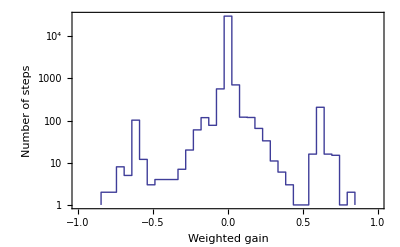

```mathematica
wgh=ListLogPlot[histLine["student"],Joined->True,Axes->False,Frame->True,FrameLabel->{"Weighted gain","Number of steps"},BaseStyle->journalStyle,PlotRange->{{-1,1},{1,All}}]
```

```mathematica
Export["weighted-gain-histogram.eps",wgh]
```

weighted-gain-histogram.eps

If I blow it up, I get the same shape!

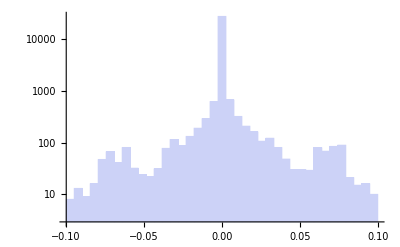

```mathematica
Histogram[Flatten[weightedGains["student"]],{-0.1,0.1,0.2/39},"LogCount"]
```

```mathematica
Needs["PlotLegends`"]
```

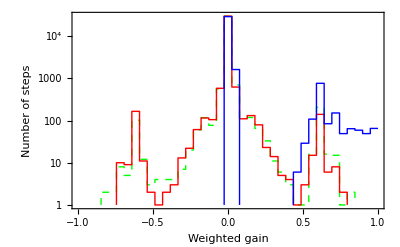

```mathematica
wgh2=ListLogPlot[{histLine["student"],histLine["reorder",1],histLine["ideal",1]},Joined->True,Axes->False,Frame->True,FrameLabel->{"Weighted gain","Number of steps"},LegendShadow->False,PlotStyle->{{Dashed,Green},Red,Blue},LegendSize->{0.6,.25},LegendTextSpace->4,PlotLegend->{"student dataset","random dataset","ideal dataset"},
LegendPosition->{0.23,.32},BaseStyle->journalStyle,PlotRange->{{-1,1},{1,All}}]
```

The eps file in Mathematica 7 is corrupted.

```mathematica
Export["weighted-gain-histogram2.eps",wgh2]
```

weighted-gain-histogram2.eps

Partial sum of weighed gains, adding all weighed gains whose magnitude is less than the cutoff.  This shows that most of the sum is from the weighed gains > 0.5.

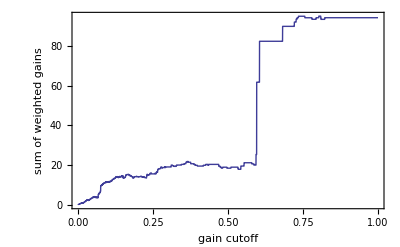

```mathematica
Block[{xxx=Flatten[weightedGains["student"]]},Plot[Total[Select[xxx,Abs[#]<x&]],{x,0,1},Axes->False,Frame->True,FrameLabel->{"gain cutoff","sum of weighted gains"},BaseStyle->{FontSize->12}]]
```

Partial sum of positive/negative weighed gains, adding all positive/negative weighed gains whose magnitude is less than the cutoff.  This shows that most of the positive/negative asymmetry is from large gains.

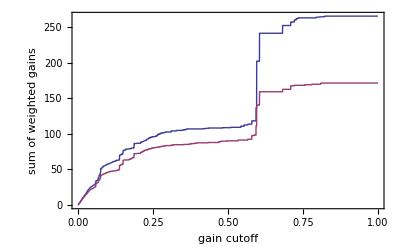

```mathematica
Block[{xxx=Flatten[weightedGains["student"]]},Plot[{Total[Select[xxx,0<#<x&]],Abs[Total[Select[xxx,0>#>-x&]]]},{x,0,1},Axes->False,Frame->True,FrameLabel->{"gain cutoff","sum of weighted gains"},BaseStyle->{FontSize->12}]]
```

#### Histogram of lengths for paper

```mathematica
histLineStudent=Block[{xxx=Map[Log[Length[Drop[#,3]]]&,data["student"]],max,dx},
max=Max[xxx];
dx=max/20;Flatten[Table[{{Exp[i-dx/2],#},{Exp[i+dx/2],#}}&[Max[0.001,Length[Select[xxx,i-dx/2≤#<i+dx/2&]]]],{i,0,max,dx}],1]];
```

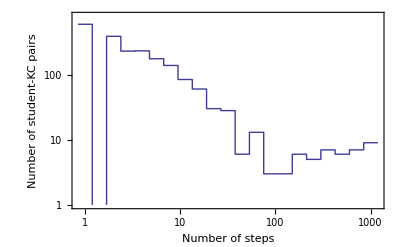

```mathematica
sklh=ListLogLogPlot[histLineStudent,Joined->True,PlotRange->{1,Max[Map[#[[2]]&,histLineStudent]] 4/3},Axes->False,Frame->True,FrameLabel->{"Number of steps","Number of student-KC pairs"},BaseStyle->journalStyle]
```

```mathematica
Export["student-kc-length-histogram.eps",sklh]
```

student-kc-length-histogram.eps

#### Example KC for paper

```mathematica
data1={0,0,0,1,1,0,1,1};
```

```mathematica
aics=Table[{i,N[2*If[i==1,1,2]-2*stepFit[data1,i]]},{i,Length[data1]}]
```

{{1,13.0904},{2,13.5607},{3,11.6382},{4,9.00402},{5,12.9974},{6,14.5492},{7,11.6382},{8,13.5607}}

```mathematica
weights1=Function[x,x/Apply[Plus,x]][N[Table[Block[{aic=2*If[i==1,1,2]-2*stepFit[data1,i]},Exp[-aic/2]],{i,Length[data1]}]]]
```

{0.0626582,0.0495269,0.129514,0.483407,0.0656404,0.030213,0.129514,0.0495269}

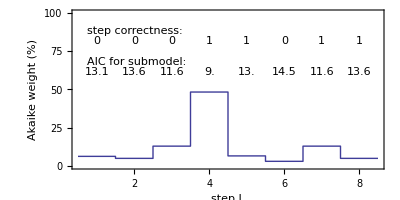

```mathematica
stepWeightsPlot=Block[{n=Length[data1],yt=85,y2=65},ListPlot[Flatten[Table[{{i-1/2,#},{i+1/2,#}}&[weights1[[i]]*100],{i,n}],1],Epilog->{Text["step correctness:",{0.75,yt},{-1,-1}],Table[Text[data1[[i]],{i,yt},{0,1}],{i,n}],
Text["AIC for submodel:",{0.75,y2},{-1,-1}],
	Map[Text[Round[#[[2]],0.1],{#[[1]],y2},{0,1}]&,aics]},PlotRange->{{1/2,n+1/2},{0,100}},
Joined->True,
FrameLabel->{"step L","Akaike weight (%)"}, AspectRatio->1/2,Axes->False,Frame->True,BaseStyle->If[True (* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->20}]]]
```

For Presentation, want width 7 in = 504pt and presentation BaseStyle

```mathematica
Export["step-weights.png",stepWeightsPlot,ImageSize->504]
```

step-weights.png

```mathematica
Export["step-weights.eps",stepWeightsPlot]
```

step-weights.eps

### Stuff

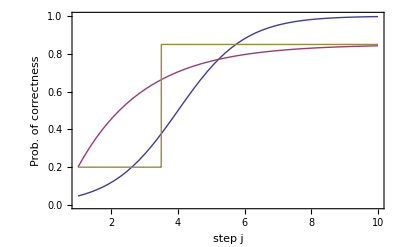

```mathematica
pModels=Plot[{logistic[x,{4,1}],bkt[x,{.5,.2,.15}],step[x,{4,.2,.15}]},{x,1,10},PlotRange->{0,1},Axes->False,Frame->True,FrameLabel->{"step j","Prob. of correctness"},BaseStyle->If[False(* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->20}]]
```

4.62 in or 332 points

```mathematica
Export["plot-models.png",pModels,ImageSize->400]
```

plot-models.png

Step function model

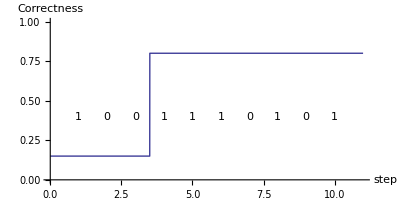

```mathematica
stepPlot=Block[{l=3.5,pg=.15,ps=0.2},Plot[If[x<l,pg,1-ps],{x,0,11},PlotRange->{0,1},Epilog->{Table[Text[If[x<l,If[RandomReal[]>pg,0,1],If[RandomReal[]<ps,0,1]],{x,.4}],{x,1,10}]},AxesLabel->{"step","Correctness"},BaseStyle->{FontSize->12}, AspectRatio->1/2]]
```

```mathematica
Export["step.eps",stepPlot]
```

step.eps

### Compare models

Logistic, step model, Baysian Knowledge Tracing

```mathematica
Get["fitAll.m"];
```

```mathematica
Get["fitRandomData50.m"];
```

```mathematica
Get["fitRandomData25.m"];
```

```mathematica
Get["fitRandomData10.m"];
```

```mathematica
Get["fitTriangles.m"];
```

Test that fits were successful

Here, set cutValues to the desired variable to get a particular dataset.

```mathematica
cutValues[ss_]:=Select[ss,#[[3]]≥10&]
```

```mathematica
testFits[ss_]:=(Map[(* Subtract off the 2K since we want to compare log likelihoods. *)Block[{x=#[[8]]-2*1},If[#[[4]]-2*2>x,Print["Bad aics for logistic ",#]];If[#[[5]]-2*3>x,Print["Bad aics for step ",#]];If[#[[6]]-2*3>x,Print["Bad aics for bkt ",#]];
If[#[[7]]-2*3>x,Print["Bad aics for bkt2 ",#]];If[#[[9]]-2*2>x,Print["Bad aics for linear ",#]]]&,cutValues[ss]];)
```

```mathematica
distinctCounts[ss_]:={Length[cutValues[ss]],Length[Union[Map[First,cutValues[ss]]]],Length[Union[Map[#[[2]]&,cutValues[ss]]]]}
```

```mathematica
aics[ss_]:=Map[{#[[4]]+aicCorrection[2,#[[3]]],#[[5]]+aicCorrection[3,#[[3]]],#[[6]]+aicCorrection[3,#[[3]]],#[[7]]+aicCorrection[3,#[[3]]],#[[9]]+aicCorrection[2,#[[3]]]}&,cutValues[ss]];
```

```mathematica
akaikeWeights[ss_]:=Map[Block[{y=Exp[-#/2]},y/Total[y]]&,aics[ss]];
```

```mathematica
weightAverages[ss_]:=Map[{Median[#],Mean[#],StandardDeviation[#]/Length[#]}&,Transpose[akaikeWeights[ss]]]
```

Test that numerical fits are better than constant model.

```mathematica
testFits[allValues]
```

Bad aics for bkt2 {compo-general-case,md5:1da7d76bc3d524d51da47dde26ee8f95,35,45.7909,44.1909,45.2987,47.9428,2-2 (-25 Log[7/5]-10 Log[7/2]),45.7897}

Bad aics for bkt2 {compo-parallel-axis,md5:cd1fe126b8b0bd0ae31146c5a59e6dce,61,88.4164,87.3671,88.548,90.5282,2-2 (-32 Log[61/32]-29 Log[61/29]),88.4164}

Bad aics for bkt2 {compo-parallel-axis,md5:55108dec2fb88e9c2af83be92d0520de,26,17.7489,17.0864,19.9383,21.6235,2-2 (-24 Log[13/12]-2 Log[13]),17.8086}

Bad aics for bkt2 {compo-parallel-axis,md5:e9747bab59caf0446778cc6a65a8ac2e,69,87.0277,86.566,86.566,89.2203,2-2 (-49 Log[69/49]-20 Log[69/20]),87.0297}

Bad aics for bkt2 {define-charge,md5:cd1fe126b8b0bd0ae31146c5a59e6dce,23,16.7586,16.8132,19.4027,19.7752,2-2 (-21 Log[23/21]-2 Log[23/2]),16.6276}

Bad aics for bkt2 {define-charge,md5:55108dec2fb88e9c2af83be92d0520de,21,21.2249,21.0121,22.8216,23.4983,2-2 (-18 Log[7/6]-3 Log[7]),21.2249}

Bad aics for bkt2 {define-mass,md5:e9747bab59caf0446778cc6a65a8ac2e,34,28.6185,28.6849,30.376,32.1119,2-2 (-30 Log[17/15]-4 Log[17/2]),28.6175}

Bad aics for bkt2 {draw-body,md5:a38723384afd4471b62218d16045a11d,61,47.4403,45.01,49.2189,50.9521,2-2 (-54 Log[61/54]-7 Log[61/7]),47.4451}

Bad aics for bkt2 {draw-body,md5:b50efcf571b671cf01b499841c66daf2,57,65.2013,63.6435,65.8743,67.5257,2-2 (-44 Log[57/44]-13 Log[57/13]),65.2016}

Bad aics for bkt2 {draw-body,md5:55108dec2fb88e9c2af83be92d0520de,45,30.5754,30.0464,32.8079,35.992,2-2 (-41 Log[45/41]-4 Log[45/4]),30.6114}

Bad aics for bkt2 {draw-body,md5:98deb41457bbea23b29b480e9530ad7c,44,35.1478,32.615,36.912,39.0687,2-2 (-39 Log[44/39]-5 Log[44/5]),35.1447}

Bad aics for bkt2 {draw-body,md5:e9747bab59caf0446778cc6a65a8ac2e,63,67.8042,67.2105,69.5126,70.3144,2-2 (-50 Log[63/50]-13 Log[63/13]),67.8081}

Bad aics for bkt2 {draw-velocity-straight,md5:e9747bab59caf0446778cc6a65a8ac2e,30,34.013,33.554,35.5671,36.1312,2-2 (-24 Log[5/4]-6 Log[5]),34.0118}

Bad aics for bkt2 {draw-velocity-straight,md5:55108dec2fb88e9c2af83be92d0520de,32,41.9476,41.9238,43.2833,44.3839,2-2 (-23 Log[32/23]-9 Log[32/9]),41.9363}

Bad aics for bkt2 {draw-velocity-straight,md5:cd1fe126b8b0bd0ae31146c5a59e6dce,30,34.0241,33.554,35.136,36.247,2-2 (-24 Log[5/4]-6 Log[5]),34.0241}

Bad aics for bkt2 {draw-velocity-straight,md5:b50efcf571b671cf01b499841c66daf2,31,39.3697,39.5434,40.7309,41.4164,2-2 (-23 Log[31/23]-8 Log[31/8]),39.3738}

Bad aics for bkt2 {draw-weight,md5:e9747bab59caf0446778cc6a65a8ac2e,18,22.9616,21.844,21.844,25.174,2-2 (-14 Log[9/7]-4 Log[9/2]),22.9821}

Bad aics for bkt2 {equation-syntax,md5:cd1fe126b8b0bd0ae31146c5a59e6dce,998,14.8839,14.8999,21.8085,36.8538,2-2 (-997 Log[998/997]-Log[998]),18.4861}

Bad aics for bkt2 {equation-syntax,md5:b50efcf571b671cf01b499841c66daf2,868,30.9886,30.356,34.2828,95.2476,2-2 (-866 Log[434/433]-2 Log[434]),31.0301}

Bad aics for bkt2 {equation-syntax,md5:55108dec2fb88e9c2af83be92d0520de,567,18.3292,18.4782,20.6754,75.9012,2-2 (-566 Log[567/566]-Log[567]),18.0996}

Bad aics for bkt2 {equation-syntax,md5:5e8914eb96d8caf02138110b93b5add5,734,11.6625,11.7416,13.7059,36.4053,2-2 (-733 Log[734/733]-Log[734]),17.8238}

Bad aics for bkt2 {equation-syntax,md5:e3e61859acb08ee896e06e1020f95a49,939,14.8189,14.8354,21.6864,36.8523,2-2 (-938 Log[939/938]-Log[939]),18.3659}

Bad aics for bkt2 {write-known-value-eqn,md5:cd1fe126b8b0bd0ae31146c5a59e6dce,213,226.254,224.887,226.417,229.414,2-2 (-167 Log[213/167]-46 Log[213/46]),226.253}

Bad aics for bkt2 {write-known-value-eqn,md5:55108dec2fb88e9c2af83be92d0520de,181,129.773,125.757,131.772,133.621,2-2 (-161 Log[181/161]-20 Log[181/20]),129.772}

Bad aics for bkt2 {write-known-value-eqn,md5:e9747bab59caf0446778cc6a65a8ac2e,208,163.412,159.319,162.041,167.83,2-2 (-181 Log[208/181]-27 Log[208/27]),163.59}

Bad aics for bkt2 {write-nsl-compo,md5:e9747bab59caf0446778cc6a65a8ac2e,14,23.4037,23.9448,23.9448,25.4251,2+28 Log[2],23.4037}

```mathematica
testFits[randomValues50]
```

Bad aics for bkt2 {Null,Null,50,72.007,70.4435,71.8003,74.4921,2-2 (-29 Log[50/29]-21 Log[50/21]),72.007}

Bad aics for bkt2 {Null,Null,50,71.2996,70.1094,72.2659,73.409,2-2 (-30 Log[5/3]-20 Log[5/2]),71.2996}

Bad aics for bkt2 {Null,Null,50,66.6428,63.9492,66.3627,68.9206,2-2 (-34 Log[25/17]-16 Log[25/8]),66.644}

Bad aics for bkt2 {Null,Null,50,73.28,70.9642,72.7411,75.3703,2+100 Log[2],73.2801}

```mathematica
testFits[randomValues25]
```

Bad aics for bkt2 {Null,Null,25,38.605,38.5296,39.1042,40.6659,2-2 (-13 Log[25/13]-12 Log[25/12]),38.605}

```mathematica
testFits[randomValues10]
```

Bad aics for bkt2 {Null,Null,10,17.4602,18.1949,18.3653,19.487,2-2 (-6 Log[5/3]-4 Log[5/2]),17.4602}

Bad aics for bkt2 {Null,Null,10,17.8508,18.3653,18.3653,19.8732,2+20 Log[2],17.8509}

real data

```mathematica
weightAverages[allValues]
```

{{0.527527,0.49128,0.000687798},{0.329957,0.365027,0.00067914},{0.135349,0.143693,0.000259762}}

random generated data length 100

```mathematica
weightAverages[randomValues100]
```

{{0.248307,0.24196,0.00121802},{0.586212,0.591812,0.00172043},{0.175313,0.166228,0.000766615}}

random generated data length 10

```mathematica
weightAverages[randomValues10]
```

{{0.634076,0.625129,0.00010423},{0.235561,0.256909,0.000101833},{0.113848,0.117961,0.0000457033}}

```mathematica
weightAverages[triangleValues10]
```

{{0.509128,0.499414,0.00115018},{0.385168,0.387345,0.00127623},{0.112445,0.113242,0.000415912}}

```mathematica
weightAverages[triangleValues100]
```

{{0.000228653,0.00109422,0.0000211165},{0.979802,0.95599,0.000617848},{0.0199063,0.0429153,0.00060769}}

```mathematica
Table[Length[Select[akaikeWeights[allValues],(Max[#]==#[[i]])&]],{i,5}]
```

{101,91,0,0,127}

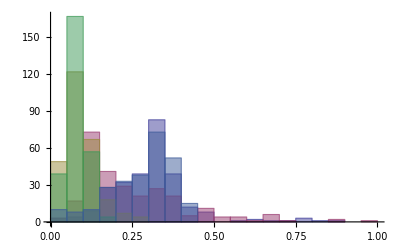

```mathematica
Histogram[Transpose[akaikeWeights[allValues]]]
```

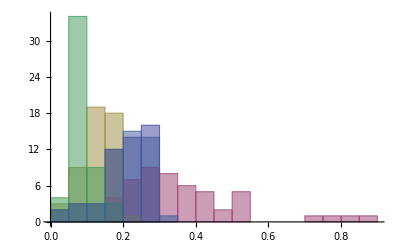

```mathematica
Histogram[Transpose[akaikeWeights[randomValues50]]]
```

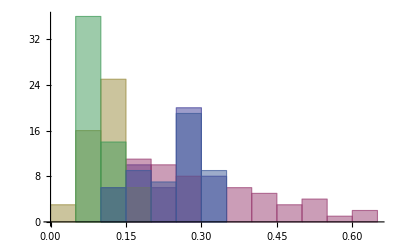

```mathematica
Histogram[Transpose[akaikeWeights[randomValues25]]]
```

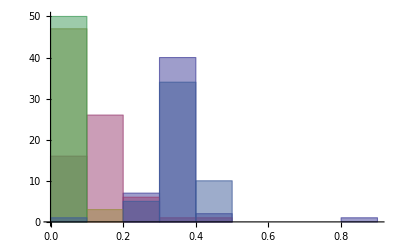

```mathematica
Histogram[Transpose[akaikeWeights[randomValues10]]]
```

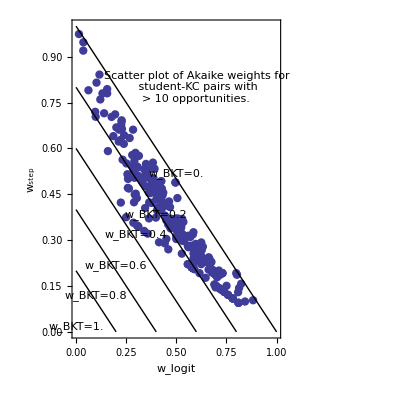

```mathematica
scatterWeights=ListPlot[Map[({#[[1]],#[[2]]}/(#[[1]]+#[[2]]+Max[#[[3]],#[[4]]]))&,akaikeWeights[allValues]],AspectRatio->1,PlotStyle->{PointSize[0.015]},Epilog->{Text[Style["Scatter plot of Akaike weights for\n student-KC pairs with\n> 10 opportunities.",TextAlignment->Right],{.6,0.8}],Table[{Line[{{0,i},{i,0}}],Text[SequenceForm[Subscript[w,BKT],"=",N[1-i]],{i/2,i/2},{0,If[i==4/5,1,-1]},{1,-1}]},{i,0,1,1/5}]},PlotRange->{{0,1},{0,1}},Axes->False,Frame->True,FrameLabel->{Subscript[w,logit],Subscript[w,step]},BaseStyle->If[True(* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->20}]]
```

4.62 in or 332 points

```mathematica
Export["scatter-weights.png",scatterWeights,ImageSize->400]
```

scatter-weights.png

```mathematica
Export["scatter-weights.eps",scatterWeights]
```

scatter-weights.eps

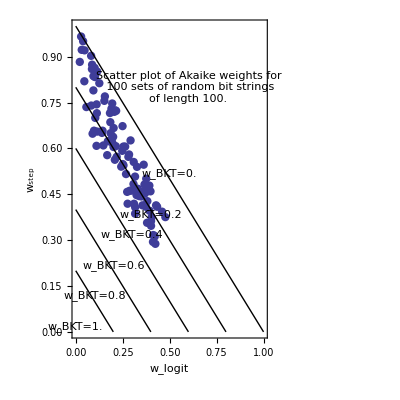

```mathematica
scatterRandomWeights=ListPlot[Map[Take[#,2]&,akaikeWeights[randomValues100]],AspectRatio->1,PlotStyle->{PointSize[0.015]},Epilog->{Text[Style["Scatter plot of Akaike weights for\n 100 sets of random bit strings\nof length 100.",TextAlignment->Right],{.6,0.8}],Table[{Line[{{0,i},{i,0}}],Text[SequenceForm[Subscript[w,BKT],"=",N[1-i]],{i/2,i/2},{0,If[i==4/5,1,-1]},{1,-1}]},{i,0,1,1/5}]},PlotRange->{{0,1},{0,1}},Axes->False,Frame->True,FrameLabel->{Subscript[w,logit],Subscript[w,step]},BaseStyle->If[True(* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->20}]]
```

4.62 in or 332 points

```mathematica
Export["scatter-random-weights.png",scatterRandomWeights,ImageSize->400]
```

scatter-random-weights.png

```mathematica
Export["scatter-random-weights.eps",scatterRandomWeights]
```

scatter-random-weights.eps

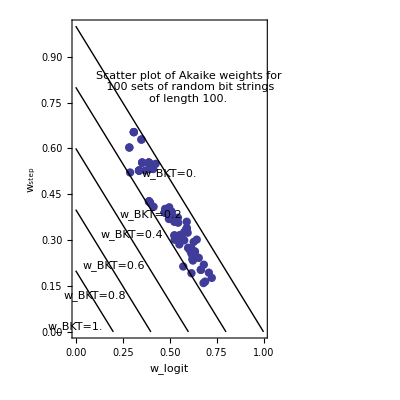

```mathematica
scatterTriangleWeights=ListPlot[Map[Take[#,2]&,akaikeWeights[triangleValues10]],AspectRatio->1,PlotStyle->{PointSize[0.015]},Epilog->{Text[Style["Scatter plot of Akaike weights for\n 100 sets of random bit strings\nof length 100.",TextAlignment->Right],{.6,0.8}],Table[{Line[{{0,i},{i,0}}],Text[SequenceForm[Subscript[w,BKT],"=",N[1-i]],{i/2,i/2},{0,If[i==4/5,1,-1]},{1,-1}]},{i,0,1,1/5}]},PlotRange->{{0,1},{0,1}},Axes->False,Frame->True,FrameLabel->{Subscript[w,logit],Subscript[w,step]},BaseStyle->If[True(* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->20}]]
```

```mathematica
Block[{m1=5,m2=1,m3=2,names={"logit","step","bkt","bkt2","linear"}},Histogram3D[Map[{#[[m1]],#[[m2]]}/(#[[m1]]+#[[m2]]+#[[m3]])&,akaikeWeights[allValues]],{{0,1,0.02},{0,1,0.02}},
AxesLabel->{names[[m1]],names[[m2]]},PlotRange->{{0,1},{0,1},All}]]
```

-Graphics3D-

```mathematica
Block[{m1=5,m2=1,m3=2,names={"logit","step","bkt","bkt2","linear"}},Histogram3D[Map[{#[[m1]],#[[m2]]}/(#[[m1]]+#[[m2]]+#[[m3]])&,akaikeWeights[randomValues10]],{{0,1,0.02},{0,1,0.02}},
AxesLabel->{names[[m1]],names[[m2]]},PlotRange->{{0,1},{0,1},All}]]
```

-Graphics3D-